```mathematica
Needs["Greater2`"]
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
?Metric
?ds2met
```

### DeWolfe Back Reaction

#### AdS Back Reaction as in DeWolfe - My sign conventions

```mathematica
Clear[gη]
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}*)
gη = -{{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}
(*gη = {{-E^(2A[η]),0,0,0,0},{0,E^(2A[η]),0,0,0},{0,0,E^(2A[η]),0,0},{0,0,0,E^(2A[η]),0},{0,0,0,0,1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
GTη//MatrixForm
```

{{-ⅇ^(2 A[η]),0,0,0,0},{0,ⅇ^(2 A[η]),0,0,0},{0,0,ⅇ^(2 A[η]),0,0},{0,0,0,ⅇ^(2 A[η]),0},{0,0,0,0,1}}

(-ⅇ^(2 A[η]) | 0 | 0 | 0 | 0
0 | ⅇ^(2 A[η]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 A[η]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 A[η]) | 0
0 | 0 | 0 | 0 | 1)

-ⅇ^(8 A[η])

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

-4 (5 A'[η]^2+2 A''[η])

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

```mathematica
ϕeqnη=Simplify[-1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]]
TTη =(- DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(-gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) -E^(2 A[η])DiagonalMatrix[{-1,1,1,1,0}] λ[ϕ[η]])
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm
AprimeSol=Solve[EFEη[[1,1]]==0,A'[η]][[2]]
AprimeprimeSol=Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]
Aprimeprimeeqn =A''[η]-(A''[η]/.AprimeprimeSol)
Simplify[EFEη/.AprimeprimeSol]
Aprimeeqn =A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

{{ⅇ^(2 A[η]) λ[ϕ[η]]+ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0,0,0,0},{0,-ⅇ^(2 A[η]) λ[ϕ[η]]-ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0,0,0},{0,0,-ⅇ^(2 A[η]) λ[ϕ[η]]-ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0,0},{0,0,0,-ⅇ^(2 A[η]) λ[ϕ[η]]-ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0},{0,0,0,0,V[ϕ[η]]-1/2 ϕ'[η]^2}}

(1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-12 A'[η]^2+κ ϕ'[η]^2-6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-κ ϕ'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-κ ϕ'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | -κ V[ϕ[η]]+6 A'[η]^2+1/2 κ ϕ'[η]^2)

{A'[η]→(√(2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]+κ ϕ'[η]^2-6 A''[η]))/(2 √3)}

{A''[η]→1/3 (-κ λ[ϕ[η]]+κ ϕ'[η]^2)}

1/3 (κ λ[ϕ[η]]-κ ϕ'[η]^2)+A''[η]

{{1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]-12 A'[η]^2-κ ϕ'[η]^2),0,0,0,0},{0,1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2),0,0,0},{0,0,1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2),0,0},{0,0,0,1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2),0},{0,0,0,0,-κ V[ϕ[η]]+6 A'[η]^2+1/2 κ ϕ'[η]^2}}

A'[η]^2+1/12 (-2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]-κ ϕ'[η]^2+2 (-κ λ[ϕ[η]]+κ ϕ'[η]^2))

```mathematica
ϕeqnη
Expand[Aprimeprimeeqn /.κ->(4 M^3)^-1]/.M->1/2
Simplify[Expand[Aprimeeqn/.κ->(4 M^3)^-1] M^3 24]/.M->1/2
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

2/3 λ[ϕ[η]]-2/3 ϕ'[η]^2+A''[η]

1/2 (-2 V[ϕ[η]]+6 A'[η]^2+ϕ'[η]^2)

```mathematica
W[ϕ[η]]=3/L-b ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Expand[Simplify[1/8(D[W[ϕ[η]],ϕ[η]])^2+1/3 W[ϕ[η]]^2]]
ϕW'[η]=1/2 D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[-1/3 W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]
```

3/L-b ϕ[η]^2

3/L^2+1/2 b^2 ϕ[η]^2-(2 b ϕ[η]^2)/L+1/3 b^2 ϕ[η]^4

-b ϕ[η]

-1/L+1/3 b ϕ[η]^2

{ϕ[η]→ⅇ^(-b η) C[1]}

{{A[η]→-η/L-1/6 ⅇ^(-2 b η) C[1]^2+C[2]}}

#### AdS Back Reaction as in DeWolfe - Their sign conventions

```mathematica
Clear[gη]
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}*)
gη ={{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}
(*gη = {{-E^(2A[η]),0,0,0,0},{0,E^(2A[η]),0,0,0},{0,0,E^(2A[η]),0,0},{0,0,0,E^(2A[η]),0},{0,0,0,0,1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
GTη//MatrixForm
```

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) | 0
0 | 0 | 0 | 0 | -1)

ⅇ^(8 A[η])

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

20 A'[η]^2+8 A''[η]

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]]
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) -E^(2 A[η])DiagonalMatrix[{-1,1,1,1,0}] λ[ϕ[η]]
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm
AprimeSol=Solve[EFEη[[1,1]]==0,A'[η]][[2]]
AprimeprimeSol=Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]
Aprimeprimeeqn =A''[η]-(A''[η]/.AprimeprimeSol)
Simplify[EFEη/.AprimeprimeSol]
Aprimeeqn =A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

{{ⅇ^(2 A[η]) λ[ϕ[η]]-ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0,0,0,0},{0,-ⅇ^(2 A[η]) λ[ϕ[η]]+ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0,0,0},{0,0,-ⅇ^(2 A[η]) λ[ϕ[η]]+ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0,0},{0,0,0,-ⅇ^(2 A[η]) λ[ϕ[η]]+ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2),0},{0,0,0,0,-V[ϕ[η]]+1/2 ϕ'[η]^2}}

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-1/2 κ ϕ'[η]^2)

{A'[η]→(√(-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-κ ϕ'[η]^2-6 A''[η]))/(2 √3)}

{A''[η]→1/3 (-κ λ[ϕ[η]]-κ ϕ'[η]^2)}

1/3 (κ λ[ϕ[η]]+κ ϕ'[η]^2)+A''[η]

{{1/2 ⅇ^(2 A[η]) (-2 κ V[ϕ[η]]-12 A'[η]^2+κ ϕ'[η]^2),0,0,0,0},{0,1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+12 A'[η]^2-κ ϕ'[η]^2),0,0,0},{0,0,1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+12 A'[η]^2-κ ϕ'[η]^2),0,0},{0,0,0,1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+12 A'[η]^2-κ ϕ'[η]^2),0},{0,0,0,0,κ V[ϕ[η]]+6 A'[η]^2-1/2 κ ϕ'[η]^2}}

A'[η]^2+1/12 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+κ ϕ'[η]^2+2 (-κ λ[ϕ[η]]-κ ϕ'[η]^2))

```mathematica
ϕeqnη
Expand[Aprimeprimeeqn /.κ->(4 M^3)^-1](*/.M->1/2*)
Expand[Aprimeeqn/.κ->(4 M^3)^-1](*/.M->1/2*)
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

λ[ϕ[η]]/(12 M^3)+ϕ'[η]^2/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

```mathematica
W[ϕ[η]]=(24 M^3)/L-ϵ/L ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/8(D[W[ϕ[η]],ϕ[η]])^2-1/(24 M^3)W[ϕ[η]]^2]
Expand[VW[ϕ[η]]]
ϕW'[η]=1/2 D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]]
```

(24 M^3)/L-(ϵ ϕ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ϕ[η]^2+ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ϕ[η]^2)/L^2+(ϵ^2 ϕ[η]^2)/(2 L^2)-(ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(ϵ ϕ[η])/L

(-24+(ϵ ϕ[η]^2)/M^3)/(24 L)

{ϕ[η]→ⅇ^(-(ϵ η)/L) C[1]}

{{A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]}}

```mathematica
(2 ϵ ϕ[η]^2)/L^2+(ϵ^2 ϕ[η]^2)/(2 L^2)//Simplify
Simplify[ϵ/.Solve[%==Mϕ^2/2 ϕ[η]^2,ϵ]]
```

(ϵ (4+ϵ) ϕ[η]^2)/(2 L^2)

{-2-√(4+L^2 Mϕ^2),-2+√(4+L^2 Mϕ^2)}

### GW Back reactions

```mathematica
Clear[gη]

TofX=T[t,x,y,z,η];
(*gη ={{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}*)
gη ={{E^(-2 η/l TofX),0,0,0,0},{0,-E^(-2 η/l TofX),0,0,0},{0,0,-E^(-2 η/l TofX),0,0},{0,0,0,-E^(-2 η/l TofX),0},{0,0,0,0,-TofX^2}}
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
GTη//MatrixForm
```

{{ⅇ^(-(2 η T[t,x,y,z,η])/l),0,0,0,0},{0,-ⅇ^(-(2 η T[t,x,y,z,η])/l),0,0,0},{0,0,-ⅇ^(-(2 η T[t,x,y,z,η])/l),0,0},{0,0,0,-ⅇ^(-(2 η T[t,x,y,z,η])/l),0},{0,0,0,0,-T[t,x,y,z,η]^2}}

(ⅇ^(-(2 η T[t,x,y,z,η])/l) | 0 | 0 | 0 | 0
0 | -ⅇ^(-(2 η T[t,x,y,z,η])/l) | 0 | 0 | 0
0 | 0 | -ⅇ^(-(2 η T[t,x,y,z,η])/l) | 0 | 0
0 | 0 | 0 | -ⅇ^(-(2 η T[t,x,y,z,η])/l) | 0
0 | 0 | 0 | 0 | -T[t,x,y,z,η]^2)

ⅇ^(-(8 η T[t,x,y,z,η])/l) T[t,x,y,z,η]^2

((ⅇ^(-(2 η T[t,x,y,z,η])/l) (l η (T^(0,0,0,0,1)[t,x,y,z,η])^2-T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-4 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])+T[t,x,y,z,η]^3 (4+2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])+T[t,x,y,z,η]^2 (8 η T^(0,0,0,0,1)[t,x,y,z,η]-ⅇ^((2 η T[t,x,y,z,η])/l) l (η (T^(0,0,0,1,0)[t,x,y,z,η])^2+η (T^(0,0,1,0,0)[t,x,y,z,η])^2+η (T^(0,1,0,0,0)[t,x,y,z,η])^2+η (T^(1,0,0,0,0)[t,x,y,z,η])^2+l T^(2,0,0,0,0)[t,x,y,z,η]))))/(l^2 T[t,x,y,z,η]^3) | (2 η (-l+η T[t,x,y,z,η]) T^(0,1,0,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,1,0,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(1,0,0,0,1)[t,x,y,z,η]))/l
(2 η (-l+η T[t,x,y,z,η]) T^(0,1,0,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,1,0,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (ⅇ^(-(2 η T[t,x,y,z,η])/l) (-l η (T^(0,0,0,0,1)[t,x,y,z,η])^2+T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-4 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])-T[t,x,y,z,η]^2 (8 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-η (T^(0,0,0,1,0)[t,x,y,z,η])^2-η (T^(0,0,1,0,0)[t,x,y,z,η])^2+η (T^(0,1,0,0,0)[t,x,y,z,η])^2+l T^(0,2,0,0,0)[t,x,y,z,η]+η (T^(1,0,0,0,0)[t,x,y,z,η])^2))+T[t,x,y,z,η]^3 (-4-2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]-2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]+2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])))/(l^2 T[t,x,y,z,η]^3) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,1,0,0,1)[t,x,y,z,η]))/l
(2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (ⅇ^(-(2 η T[t,x,y,z,η])/l) (-l η (T^(0,0,0,0,1)[t,x,y,z,η])^2+T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-4 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])-T[t,x,y,z,η]^2 (8 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-η (T^(0,0,0,1,0)[t,x,y,z,η])^2+η (T^(0,0,1,0,0)[t,x,y,z,η])^2+l T^(0,0,2,0,0)[t,x,y,z,η]-η (T^(0,1,0,0,0)[t,x,y,z,η])^2+η (T^(1,0,0,0,0)[t,x,y,z,η])^2))+T[t,x,y,z,η]^3 (-4-2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]-2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]+2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])))/(l^2 T[t,x,y,z,η]^3) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,0,1,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,1,0,1)[t,x,y,z,η]))/l
(2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,0,1,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (ⅇ^(-(2 η T[t,x,y,z,η])/l) (-l η (T^(0,0,0,0,1)[t,x,y,z,η])^2+T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-4 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])-T[t,x,y,z,η]^2 (8 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (η (T^(0,0,0,1,0)[t,x,y,z,η])^2+l T^(0,0,0,2,0)[t,x,y,z,η]-η ((T^(0,0,1,0,0)[t,x,y,z,η])^2+(T^(0,1,0,0,0)[t,x,y,z,η])^2-(T^(1,0,0,0,0)[t,x,y,z,η])^2)))+T[t,x,y,z,η]^3 (-4+3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]-2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]-2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]+2 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])))/(l^2 T[t,x,y,z,η]^3) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,0,1,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,0,1,1)[t,x,y,z,η]))/l
(3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(1,0,0,0,1)[t,x,y,z,η]))/l | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,1,0,0,1)[t,x,y,z,η]))/l | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,1,0,1)[t,x,y,z,η]))/l | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,0,1,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,0,1,1)[t,x,y,z,η]))/l | -(4 T[t,x,y,z,η]^3+4 l η (T^(0,0,0,0,1)[t,x,y,z,η])^2-4 T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])+T[t,x,y,z,η]^2 (8 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-2 η (T^(0,0,0,1,0)[t,x,y,z,η])^2+l T^(0,0,0,2,0)[t,x,y,z,η]-2 η (T^(0,0,1,0,0)[t,x,y,z,η])^2+l T^(0,0,2,0,0)[t,x,y,z,η]-2 η (T^(0,1,0,0,0)[t,x,y,z,η])^2+l T^(0,2,0,0,0)[t,x,y,z,η]+2 η (T^(1,0,0,0,0)[t,x,y,z,η])^2-l T^(2,0,0,0,0)[t,x,y,z,η])))/(l^2 T[t,x,y,z,η]))

1/(l^2 T[t,x,y,z,η]^3)2 (4 l η (T^(0,0,0,0,1)[t,x,y,z,η])^2-2 T[t,x,y,z,η] (2 l T^(0,0,0,0,1)[t,x,y,z,η]-5 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+2 l η T^(0,0,0,0,2)[t,x,y,z,η])+T[t,x,y,z,η]^3 (10+3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2-3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2-3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]-3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2+3 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])+T[t,x,y,z,η]^2 (20 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-2 η (T^(0,0,0,1,0)[t,x,y,z,η])^2+l T^(0,0,0,2,0)[t,x,y,z,η]-2 η (T^(0,0,1,0,0)[t,x,y,z,η])^2+l T^(0,0,2,0,0)[t,x,y,z,η]-2 η (T^(0,1,0,0,0)[t,x,y,z,η])^2+l T^(0,2,0,0,0)[t,x,y,z,η]+2 η (T^(1,0,0,0,0)[t,x,y,z,η])^2-l T^(2,0,0,0,0)[t,x,y,z,η])))

((ⅇ^(-(2 η T[t,x,y,z,η])/l) (-3 l η (T^(0,0,0,0,1)[t,x,y,z,η])^2+3 T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-2 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])-T[t,x,y,z,η]^3 (6+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]-3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2)-T[t,x,y,z,η]^2 (12 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-η (T^(0,0,0,1,0)[t,x,y,z,η])^2+l T^(0,0,0,2,0)[t,x,y,z,η]-η (T^(0,0,1,0,0)[t,x,y,z,η])^2+l T^(0,0,2,0,0)[t,x,y,z,η]-η (T^(0,1,0,0,0)[t,x,y,z,η])^2+l T^(0,2,0,0,0)[t,x,y,z,η]+3 η (T^(1,0,0,0,0)[t,x,y,z,η])^2))))/(l^2 T[t,x,y,z,η]^3) | (2 η (-l+η T[t,x,y,z,η]) T^(0,1,0,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,1,0,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(1,0,0,0,1)[t,x,y,z,η]))/l
(2 η (-l+η T[t,x,y,z,η]) T^(0,1,0,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,1,0,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (ⅇ^(-(2 η T[t,x,y,z,η])/l) (3 l η (T^(0,0,0,0,1)[t,x,y,z,η])^2-3 T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-2 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])+T[t,x,y,z,η]^3 (6+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2+2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])+T[t,x,y,z,η]^2 (12 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-η (T^(0,0,0,1,0)[t,x,y,z,η])^2+l T^(0,0,0,2,0)[t,x,y,z,η]-η (T^(0,0,1,0,0)[t,x,y,z,η])^2+l T^(0,0,2,0,0)[t,x,y,z,η]-3 η (T^(0,1,0,0,0)[t,x,y,z,η])^2+η (T^(1,0,0,0,0)[t,x,y,z,η])^2-l T^(2,0,0,0,0)[t,x,y,z,η]))))/(l^2 T[t,x,y,z,η]^3) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,1,0,0,1)[t,x,y,z,η]))/l
(2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,1,0,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,1,0,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (ⅇ^(-(2 η T[t,x,y,z,η])/l) (3 l η (T^(0,0,0,0,1)[t,x,y,z,η])^2-3 T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-2 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])+T[t,x,y,z,η]^3 (6+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]-ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2+2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])+T[t,x,y,z,η]^2 (12 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-η (T^(0,0,0,1,0)[t,x,y,z,η])^2+l T^(0,0,0,2,0)[t,x,y,z,η]-3 η (T^(0,0,1,0,0)[t,x,y,z,η])^2-η (T^(0,1,0,0,0)[t,x,y,z,η])^2+l T^(0,2,0,0,0)[t,x,y,z,η]+η (T^(1,0,0,0,0)[t,x,y,z,η])^2-l T^(2,0,0,0,0)[t,x,y,z,η]))))/(l^2 T[t,x,y,z,η]^3) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,0,1,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,1,0,1)[t,x,y,z,η]))/l
(2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(1,0,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,1,0,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (2 η (-l+η T[t,x,y,z,η]) T^(0,0,0,1,0)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η]-l (l-2 η T[t,x,y,z,η]) T^(0,0,1,1,0)[t,x,y,z,η])/(l^2 T[t,x,y,z,η]) | (ⅇ^(-(2 η T[t,x,y,z,η])/l) (3 l η (T^(0,0,0,0,1)[t,x,y,z,η])^2-3 T[t,x,y,z,η] (l T^(0,0,0,0,1)[t,x,y,z,η]-2 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+l η T^(0,0,0,0,2)[t,x,y,z,η])+T[t,x,y,z,η]^3 (6+3 ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]-ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2+2 ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])+T[t,x,y,z,η]^2 (12 η T^(0,0,0,0,1)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) l (-3 η (T^(0,0,0,1,0)[t,x,y,z,η])^2-η (T^(0,0,1,0,0)[t,x,y,z,η])^2+l T^(0,0,2,0,0)[t,x,y,z,η]-η (T^(0,1,0,0,0)[t,x,y,z,η])^2+l T^(0,2,0,0,0)[t,x,y,z,η]+η (T^(1,0,0,0,0)[t,x,y,z,η])^2-l T^(2,0,0,0,0)[t,x,y,z,η]))))/(l^2 T[t,x,y,z,η]^3) | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,0,1,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,0,1,1)[t,x,y,z,η]))/l
(3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(1,0,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(1,0,0,0,1)[t,x,y,z,η]))/l | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,1,0,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,1,0,0,1)[t,x,y,z,η]))/l | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,1,0,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,1,0,1)[t,x,y,z,η]))/l | (3 η (-(T^(0,0,0,0,1)[t,x,y,z,η] T^(0,0,0,1,0)[t,x,y,z,η])/T[t,x,y,z,η]+T^(0,0,0,1,1)[t,x,y,z,η]))/l | (3 (4 η T[t,x,y,z,η] T^(0,0,0,0,1)[t,x,y,z,η]+2 η^2 (T^(0,0,0,0,1)[t,x,y,z,η])^2+T[t,x,y,z,η]^2 (2+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,0,1,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,0,2,0)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,0,1,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,0,2,0,0)[t,x,y,z,η]+ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(0,1,0,0,0)[t,x,y,z,η])^2-ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(0,2,0,0,0)[t,x,y,z,η]-ⅇ^((2 η T[t,x,y,z,η])/l) η^2 (T^(1,0,0,0,0)[t,x,y,z,η])^2+ⅇ^((2 η T[t,x,y,z,η])/l) l η T^(2,0,0,0,0)[t,x,y,z,η])))/l^2)

### AdS-S Backreaction

#### Play with ansatz

Try converting to gaussian normal coordinate in AdS-S

```mathematica
pofη=Simplify[p[η]/.DSolve[D[p[η],η]==√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
```

(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(√2)

```mathematica
pofη/.η->-C[1]+a
```

(ⅇ^(-a/l) √(ⅇ^((4 a)/l)+l^2 μ))/(√2)

```mathematica
Simplify[p[η]/.DSolve[D[p[η],η]==-√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
%/.η->-C[1]
```

(√(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 C[1])/l)+ⅇ^((4 η)/l) l^2 μ)))/(√2)

(√(ⅇ^((4 C[1])/l)+ⅇ^(-(4 C[1])/l) l^2 μ))/(√2)

```mathematica
FullSimplify[PowerExpand[FullSimplify[Simplify[D[pofη,η]]/.η->ηofp]]]
```

(√(p^4-l^2 μ))/(l p)

```mathematica
ηofp=η/.Solve[pofη==p,η][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 μ))]

```mathematica
Simplify[E^(ηofp/l)]
```

ⅇ^(-C[1]/l) √(p^2+√(p^4-l^2 μ))

```mathematica
FullSimplify[p[η]^2/l^2/.p[η]->pofη]
gii=%/.η->-C[1] - l A[η]
Simplify[p[η]^2/l^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.η->-C[1] - l A[η]]
```

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(2 l^2)

(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2)

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)-l^2 μ)^2)/(2 l^2 (ⅇ^((4 (η+C[1]))/l)+l^2 μ))

(ⅇ^(-2 A[η]) (-1+ⅇ^(4 A[η]) l^2 μ)^2)/(2 l^2 (1+ⅇ^(4 A[η]) l^2 μ))

```mathematica
gii/.μ->ϵ E^(-2 A[η])
Simplify[Series[%,{ϵ,0,1}]]
gtt/.μ->ϵ E^(-2 A[η])
Simplify[Series[%,{ϵ,0,1}]]
```

(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+ⅇ^(-2 A[η]) l^2 ϵ))/(2 l^2)

ⅇ^(-2 A[η])/(2 l^2)+ϵ/2+O[ϵ]^2

(ⅇ^(-2 A[η]) (-1+ⅇ^(2 A[η]) l^2 ϵ)^2)/(2 l^2 (1+ⅇ^(2 A[η]) l^2 ϵ))

ⅇ^(-2 A[η])/(2 l^2)-(3 ϵ)/2+O[ϵ]^2

```mathematica
Simplify[Series[gii,{μ,0,1}]]
Simplify[Series[gtt,{μ,0,1}]]
```

ⅇ^(-2 A[η])/(2 l^2)+1/2 ⅇ^(2 A[η]) μ+O[μ]^2

ⅇ^(-2 A[η])/(2 l^2)-3/2 ⅇ^(2 A[η]) μ+O[μ]^2

```mathematica
Clear[gη]
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}*)
gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}
(*gη = {{-E^(2A[η]),0,0,0,0},{0,E^(2A[η]),0,0,0},{0,0,E^(2A[η]),0,0},{0,0,0,E^(2A[η]),0},{0,0,0,0,1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
FullSimplify[GTη]//MatrixForm
```

{{(ⅇ^(-2 A[η]) (-1+ⅇ^(4 A[η]) l^2 μ)^2)/(2 l^2 (1+ⅇ^(4 A[η]) l^2 μ)),0,0,0,0},{0,-(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2),0,0,0},{0,0,-(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2),0,0},{0,0,0,-(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2),0},{0,0,0,0,-1}}

((ⅇ^(-2 A[η]) (-1+ⅇ^(4 A[η]) l^2 μ)^2)/(2 l^2 (1+ⅇ^(4 A[η]) l^2 μ)) | 0 | 0 | 0 | 0
0 | -(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+l^2 μ))/(2 l^2) | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 A[η]) (-1+ⅇ^(8 A[η]) l^4 μ^2)^2)/(16 l^8)

((ⅇ^(-2 A[η]) (-1+ⅇ^(4 A[η]) l^2 μ) (4 (-1+ⅇ^(8 A[η]) l^4 μ^2) A'[η]^2+(1+6 ⅇ^(4 A[η]) l^2 μ+ⅇ^(8 A[η]) l^4 μ^2) A''[η]))/(2 (l+ⅇ^(4 A[η]) l^3 μ)^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) (-4 (1+ⅇ^(4 A[η]) l^2 μ) A'[η]^2-(-1+ⅇ^(4 A[η]) l^2 μ) A''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) (-4 (1+ⅇ^(4 A[η]) l^2 μ) A'[η]^2-(-1+ⅇ^(4 A[η]) l^2 μ) A''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) (-4 (1+ⅇ^(4 A[η]) l^2 μ) A'[η]^2-(-1+ⅇ^(4 A[η]) l^2 μ) A''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | -4 A'[η]^2-(4 (1+ⅇ^(8 A[η]) l^4 μ^2) A''[η])/(-1+ⅇ^(8 A[η]) l^4 μ^2))

20 A'[η]^2+(8 (1+ⅇ^(8 A[η]) l^4 μ^2) A''[η])/(-1+ⅇ^(8 A[η]) l^4 μ^2)

(-(3 ⅇ^(-2 A[η]) (-1+ⅇ^(4 A[η]) l^2 μ)^2 (2 A'[η]^2-A''[η]+ⅇ^(4 A[η]) l^2 μ (2 A'[η]^2+A''[η])))/(2 (l+ⅇ^(4 A[η]) l^3 μ)^2) | 0 | 0 | 0 | 0
0 | (3 ⅇ^(-2 A[η]) (2 A'[η]^2-A''[η]))/(2 l^2)+(4 ⅇ^(2 A[η]) μ A''[η])/(-1+ⅇ^(4 A[η]) l^2 μ)+3/2 ⅇ^(2 A[η]) μ (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | (3 ⅇ^(-2 A[η]) (2 A'[η]^2-A''[η]))/(2 l^2)+(4 ⅇ^(2 A[η]) μ A''[η])/(-1+ⅇ^(4 A[η]) l^2 μ)+3/2 ⅇ^(2 A[η]) μ (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | (3 ⅇ^(-2 A[η]) (2 A'[η]^2-A''[η]))/(2 l^2)+(4 ⅇ^(2 A[η]) μ A''[η])/(-1+ⅇ^(4 A[η]) l^2 μ)+3/2 ⅇ^(2 A[η]) μ (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]]
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) -E^(2 A[η])DiagonalMatrix[{-1,1,1,1,0}] λ[ϕ[η]];
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm;
AprimeSol=Simplify[Solve[EFEη[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

V'[ϕ[η]]+λ'[ϕ[η]]-(4 (1+ⅇ^(8 A[η]) l^4 μ^2) A'[η] ϕ'[η])/(-1+ⅇ^(8 A[η]) l^4 μ^2)-ϕ''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+1/3 κ (1+2/(-1+ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
AprimeSol=Simplify[Solve[EFEη[[2,2]]==0,A'[η]][[2]]];
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn1 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]
```

(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
AprimeSol=Simplify[Solve[EFEη[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn2 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]
```

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+1/3 κ (1+2/(-1+ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
Simplify[Aprimeprimeeqn1]
Simplify[Aprimeprimeeqn2]
FullSimplify[%+%%]
```

(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+A''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+κ (1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+A''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+κ (1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+2 A''[η]

```mathematica
FullSimplify[(1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ))]
```

1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)

```mathematica
ϕeqnη
Simplify[Aprimeprimeeqn /.κ->(4 M^3)^-1]
Simplify[Aprimeeqn/.κ->(4 M^3)^-1]
```

V'[ϕ[η]]+λ'[ϕ[η]]-(4 (1+ⅇ^(8 A[η]) l^4 μ^2) A'[η] ϕ'[η])/(-1+ⅇ^(8 A[η]) l^4 μ^2)-ϕ''[η]

(ⅇ^(4 A[η]) (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(6 M^3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+((1+2/(-1+ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

#### Play with ansatz - general

Try converting to gaussian normal coordinate in AdS-S

```mathematica
DSolve[D[p[η],η]==√(1-μ/(p[η]^2 l^2)),p[η],η]
```

{{p[η]→-(√(l^2 η^2+μ+2 l^2 η C[1]+l^2 C[1]^2))/l},{p[η]→(√(l^2 η^2+μ+2 l^2 η C[1]+l^2 C[1]^2))/l}}

```mathematica
Clear[gη]
(*gη = {{E^(2 A[η])η^2/l^2,0,0,0,0},{0,-η^2/l^2,0,0,0},{0,0,-η^2/l^2,0,0},{0,0,0,-η^2/l^2,0},{0,0,0,0,(-E^(-2 B[η])η^2)/l^2}}*)
gη ={{E^(2A[η]),0,0,0,0},{0,-E^(2B[η]),0,0,0},{0,0,-E^(2B[η]),0,0},{0,0,0,-E^(2B[η]),0},{0,0,0,0,-1}}
(*gη ={{g[η] E^(2A[η]),0,0,0,0},{0,-E^(2B[η]),0,0,0},{0,0,-E^(2B[η]),0,0},{0,0,0,-E^(2B[η]),0},{0,0,0,0,-1}}*)
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
(*gη = {{-E^(2A[η]),0,0,0,0},{0,E^(2A[η]),0,0,0},{0,0,E^(2A[η]),0,0},{0,0,0,E^(2A[η]),0},{0,0,0,0,1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]];
Simplify[1/2 gη Rη]//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];

FullSimplify[GTη]//MatrixForm
```

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 B[η]),0,0,0},{0,0,-ⅇ^(2 B[η]),0,0},{0,0,0,-ⅇ^(2 B[η]),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 B[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 B[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 B[η]) | 0
0 | 0 | 0 | 0 | -1)

ⅇ^(2 A[η]+6 B[η])

(ⅇ^(2 A[η]) (A'[η]^2+3 A'[η] B'[η]+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 B[η]) (A'[η] B'[η]+3 B'[η]^2+B''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 B[η]) (A'[η] B'[η]+3 B'[η]^2+B''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 B[η]) (A'[η] B'[η]+3 B'[η]^2+B''[η]) | 0
0 | 0 | 0 | 0 | -A'[η]^2-3 B'[η]^2-A''[η]-3 B''[η])

(ⅇ^(2 A[η]) (A'[η]^2+3 A'[η] B'[η]+6 B'[η]^2+A''[η]+3 B''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 B[η]) (A'[η]^2+3 A'[η] B'[η]+6 B'[η]^2+A''[η]+3 B''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 B[η]) (A'[η]^2+3 A'[η] B'[η]+6 B'[η]^2+A''[η]+3 B''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 B[η]) (A'[η]^2+3 A'[η] B'[η]+6 B'[η]^2+A''[η]+3 B''[η]) | 0
0 | 0 | 0 | 0 | -A'[η]^2-3 A'[η] B'[η]-6 B'[η]^2-A''[η]-3 B''[η])

(-3 ⅇ^(2 A[η]) (2 B'[η]^2+B''[η]) | 0 | 0 | 0 | 0
0 | ⅇ^(2 B[η]) (A'[η]^2+2 A'[η] B'[η]+3 B'[η]^2+A''[η]+2 B''[η]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 B[η]) (A'[η]^2+2 A'[η] B'[η]+3 B'[η]^2+A''[η]+2 B''[η]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 B[η]) (A'[η]^2+2 A'[η] B'[η]+3 B'[η]^2+A''[η]+2 B''[η]) | 0
0 | 0 | 0 | 0 | 3 B'[η] (A'[η]+B'[η]))

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]]
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,gη[[5,5]]}]) λ[ϕ[η]];
TTη//MatrixForm
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm
AprimeSol=Simplify[Solve[EFEη[[5,5]]==0,A'[η]][[1]]]
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[2,2]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]-(A'[η]/.AprimeSol/.AprimeprimeSol)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

V'[ϕ[η]]+λ'[ϕ[η]]-A'[η] ϕ'[η]-3 B'[η] ϕ'[η]-ϕ''[η]

(ⅇ^(2 A[η]) λ[ϕ[η]]-ⅇ^(2 A[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 B[η]) λ[ϕ[η]]+ⅇ^(2 B[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 B[η]) λ[ϕ[η]]+ⅇ^(2 B[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 B[η]) λ[ϕ[η]]+ⅇ^(2 B[η]) (-V[ϕ[η]]-1/2 ϕ'[η]^2) | 0
0 | 0 | 0 | 0 | -V[ϕ[η]]+1/2 ϕ'[η]^2)

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 B'[η]^2+κ ϕ'[η]^2+6 B''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 B[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+2 A'[η]^2+4 A'[η] B'[η]+6 B'[η]^2+κ ϕ'[η]^2+2 A''[η]+4 B''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 B[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+2 A'[η]^2+4 A'[η] B'[η]+6 B'[η]^2+κ ϕ'[η]^2+2 A''[η]+4 B''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 B[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+2 A'[η]^2+4 A'[η] B'[η]+6 B'[η]^2+κ ϕ'[η]^2+2 A''[η]+4 B''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+3 A'[η] B'[η]+3 B'[η]^2-1/2 κ ϕ'[η]^2)

{A'[η]→(-2 κ V[ϕ[η]]-6 B'[η]^2+κ ϕ'[η]^2)/(6 B'[η])}

(4 κ^2 V[ϕ[η]]^2+36 κ (V[ϕ[η]]+λ[ϕ[η]]) B'[η]^2+72 B'[η]^4+2 κ (-2 κ V[ϕ[η]]+9 B'[η]^2) ϕ'[η]^2+κ^2 ϕ'[η]^4)/(36 B'[η]^2)+A''[η]+2 B''[η]

A'[η]+(2 κ V[ϕ[η]]+6 B'[η]^2-κ ϕ'[η]^2)/(6 B'[η])

```mathematica
EFEη[[2,2]]
```

1/2 ⅇ^(2 B[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+2 A'[η]^2+4 A'[η] B'[η]+6 B'[η]^2+κ ϕ'[η]^2+2 A''[η]+4 B''[η])

```mathematica
(*AprimeSol=Simplify[Solve[EFEη[[2,2]]==0,A''[η]][[1]]]
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[2,2]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn1 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]*)
```

{A''[η]→-κ V[ϕ[η]]-κ λ[ϕ[η]]-A'[η]^2-2 A'[η] B'[η]-3 B'[η]^2-1/2 κ ϕ'[η]^2-2 B''[η]}

0

0

```mathematica
EFEη[[1,1]]
```

ⅇ^(2 A[η]) (-κ λ[ϕ[η]]-(3 ⅇ^(2 B[η]) (1+η B'[η]))/η^2+κ (-V[ϕ[η]]-1/2 ⅇ^(-2 B[η]) ϕ'[η]^2))

```mathematica
BprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[1,1]]])==0,B''[η]][[1]]]
BprimeSol=Simplify[Solve[EFEη[[1,1]]==0,B'[η]][[1]]]
Bprimeprimeeqn =FullSimplify[B''[η]-(B''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Bprimeeqn =Simplify[B'[η]^2-(B'[η]^2/.AprimeSol/.AprimeprimeSol)]
```

{B''[η]→1/6 (-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-12 B'[η]^2-κ ϕ'[η]^2)}

{B'[η]→-(√(-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-κ ϕ'[η]^2-6 B''[η]))/(2 √3)}

0

0

```mathematica
Bprimeprimeeqn1=B''[η] - (B''[η]/.Simplify[Solve[EFEη[[1,1]]==0,B''[η]][[1]]])
Bprimeprimeeqn2=Simplify[B''[η] - (B''[η]/.Simplify[Solve[EFEη[[2,2]]==0,B''[η]][[1]]])](*/.{B'[η]->f'[η]-A'[η]/2,D[B'[η]->f'[η]-A'[η]/2,η]}*)
Aprimeeqn B'[η]//Simplify
ϕeqnη
(*FullSimplify[B'[η]Aprimeeqn/.{B'[η]->f'[η]-2A'[η],D[B'[η]->f'[η]-2A'[η],η]}]*)
(*Simplify[ϕeqnη/.{B'[η]->f'[η]-2A'[η],D[B'[η]->f'[η]-2A'[η],η]}]*)
```

1/6 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 B'[η]^2+κ ϕ'[η]^2)+B''[η]

1/4 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+2 A'[η]^2+4 A'[η] B'[η]+6 B'[η]^2+κ ϕ'[η]^2+2 A''[η])+B''[η]

1/3 κ V[ϕ[η]]+A'[η] B'[η]+B'[η]^2-1/6 κ ϕ'[η]^2

V'[ϕ[η]]+λ'[ϕ[η]]-A'[η] ϕ'[η]-3 B'[η] ϕ'[η]-ϕ''[η]

```mathematica
Simplify[Aprimeprimeeqn1]
Simplify[Aprimeprimeeqn2]
FullSimplify[%+%%]
```

(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+A''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+κ (1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+A''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+κ (1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+2 A''[η]

```mathematica
FullSimplify[(1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ))]
```

1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)

```mathematica
ϕeqnη
Simplify[Aprimeprimeeqn /.κ->(4 M^3)^-1]
Simplify[Aprimeeqn/.κ->(4 M^3)^-1]
```

V'[ϕ[η]]+λ'[ϕ[η]]-(4 (1+ⅇ^(8 A[η]) l^4 μ^2) A'[η] ϕ'[η])/(-1+ⅇ^(8 A[η]) l^4 μ^2)-ϕ''[η]

(ⅇ^(4 A[η]) (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(6 M^3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+((1+2/(-1+ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

#### Expand in small μ/p^2 - NTLO

Try converting to gaussian normal coordinate in AdS-S

```mathematica
pofη=Simplify[p[η]/.DSolve[D[p[η],η]==√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
```

(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(√2)

```mathematica
pofη/.η->-C[1]+a
```

(ⅇ^(-a/l) √(ⅇ^((4 a)/l)+l^2 μ))/(√2)

```mathematica
Simplify[p[η]/.DSolve[D[p[η],η]==-√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
%/.η->-C[1]
```

(√(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 C[1])/l)+ⅇ^((4 η)/l) l^2 μ)))/(√2)

(√(ⅇ^((4 C[1])/l)+ⅇ^(-(4 C[1])/l) l^2 μ))/(√2)

```mathematica
FullSimplify[PowerExpand[FullSimplify[Simplify[D[pofη,η]]/.η->ηofp]]]
```

(√(p^4-l^2 μ))/(l p)

```mathematica
ηofp=η/.Solve[pofη==p,η][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 μ))]

```mathematica
Simplify[E^(2/l ηofp)]
```

ⅇ^(-(2 C[1])/l) (p^2+√(p^4-l^2 μ))

```mathematica
pofη/.μ->E^(2(η+C[1])/l) ϵ
pofηsmallμ=Expand[Normal[PowerExpand[Series[%,{ϵ,0,1}]]]/.ϵ ->μ E^(-2(η+C[1])/l)]
```

(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)+ⅇ^((2 (η+C[1]))/l) l^2 ϵ))/(√2)

ⅇ^(η/l+C[1]/l)/(√2)+(ⅇ^(-(3 η)/l-(3 C[1])/l) l^2 μ)/(2 √2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 p^2 ϵ))]

```mathematica
η/.Solve[(pofη/.μ->ϵ p^2)==p,η][[4]]/.C[2]-> 0
Normal[PowerExpand[Series[√(p^2+√(p^4-l^2 p^2 ϵ)),{ϵ,0,1}]]]
ηofpsmallμ =Simplify[Normal[Series[-C[1]+l Log[%],{ϵ,0,1}]]]/.ϵ->μ/p^2
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 p^2 ϵ))]

√2 p-(l^2 ϵ)/(4 √2 p)

-(l^3 μ)/(8 p^4)-C[1]+1/2 l Log[2]+l Log[p]

```mathematica
pregii=FullSimplify[p[η]^2/l^2/.p[η]-> pofη]
gii=Simplify[%/.η-> l A[η] /.C[1]->l/2 Log[l^2 2]]
pregtt=Simplify[p[η]^2/l^2-μ/p[η]^2/.p[η]-> pofη]
gtt=Simplify[%/.η-> l A[η] /.C[1]->l/2 Log[l^2 2]]
```

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(2 l^2)

ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)-l^2 μ)^2)/(2 l^2 (ⅇ^((4 (η+C[1]))/l)+l^2 μ))

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η]) l^2+μ)^2)/(4 l^2 (4 ⅇ^(4 A[η]) l^2+μ))

```mathematica
prefactor =Simplify[pregtt/pregii]
```

((ⅇ^((4 (η+C[1]))/l)-l^2 μ)^2)/((ⅇ^((4 (η+C[1]))/l)+l^2 μ)^2)

```mathematica
gii/.μ->ϵ E^(-2 A[η])
giismallμ=Normal[Simplify[Series[%,{ϵ,0,1}]]]/.ϵ->E^(4 A[η]-2 B[η])μ
gtt/.μ->ϵ E^(-2 A[η])
gttsmallμ=Normal[Simplify[Series[%,{ϵ,0,1}]]]/.ϵ->E^(4 A[η]-2 B[η])μ
```

ⅇ^(2 A[η])+(ⅇ^(-4 A[η]) ϵ)/(4 l^2)

ⅇ^(2 A[η])+(ⅇ^(-2 B[η]) μ)/(4 l^2)

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η]) l^2+ⅇ^(-2 A[η]) ϵ)^2)/(4 l^2 (4 ⅇ^(4 A[η]) l^2+ⅇ^(-2 A[η]) ϵ))

ⅇ^(2 A[η])-(3 ⅇ^(-2 B[η]) μ)/(4 l^2)

```mathematica
Simplify[Series[gii,{μ,0,1}]]
Simplify[Series[gtt,{μ,0,1}]]
```

ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)+O[μ]^2

ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/(4 l^2)+O[μ]^2

```mathematica
Clear[gη]

gη ={{gttsmallμ,0,0,0,0},{0,-giismallμ,0,0,0},{0,0,-giismallμ,0,0},{0,0,0,-giismallμ,0},{0,0,0,0,-1}}
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm;
Rη = Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]];
RTηsmallμ0//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]];
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 B[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

{{ⅇ^(2 A[η])/l^2-3/4 ⅇ^(-2 B[η]) μ,0,0,0,0},{0,-ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ,0,0,0},{0,0,-ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ,0,0},{0,0,0,-ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ,0},{0,0,0,0,-1}}

(ⅇ^(2 A[η])/l^2-3/4 ⅇ^(-2 B[η]) μ | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 B[η]) (4 ⅇ^(2 (A[η]+B[η]))-3 l^2 μ) (4 ⅇ^(2 (A[η]+B[η]))+l^2 μ)^3)/(256 l^8)

4 (5 A'[η]^2+2 A''[η])

0

((ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0 | 0
0 | -(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0
0 | 0 | -(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0 | 0
0 | 0 | 0 | -(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-(3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0 | 0
0 | (3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0
0 | 0 | (3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0 | 0
0 | 0 | 0 | (3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(3/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0 | 0 | 0 | 0
0 | 1/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0 | 0 | 0
0 | 0 | 1/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0
0 | 0 | 0 | 0 | 0)

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]];
ϕeqnηsmallμ=Normal[Series[ϕeqnη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

```mathematica
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]];
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 B[η])
```

{{(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0,0},{0,-(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0},{0,0,-(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0},{0,0,0,-(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0},{0,0,0,0,-V[ϕ[η]]+1/2 ϕ'[η]^2}}

{{-3/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0,0},{0,-1/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0},{0,0,-1/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0},{0,0,0,-1/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0},{0,0,0,0,0}}

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=Simplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-(ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-1/2 κ ϕ'[η]^2)

(3/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0 | 0 | 0 | 0
0 | 1/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0 | 0 | 0
0 | 0 | 1/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0 | 0
0 | 0 | 0 | 1/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0
0 | 0 | 0 | 0 | 0)

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ[η]]+ϕ'[η]^2)+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
EFEηsmallμ1//MatrixForm
```

((3 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[EFEηsmallμ1[[1,1]](8 l^2)/(3μ)E^(2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
```

2 (2 A'[η]^2-2 B'[η]^2+A''[η]+B''[η])

```mathematica
BprimeSolsmallμ1=Simplify[Solve[EFEηsmallμ1[[1,1]]==0,B'[η]][[2]]]
BprimeprimeSolsmallμ1=Simplify[Solve[(Simplify[EFEηsmallμ1[[1,1]]/.BprimeSolsmallμ1])==0,B''[η]][[1]]];
Bprimeprimeeqnsmallμ1 =FullSimplify[B''[η]-(B''[η]/.BprimeprimeSolsmallμ1)]
Simplify[EFEηsmallμ1/.BprimeprimeSolsmallμ1];
Bprimeeqnsmallμ1 =Simplify[B'[η]^2-(B'[η]^2/.BprimeSolsmallμ1/.BprimeprimeSolsmallμ1)/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0]
```

{B'[η]→1/2 √(2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η])}

0

1/12 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 B'[η]^2+κ ϕ'[η]^2-6 B''[η])

```mathematica
Simplify[DSolve[B''[η]==C + 2 B'[η]^2,B[η],η][[1]]]
```

{B[η]→C[2]-1/2 Log[Cos[√2 √C (η+C[1])]]}

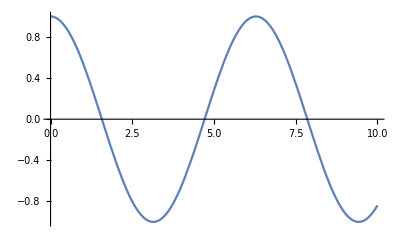

```mathematica
Plot[Cos[η],{η,0,10}]
```

```mathematica
ϕeqnηsmallμ
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
Simplify[%+(%%)/2]
Simplify[Bprimeeqnsmallμ1/.κ->(4 M^3)^-1]
%/.V[ϕ[η]]->1/2 ϕ'[η]-Wbar[ϕ[η]]^2/.λ[ϕ[η]]->0//Simplify
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

(λ[ϕ[η]]+ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

(2 V[ϕ[η]]+2 λ[ϕ[η]]+48 M^3 A'[η]^2+ϕ'[η]^2+24 M^3 A''[η])/(48 M^3)

(2 V[ϕ[η]]+2 λ[ϕ[η]]+48 M^3 B'[η]^2+ϕ'[η]^2-24 M^3 B''[η])/(48 M^3)

(-2 Wbar[ϕ[η]]^2+48 M^3 B'[η]^2+ϕ'[η]+ϕ'[η]^2-24 M^3 B''[η])/(48 M^3)

```mathematica
DSolve[B''[η]== 2 B'[η]^2-W[η]^2,B[η],η]
```

$Aborted

```mathematica
W[ϕ[η]]=(24 M^3)/L-ϵ/L ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/8(D[W[ϕ[η]],ϕ[η]])^2-1/(24 M^3)W[ϕ[η]]^2]
Expand[VW[ϕ[η]]]
ϕW'[η]=1/2 D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]]
Aofη=A[η]/.Aofηsol[[1]]
```

(24 M^3)/L-(ϵ ϕ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ϕ[η]^2+ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ϕ[η]^2)/L^2+(ϵ^2 ϕ[η]^2)/(2 L^2)-(ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(ϵ ϕ[η])/L

(-24+(ϵ ϕ[η]^2)/M^3)/(24 L)

{ϕ[η]→ⅇ^(-(ϵ η)/L) C[1]}

{{A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]}}

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
-η/L-(ⅇ^(-(2 ϵ Abs[η])/L) C[1]^2)/(48 M^3)+C[2]/.η->-η
```

```mathematica
η/L+(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]
D[%,η]
D[%,η]
```

η/L+(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

1/L-(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3)

(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)

```mathematica
-Aofη/.η->-η
D[%,η]
D[%,η]
Aofη
D[%,η]
D[%,η]
```

-η/L+(ⅇ^((2 ϵ η)/L) C[1]^2)/(48 M^3)-C[2]

-1/L+(ⅇ^((2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3)

(ⅇ^((2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3)

-(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)

```mathematica
Beqn =Expand[B''[η]==2  B'[η]^2 -D[Aofη,{η,2}]-2 D[Aofη,{η,1}]^2]
DSolve[%/.ϵ->0,B[η],η]
```

B''[η]==-2/L^2+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(6 L^2 M^3)+(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)-(ⅇ^(-(4 ϵ η)/L) ϵ^2 C[1]^4)/(288 L^2 M^6)+2 B'[η]^2

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]}}

```mathematica
Bnsol=NDSolve[{-B''[η]+2  B'[η]^2==0.2 - 0.001 E^(-0.002 η)+ 0.001 E^(-0.004 η),B'[0]==-0.002,B[0]==0},B,{η,0,100}]
```

{{B→InterpolatingFunction[…]}}

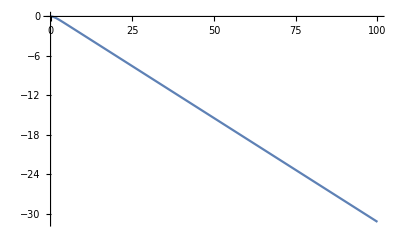

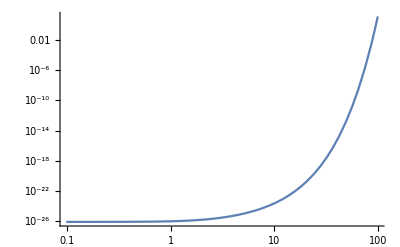

```mathematica
Plot[(B/.Bnsol[[1]])[η],{η,0,100}]
LogLogPlot[E^(-60-2(B/.Bnsol[[1]])[η]),{η,0,100},PlotRange->All]
```

```mathematica
12 24
```

288

```mathematica
Bsoln0=DSolve[B''[η]==-2/l^2+2 B'[η]^2,B[η],η]
```

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]}}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+(C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]) B'[η],B[η],η][[1]]
```

{B[η]→C[4]+(ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) C[3]+ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) 1/(6 L^2 M^3)ⅇ^(-(2 ϵ K[1])/L-C[2] K[1]+1/4 l (l C[1]+(2 K[1])/l) Log[Cosh[l C[1]+(2 K[1])/l]]+1/8 l (-((l C[1]+(2 K[1])/l) (l C[1]+(2 K[1])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[1])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[1])/l))])) (-2 ϵ C[1]^2-ϵ^2 C[1]^2)K[1]1K[2])K[2]1η}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+2 B'[η]^2,B[η],η]
```

{{B[η]→C[3]+-(((2 √(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselK[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2))/(√3 L M^(3/2))-1/(√3 L M^(3/2))√(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselI[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2) C[2])/(2 (2 BesselK[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)]+BesselI[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] C[2])))K[1]1η}}

```mathematica
Beqn/.ϵ->0
```

B'[η]==2/L^2+2 B[η]^2

```mathematica
Plot[E^(-2(C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]))/.{C[1]->2,C[2]->2,L->1},{η,0,100},PlotRange->All]
```

-Graphics-

#### Expand in small μ/p^2 - NTLO Better Ansatz

```mathematica
Clear[gη]

gη ={{E^(2A[η])-3 μ/l^2 E^(-2A[η]+2 B[η]),0,0,0,0},{0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 B[η]),0,0,0},{0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 B[η]),0,0},{0,0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 B[η]),0},{0,0,0,0,-1}}
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm;
Rη = Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]];
RTηsmallμ0//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]];
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 B[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

{{ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]+2 B[η]) μ)/l^2,0,0,0,0},{0,-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 B[η]) μ)/l^2,0,0,0},{0,0,-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 B[η]) μ)/l^2,0,0},{0,0,0,-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 B[η]) μ)/l^2,0},{0,0,0,0,-1}}

(ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]+2 B[η]) μ)/l^2 | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 B[η]) μ)/l^2 | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 B[η]) μ)/l^2 | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 B[η]) μ)/l^2 | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 A[η]) (ⅇ^(4 A[η]) l^2-3 ⅇ^(2 B[η]) μ) (ⅇ^(4 A[η]) l^2-ⅇ^(2 B[η]) μ)^3)/l^8

4 (5 A'[η]^2+2 A''[η])

(12 ⅇ^(-4 A[η]+4 B[η]) ϵ (2 A'[η]^2+3 A'[η] B'[η]-2 B'[η]^2+2 A''[η]-B''[η]))/l^2

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

((3 ⅇ^(-2 A[η]+2 B[η]) μ (6 A'[η]^2-4 A'[η] B'[η]+2 B'[η]^2+A''[η]+B''[η]))/l^2 | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (6 A'[η]^2-20 A'[η] B'[η]+10 B'[η]^2-7 A''[η]+5 B''[η]))/l^2 | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (6 A'[η]^2-20 A'[η] B'[η]+10 B'[η]^2-7 A''[η]+5 B''[η]))/l^2 | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (6 A'[η]^2-20 A'[η] B'[η]+10 B'[η]^2-7 A''[η]+5 B''[η]))/l^2 | 0
0 | 0 | 0 | 0 | (18 ⅇ^(-4 A[η]+2 B[η]) μ A'[η] (2 A'[η]-B'[η]))/l^2)

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]];
ϕeqnηsmallμ=Normal[Series[ϕeqnη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-(6 ⅇ^(-4 A[η]+4 B[η]) ϵ (2 A'[η]-B'[η]) ϕ'[η])/l^2-ϕ''[η]

```mathematica
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]];
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 B[η])
```

{{1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0,0},{0,-1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0},{0,0,-1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0},{0,0,0,-1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0},{0,0,0,0,-V[ϕ[η]]+1/2 ϕ'[η]^2}}

{{-(3 ⅇ^(-2 A[η]+2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0,0},{0,(ⅇ^(-2 A[η]+2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0},{0,0,(ⅇ^(-2 A[η]+2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0},{0,0,0,(ⅇ^(-2 A[η]+2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0},{0,0,0,0,0}}

```mathematica
Simplify[gη.Normal[Series[Inverse[gη],{μ,0,1}]]]
```

{{1-(9 ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0,0,0,0},{0,1-(ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0,0,0},{0,0,1-(ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0,0},{0,0,0,1-(ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0},{0,0,0,0,1}}

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=Simplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-1/2 κ ϕ'[η]^2)

((3 ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-8 A'[η] B'[η]+4 B'[η]^2+κ ϕ'[η]^2+2 A''[η]+2 B''[η]))/(2 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-40 A'[η] B'[η]+20 B'[η]^2+κ ϕ'[η]^2-14 A''[η]+10 B''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-40 A'[η] B'[η]+20 B'[η]^2+κ ϕ'[η]^2-14 A''[η]+10 B''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-40 A'[η] B'[η]+20 B'[η]^2+κ ϕ'[η]^2-14 A''[η]+10 B''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | (18 ⅇ^(-4 A[η]+2 B[η]) μ A'[η] (2 A'[η]-B'[η]))/l^2)

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ[η]]+ϕ'[η]^2)+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
EFEηsmallμ1//MatrixForm
```

((3 ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-8 A'[η] B'[η]+4 B'[η]^2+κ ϕ'[η]^2+2 A''[η]+2 B''[η]))/(2 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-40 A'[η] B'[η]+20 B'[η]^2+κ ϕ'[η]^2-14 A''[η]+10 B''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-40 A'[η] B'[η]+20 B'[η]^2+κ ϕ'[η]^2-14 A''[η]+10 B''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]+2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-40 A'[η] B'[η]+20 B'[η]^2+κ ϕ'[η]^2-14 A''[η]+10 B''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | (18 ⅇ^(-4 A[η]+2 B[η]) μ A'[η] (2 A'[η]-B'[η]))/l^2)

```mathematica
Simplify[EFEηsmallμ1[[1,1]](2 l^2)/(3μ)E^(2 A[η]-2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
Simplify[%/.{B'[η]->A'[η] +c[η],B''[η]->A''[η]+c''[η]}]
Solve[%==0,B''[η]]
```

-8 A'[η] B'[η]+4 B'[η]^2-4 A''[η]+2 B''[η]

2 (2 c[η]^2-2 A'[η]^2-A''[η]+c''[η])

{}

```mathematica
Simplify[-EFEηsmallμ1[[2,2]](2 l^2)/μ E^(2 A[η]-2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
Simplify[%/.{B'[η]->A'[η] +c[η],B''[η]->A''[η]+c''[η]}]
Solve[%==0,B''[η]]
```

10 (-4 A'[η] B'[η]+2 B'[η]^2-2 A''[η]+B''[η])

10 (2 c[η]^2-2 A'[η]^2-A''[η]+c''[η])

{}

```mathematica
First[{}]
```

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
BprimeSolsmallμ1=Simplify[Solve[EFEηsmallμ1[[1,1]]==0,B'[η]][[2]]]
BprimeprimeSolsmallμ1=Simplify[Solve[(Simplify[EFEηsmallμ1[[1,1]]/.BprimeSolsmallμ1])==0,B''[η]][[1]]];
Bprimeprimeeqnsmallμ1 =FullSimplify[B''[η]-(B''[η]/.BprimeprimeSolsmallμ1)]
Simplify[EFEηsmallμ1/.BprimeprimeSolsmallμ1];
Bprimeeqnsmallμ1 =Simplify[B'[η]^2-(B'[η]^2/.BprimeSolsmallμ1/.BprimeprimeSolsmallμ1)/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0]
```

{B'[η]→A'[η]+1/2 √(-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-8 A'[η]^2-κ ϕ'[η]^2-2 A''[η]-2 B''[η])}

0

1/6 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+6 B'[η]^2+κ ϕ'[η]^2-√(κ (-2 V[ϕ[η]]+ϕ'[η]^2)) √(-2 κ V[ϕ[η]]-4 κ λ[ϕ[η]]-3 κ ϕ'[η]^2-6 B''[η])+3 B''[η])

```mathematica
Simplify[DSolve[B''[η]==C + 2 B'[η]^2,B[η],η][[1]]]
```

{B[η]→C[2]-1/2 Log[Cos[√2 √C (η+C[1])]]}

```mathematica
Plot[Cos[η],{η,0,10}]
```

-Graphics-

```mathematica
ϕeqnηsmallμ
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
Expand[Bprimeeqnsmallμ1/.κ->(4 M^3)^-1]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

(λ[ϕ[η]]+ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

V[ϕ[η]]/(24 M^3)+λ[ϕ[η]]/(24 M^3)+B'[η]^2+ϕ'[η]^2/(48 M^3)-B''[η]/2

```mathematica
W[ϕ[η]]=(24 M^3)/L-ϵ/L ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/8(D[W[ϕ[η]],ϕ[η]])^2-1/(24 M^3)W[ϕ[η]]^2]
Expand[VW[ϕ[η]]]
ϕW'[η]=1/2 D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]]
Aofη=A[η]/.Aofηsol[[1]]
```

(24 M^3)/L-(ϵ ϕ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ϕ[η]^2+ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ϕ[η]^2)/L^2+(ϵ^2 ϕ[η]^2)/(2 L^2)-(ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(ϵ ϕ[η])/L

(-24+(ϵ ϕ[η]^2)/M^3)/(24 L)

{ϕ[η]→ⅇ^(-(ϵ η)/L) C[1]}

{{A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]}}

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
Beqn =Expand[B''[η]==2  B'[η]^2 -D[Aofη,{η,2}]-2 D[Aofη,{η,1}]^2]
DSolve[%/.ϵ->0,B[η],η]
```

B''[η]==-2/L^2+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(6 L^2 M^3)+(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)-(ⅇ^(-(4 ϵ η)/L) ϵ^2 C[1]^4)/(288 L^2 M^6)+2 B'[η]^2

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]}}

```mathematica
12 24
```

288

```mathematica
Bsoln0=DSolve[B''[η]==-2/l^2+2 B'[η]^2,B[η],η]
```

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]}}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+(C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]) B'[η],B[η],η][[1]]
```

{B[η]→C[4]+(ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) C[3]+ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) 1/(6 L^2 M^3)ⅇ^(-(2 ϵ K[1])/L-C[2] K[1]+1/4 l (l C[1]+(2 K[1])/l) Log[Cosh[l C[1]+(2 K[1])/l]]+1/8 l (-((l C[1]+(2 K[1])/l) (l C[1]+(2 K[1])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[1])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[1])/l))])) (-2 ϵ C[1]^2-ϵ^2 C[1]^2)K[1]1K[2])K[2]1η}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+2 B'[η]^2,B[η],η]
```

{{B[η]→C[3]+-(((2 √(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselK[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2))/(√3 L M^(3/2))-1/(√3 L M^(3/2))√(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselI[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2) C[2])/(2 (2 BesselK[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)]+BesselI[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] C[2])))K[1]1η}}

```mathematica
Beqn/.ϵ->0
```

B'[η]==2/L^2+2 B[η]^2

```mathematica
Plot[E^(-2(C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]))/.{C[1]->2,C[2]->2,L->1},{η,0,100},PlotRange->All]
```

-Graphics-

#### Expand in small μ/p^2 - NTLO diff t and x ansatzes

```mathematica
Clear[gη]

gη ={{E^(2A[η])-3 μ/l^2 E^(-2A[η]+2 B[η]),0,0,0,0},{0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 c[η]),0,0,0},{0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 c[η]),0,0},{0,0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 c[η]),0},{0,0,0,0,-1}}
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm;
Rη = Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]];
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]
RTηsmallμ0=Normal[Series[RTη,{μ,0,0}]];
RTηsmallμ1=Simplify[Normal[Series[RTη,{μ,0,1}]]-RTηsmallμ0];
RTηsmallμ0//MatrixForm
RTηsmallμ1//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη,{μ,0,0}]]];
GTηsmallμ1=Simplify[Normal[Series[GTη,{μ,0,1}]]-GTηsmallμ0];
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

{{ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]+2 B[η]) μ)/l^2,0,0,0,0},{0,-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 c[η]) μ)/l^2,0,0,0},{0,0,-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 c[η]) μ)/l^2,0,0},{0,0,0,-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 c[η]) μ)/l^2,0},{0,0,0,0,-1}}

(ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]+2 B[η]) μ)/l^2 | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 c[η]) μ)/l^2 | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 c[η]) μ)/l^2 | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η])+(ⅇ^(-2 A[η]+2 c[η]) μ)/l^2 | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 A[η]) (ⅇ^(4 A[η]) l^2-3 ⅇ^(2 B[η]) μ) (ⅇ^(4 A[η]) l^2-ⅇ^(2 c[η]) μ)^3)/l^8

(6 ⅇ^(-4 A[η]+2 B[η]) ϵ (2 (ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]^2-2 ⅇ^(2 B[η]) B'[η]^2-2 ⅇ^(2 c[η]) c'[η]^2+3 A'[η] (ⅇ^(2 B[η]) B'[η]+ⅇ^(2 c[η]) c'[η])+2 ⅇ^(2 B[η]) A''[η]+2 ⅇ^(2 c[η]) A''[η]-ⅇ^(2 B[η]) B''[η]-ⅇ^(2 c[η]) c''[η]))/l^2

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-(3 ⅇ^(-2 A[η]) μ (2 (ⅇ^(2 B[η])-ⅇ^(2 c[η])) A'[η]^2+A'[η] (-3 ⅇ^(2 B[η]) B'[η]+ⅇ^(2 c[η]) c'[η])+ⅇ^(2 B[η]) (2 B'[η]^2-A''[η]+B''[η])))/l^2 | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]) μ (2 (3 ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]^2+A'[η] (-3 ⅇ^(2 B[η]) B'[η]+ⅇ^(2 c[η]) c'[η])+ⅇ^(2 c[η]) (-2 c'[η]^2+A''[η]-c''[η])))/l^2 | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]) μ (2 (3 ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]^2+A'[η] (-3 ⅇ^(2 B[η]) B'[η]+ⅇ^(2 c[η]) c'[η])+ⅇ^(2 c[η]) (-2 c'[η]^2+A''[η]-c''[η])))/l^2 | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]) μ (2 (3 ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]^2+A'[η] (-3 ⅇ^(2 B[η]) B'[η]+ⅇ^(2 c[η]) c'[η])+ⅇ^(2 c[η]) (-2 c'[η]^2+A''[η]-c''[η])))/l^2 | 0
0 | 0 | 0 | 0 | (3 ⅇ^(-4 A[η]) μ (ⅇ^(2 B[η]) (4 A'[η]^2-6 A'[η] B'[η]+2 B'[η]^2-2 A''[η]+B''[η])+ⅇ^(2 c[η]) (4 A'[η]^2-6 A'[η] c'[η]+2 c'[η]^2-2 A''[η]+c''[η])))/l^2)

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

((3 ⅇ^(-2 A[η]) μ (6 ⅇ^(2 B[η]) A'[η]^2-4 ⅇ^(2 c[η]) A'[η] c'[η]+2 ⅇ^(2 c[η]) c'[η]^2+3 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+ⅇ^(2 c[η]) c''[η]))/l^2 | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]) μ (6 ⅇ^(2 c[η]) A'[η]^2+6 ⅇ^(2 B[η]) B'[η]^2+4 ⅇ^(2 c[η]) c'[η]^2-4 A'[η] (3 ⅇ^(2 B[η]) B'[η]+2 ⅇ^(2 c[η]) c'[η])-6 ⅇ^(2 B[η]) A''[η]-ⅇ^(2 c[η]) A''[η]+3 ⅇ^(2 B[η]) B''[η]+2 ⅇ^(2 c[η]) c''[η]))/l^2 | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]) μ (6 ⅇ^(2 c[η]) A'[η]^2+6 ⅇ^(2 B[η]) B'[η]^2+4 ⅇ^(2 c[η]) c'[η]^2-4 A'[η] (3 ⅇ^(2 B[η]) B'[η]+2 ⅇ^(2 c[η]) c'[η])-6 ⅇ^(2 B[η]) A''[η]-ⅇ^(2 c[η]) A''[η]+3 ⅇ^(2 B[η]) B''[η]+2 ⅇ^(2 c[η]) c''[η]))/l^2 | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]) μ (6 ⅇ^(2 c[η]) A'[η]^2+6 ⅇ^(2 B[η]) B'[η]^2+4 ⅇ^(2 c[η]) c'[η]^2-4 A'[η] (3 ⅇ^(2 B[η]) B'[η]+2 ⅇ^(2 c[η]) c'[η])-6 ⅇ^(2 B[η]) A''[η]-ⅇ^(2 c[η]) A''[η]+3 ⅇ^(2 B[η]) B''[η]+2 ⅇ^(2 c[η]) c''[η]))/l^2 | 0
0 | 0 | 0 | 0 | (9 ⅇ^(-4 A[η]) μ A'[η] (2 (ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]-ⅇ^(2 B[η]) B'[η]-ⅇ^(2 c[η]) c'[η]))/l^2)

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]];
ϕeqnηsmallμ=Normal[Series[ϕeqnη,{μ,0,1}]]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-(3 ⅇ^(-4 A[η]) μ (2 ⅇ^(2 B[η]) A'[η]+2 ⅇ^(2 c[η]) A'[η]-ⅇ^(2 B[η]) B'[η]-ⅇ^(2 c[η]) c'[η]) ϕ'[η])/l^2-ϕ''[η]

```mathematica
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]];
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 B[η])
```

{{1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0,0},{0,-1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0},{0,0,-1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0},{0,0,0,-1/2 ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0},{0,0,0,0,-V[ϕ[η]]+1/2 ϕ'[η]^2}}

{{-(3 ⅇ^(-2 A[η]+2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0,0},{0,(ⅇ^(-2 B[η]+2 (-A[η]+B[η]+c[η])) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0},{0,0,(ⅇ^(-2 B[η]+2 (-A[η]+B[η]+c[η])) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0},{0,0,0,(ⅇ^(-2 B[η]+2 (-A[η]+B[η]+c[η])) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0},{0,0,0,0,0}}

```mathematica
Simplify[gη.Normal[Series[Inverse[gη],{μ,0,1}]]]
```

{{1-(9 ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0,0,0,0},{0,1-(ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0,0,0},{0,0,1-(ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0,0},{0,0,0,1-(ⅇ^(-8 A[η]+4 B[η]) μ^2)/l^4,0},{0,0,0,0,1}}

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=Simplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-1/2 κ ϕ'[η]^2)

((3 ⅇ^(-2 A[η]) μ (ⅇ^(2 B[η]) κ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2)+2 (6 ⅇ^(2 B[η]) A'[η]^2-4 ⅇ^(2 c[η]) A'[η] c'[η]+2 ⅇ^(2 c[η]) c'[η]^2+3 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+ⅇ^(2 c[η]) c''[η])))/(2 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | (9 ⅇ^(-4 A[η]) μ A'[η] (2 (ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]-ⅇ^(2 B[η]) B'[η]-ⅇ^(2 c[η]) c'[η]))/l^2)

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ[η]]+ϕ'[η]^2)+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
EFEηsmallμ1//MatrixForm
```

((3 ⅇ^(-2 A[η]) μ (ⅇ^(2 B[η]) κ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2)+2 (6 ⅇ^(2 B[η]) A'[η]^2-4 ⅇ^(2 c[η]) A'[η] c'[η]+2 ⅇ^(2 c[η]) c'[η]^2+3 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+ⅇ^(2 c[η]) c''[η])))/(2 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | (9 ⅇ^(-4 A[η]) μ A'[η] (2 (ⅇ^(2 B[η])+ⅇ^(2 c[η])) A'[η]-ⅇ^(2 B[η]) B'[η]-ⅇ^(2 c[η]) c'[η]))/l^2)

```mathematica
Simplify[EFEηsmallμ1[[1,1]](2 l^2)/(3μ)E^(2 A[η]-2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
Simplify[%/.{D[c[η]->2 A[η],η],D[c[η]->2 A[η],{η,2}]}]
Simplify[-EFEηsmallμ1[[2,2]](2 l^2)/μ E^(2 A[η]-2c[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
Simplify[%/.{D[c[η]->2 A[η],η],D[c[η]->2 A[η],{η,2}]}]
(*Simplify[%/.{B'[η]->A'[η] +c[η],B''[η]->A''[η]+c''[η]}]
Solve[%==0,B''[η]]*)
```

ⅇ^(-2 B[η]+2 c[η]) (-8 A'[η] c'[η]+4 c'[η]^2-4 A''[η]+2 c''[η])

0

2 (6 ⅇ^(2 B[η]-2 c[η]) B'[η]^2+A'[η] (-12 ⅇ^(2 B[η]-2 c[η]) B'[η]-8 c'[η])+4 c'[η]^2-4 A''[η]-6 ⅇ^(2 B[η]-2 c[η]) A''[η]+3 ⅇ^(2 B[η]-2 c[η]) B''[η]+2 c''[η])

-6 ⅇ^(2 B[η]-2 c[η]) (4 A'[η] B'[η]-2 B'[η]^2+2 A''[η]-B''[η])

```mathematica
Simplify[-EFEηsmallμ1[[2,2]](2 l^2)/(3μ)E^(2 A[η]-2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
Simplify[%/.{B'[η]->A'[η] +c[η],B''[η]->A''[η]+c''[η]}]
Solve[%==0,B''[η]]
```

-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-12 A'[η]^2-κ ϕ'[η]^2-6 A''[η]+1/3 ⅇ^(-2 B[η]) (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]+4 ⅇ^(2 c[η]) c''[η])

1/3 ⅇ^(-2 B[η]) (12 ⅇ^(2 B[η]) c[η]^2+2 (-3 ⅇ^(2 B[η])+ⅇ^(2 c[η])) κ V[ϕ[η]]-6 ⅇ^(2 B[η]) κ λ[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]-48 ⅇ^(2 B[η]) A'[η]^2+12 ⅇ^(2 c[η]) A'[η]^2-16 ⅇ^(2 c[η]) A'[η] c'[η]+8 ⅇ^(2 c[η]) c'[η]^2-3 ⅇ^(2 B[η]) κ ϕ'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-24 ⅇ^(2 B[η]) A''[η]-2 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) c''[η]+4 ⅇ^(2 c[η]) c''[η])

{}

```mathematica
Simplify[EFEηsmallμ1[[1,1]](2 l^2)/(3μ)E^(2 A[η]-2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
cppsol=Solve[%==0,c''[η]][[1]]
Simplify[Simplify[FullSimplify[EFEηsmallμ1[[2,2]](2 l^2)/μ E^(2 A[η]-2B[η])]+ⅇ^(-2 B[η]+2 c[η]) 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]/.cppsol]
bppsol=Solve[%==0,B''[η]][[1]]
```

ⅇ^(-2 B[η]+2 c[η]) (-8 A'[η] c'[η]+4 c'[η]^2-4 A''[η]+2 c''[η])

{c''[η]→2 (2 A'[η] c'[η]-c'[η]^2+A''[η])}

-6 (-4 A'[η] B'[η]+2 B'[η]^2-2 A''[η]+B''[η])

{B''[η]→2 (2 A'[η] B'[η]-B'[η]^2+A''[η])}

```mathematica
Simplify[FullSimplify[EFEηsmallμ1[[2,2]]]/.cppsol]
```

-(ⅇ^(-2 A[η]) μ (2 ⅇ^(2 c[η]) κ V[ϕ[η]]+2 ⅇ^(2 c[η]) κ λ[ϕ[η]]+12 ⅇ^(2 c[η]) A'[η]^2-24 ⅇ^(2 B[η]) A'[η] B'[η]+12 ⅇ^(2 B[η]) B'[η]^2+ⅇ^(2 c[η]) κ ϕ'[η]^2-12 ⅇ^(2 B[η]) A''[η]+6 ⅇ^(2 c[η]) A''[η]+6 ⅇ^(2 B[η]) B''[η]))/(2 l^2)

```mathematica
Simplify[-FullSimplify[EFEηsmallμ1[[2,2]](2 l^2)/μ E^(2 A[η]-2B[η])]- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
```

ⅇ^(-2 B[η]+2 c[η]) (-8 A'[η] c'[η]+4 c'[η]^2-4 A''[η]+2 c''[η])

{c''[η]→2 (2 A'[η] c'[η]-c'[η]^2+A''[η])}

-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-12 A'[η]^2-κ ϕ'[η]^2-6 A''[η]-6 (4 A'[η] B'[η]-2 B'[η]^2+2 A''[η]-B''[η])+ⅇ^(-2 B[η]+2 c[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2-16 A'[η] c'[η]+8 c'[η]^2+κ ϕ'[η]^2-2 A''[η]+4 c''[η])

```mathematica
First[{}]
```

First::nofirst: {} has zero length and no first element.

First[{}]

```mathematica
BprimeSolsmallμ1=Simplify[Solve[EFEηsmallμ1[[1,1]]==0,B'[η]][[2]]]
BprimeprimeSolsmallμ1=Simplify[Solve[(Simplify[EFEηsmallμ1[[1,1]]/.BprimeSolsmallμ1])==0,B''[η]][[1]]];
Bprimeprimeeqnsmallμ1 =FullSimplify[B''[η]-(B''[η]/.BprimeprimeSolsmallμ1)]
Simplify[EFEηsmallμ1/.BprimeprimeSolsmallμ1];
Bprimeeqnsmallμ1 =Simplify[B'[η]^2-(B'[η]^2/.BprimeSolsmallμ1/.BprimeprimeSolsmallμ1)/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0]
```

{B'[η]→A'[η]+1/2 √(-2 κ V[ϕ[η]]-2 κ λ[ϕ[η]]-8 A'[η]^2-κ ϕ'[η]^2-2 A''[η]-2 B''[η])}

0

1/6 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+6 B'[η]^2+κ ϕ'[η]^2-√(κ (-2 V[ϕ[η]]+ϕ'[η]^2)) √(-2 κ V[ϕ[η]]-4 κ λ[ϕ[η]]-3 κ ϕ'[η]^2-6 B''[η])+3 B''[η])

```mathematica
Simplify[DSolve[B''[η]==C + 2 B'[η]^2,B[η],η][[1]]]
```

{B[η]→C[2]-1/2 Log[Cos[√2 √C (η+C[1])]]}

```mathematica
Plot[Cos[η],{η,0,10}]
```

-Graphics-

```mathematica
ϕeqnηsmallμ
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
Expand[Bprimeeqnsmallμ1/.κ->(4 M^3)^-1]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

(λ[ϕ[η]]+ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

V[ϕ[η]]/(24 M^3)+λ[ϕ[η]]/(24 M^3)+B'[η]^2+ϕ'[η]^2/(48 M^3)-B''[η]/2

```mathematica
W[ϕ[η]]=(24 M^3)/L-ϵ/L ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/8(D[W[ϕ[η]],ϕ[η]])^2-1/(24 M^3)W[ϕ[η]]^2]
Expand[VW[ϕ[η]]]
ϕW'[η]=1/2 D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]]
Aofη=A[η]/.Aofηsol[[1]]
```

(24 M^3)/L-(ϵ ϕ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ϕ[η]^2+ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ϕ[η]^2)/L^2+(ϵ^2 ϕ[η]^2)/(2 L^2)-(ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(ϵ ϕ[η])/L

(-24+(ϵ ϕ[η]^2)/M^3)/(24 L)

{ϕ[η]→ⅇ^(-(ϵ η)/L) C[1]}

{{A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]}}

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
Beqn =Expand[B''[η]==2  B'[η]^2 -D[Aofη,{η,2}]-2 D[Aofη,{η,1}]^2]
DSolve[%/.ϵ->0,B[η],η]
```

B''[η]==-2/L^2+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(6 L^2 M^3)+(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)-(ⅇ^(-(4 ϵ η)/L) ϵ^2 C[1]^4)/(288 L^2 M^6)+2 B'[η]^2

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]}}

```mathematica
12 24
```

288

```mathematica
Bsoln0=DSolve[B''[η]==-2/l^2+2 B'[η]^2,B[η],η]
```

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]}}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+(C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]) B'[η],B[η],η][[1]]
```

{B[η]→C[4]+(ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) C[3]+ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) 1/(6 L^2 M^3)ⅇ^(-(2 ϵ K[1])/L-C[2] K[1]+1/4 l (l C[1]+(2 K[1])/l) Log[Cosh[l C[1]+(2 K[1])/l]]+1/8 l (-((l C[1]+(2 K[1])/l) (l C[1]+(2 K[1])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[1])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[1])/l))])) (-2 ϵ C[1]^2-ϵ^2 C[1]^2)K[1]1K[2])K[2]1η}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+2 B'[η]^2,B[η],η]
```

{{B[η]→C[3]+-(((2 √(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselK[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2))/(√3 L M^(3/2))-1/(√3 L M^(3/2))√(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselI[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2) C[2])/(2 (2 BesselK[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)]+BesselI[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] C[2])))K[1]1η}}

```mathematica
Beqn/.ϵ->0
```

B'[η]==2/L^2+2 B[η]^2

```mathematica
Plot[E^(-2(C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]))/.{C[1]->2,C[2]->2,L->1},{η,0,100},PlotRange->All]
```

-Graphics-

#### Expand in small μ/p^2 - NNTLO

Try converting to gaussian normal coordinate in AdS-S

```mathematica
pofη=Simplify[p[η]/.DSolve[D[p[η],η]==√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
```

(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(√2)

```mathematica
pofη/.η->-C[1]+a
```

(ⅇ^(-a/l) √(ⅇ^((4 a)/l)+l^2 μ))/(√2)

```mathematica
Simplify[p[η]/.DSolve[D[p[η],η]==-√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
%/.η->-C[1]
```

(√(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 C[1])/l)+ⅇ^((4 η)/l) l^2 μ)))/(√2)

(√(ⅇ^((4 C[1])/l)+ⅇ^(-(4 C[1])/l) l^2 μ))/(√2)

```mathematica
FullSimplify[PowerExpand[FullSimplify[Simplify[D[pofη,η]]/.η->ηofp]]]
```

(√(p^4-l^2 μ))/(l p)

```mathematica
ηofp=η/.Solve[pofη==p,η][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 μ))]

```mathematica
Simplify[E^(2/l ηofp)]
```

ⅇ^(-(2 C[1])/l) (p^2+√(p^4-l^2 μ))

```mathematica
pofη/.μ->E^(2(η+C[1])/l) ϵ
pofηsmallμ=Expand[Normal[PowerExpand[Series[%,{ϵ,0,1}]]]/.ϵ ->μ E^(-2(η+C[1])/l)]
```

(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)+ⅇ^((2 (η+C[1]))/l) l^2 ϵ))/(√2)

ⅇ^(η/l+C[1]/l)/(√2)+(ⅇ^(-(3 η)/l-(3 C[1])/l) l^2 μ)/(2 √2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 p^2 ϵ))]

```mathematica
η/.Solve[(pofη/.μ->ϵ p^2)==p,η][[4]]/.C[2]-> 0
Normal[PowerExpand[Series[√(p^2+√(p^4-l^2 p^2 ϵ)),{ϵ,0,1}]]]
ηofpsmallμ =Simplify[Normal[Series[-C[1]+l Log[%],{ϵ,0,1}]]]/.ϵ->μ/p^2
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 p^2 ϵ))]

√2 p-(l^2 ϵ)/(4 √2 p)

-(l^3 μ)/(8 p^4)-C[1]+1/2 l Log[2]+l Log[p]

```mathematica
FullSimplify[p[η]^2/l^2/.p[η]-> pofη]
gii=Simplify[%/.η-> l A[η] /.C[1]->l/2 Log[ 2]]
Simplify[p[η]^2/l^2-μ/p[η]^2/.p[η]-> pofη/.C[1]->l/2 Log[2]]
gtt=Simplify[%/.η-> l A[η] ]
```

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(2 l^2)

ⅇ^(2 A[η])/l^2+1/4 ⅇ^(-2 A[η]) μ

(ⅇ^(-(2 η)/l) (-4 ⅇ^((4 η)/l)+l^2 μ)^2)/(4 l^2 (4 ⅇ^((4 η)/l)+l^2 μ))

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+l^2 μ)^2)/(4 l^2 (4 ⅇ^(4 A[η])+l^2 μ))

```mathematica
gii/.μ->ϵ E^(-2 A[η])
giismallμ=Normal[Simplify[Series[%,{ϵ,0,1}]]]/.ϵ->E^(4 A[η]-2 B[η])μ
gtt/.μ->ϵ E^(-2 A[η])
gttsmallμ=Normal[Simplify[Series[%,{ϵ,0,1}]]]/.ϵ->E^(4 A[η]-2 B[η])μ
```

ⅇ^(2 A[η])/l^2+1/4 ⅇ^(-4 A[η]) ϵ

ⅇ^(2 A[η])/l^2+1/4 ⅇ^(-2 B[η]) μ

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+ⅇ^(-2 A[η]) l^2 ϵ)^2)/(4 l^2 (4 ⅇ^(4 A[η])+ⅇ^(-2 A[η]) l^2 ϵ))

ⅇ^(2 A[η])/l^2-3/4 ⅇ^(-2 B[η]) μ

```mathematica
gii/.μ->ϵ E^(-2 A[η])
giismallμ2=Normal[Simplify[Series[%,{ϵ,0,2}]]]/.ϵ->E^(4 A[η]-2 B[η])μ/.-2A[η]-4B[η]->-6 c[η]
gtt/.μ->ϵ E^(-2 A[η])
gttsmallμ2=Normal[Simplify[Series[%,{ϵ,0,2}]]]/.ϵ->E^(4 A[η]-2 B[η])μ/.-2A[η]-4B[η]->-6 c[η]
```

ⅇ^(2 A[η])/l^2+1/4 ⅇ^(-4 A[η]) ϵ

ⅇ^(2 A[η])/l^2+1/4 ⅇ^(-2 B[η]) μ

(ⅇ^(-2 A[η]) (-4 ⅇ^(4 A[η])+ⅇ^(-2 A[η]) l^2 ϵ)^2)/(4 l^2 (4 ⅇ^(4 A[η])+ⅇ^(-2 A[η]) l^2 ϵ))

ⅇ^(2 A[η])/l^2-3/4 ⅇ^(-2 B[η]) μ+1/4 ⅇ^(-6 c[η]) l^2 μ^2

```mathematica
Simplify[Series[gii,{μ,0,1}]]
Simplify[Series[gtt,{μ,0,1}]]
```

ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)+O[μ]^2

ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/(4 l^2)+O[μ]^2

```mathematica
Clear[gη]

gη ={{gttsmallμ2,0,0,0,0},{0,-giismallμ2,0,0,0},{0,0,-giismallμ2,0,0},{0,0,0,-giismallμ2,0},{0,0,0,0,-1}}
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]];
RTηsmallμ0//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]];
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 B[η]);
GTηsmallμ2=Simplify[Normal[Series[GTη,{μ,0,2}]]-GTηsmallμ1-GTηsmallμ0];
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
GTηsmallμ2//MatrixForm
```

{{ⅇ^(2 A[η])/l^2-3/4 ⅇ^(-2 B[η]) μ+1/4 ⅇ^(-6 c[η]) l^2 μ^2,0,0,0,0},{0,-ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ,0,0,0},{0,0,-ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ,0,0},{0,0,0,-ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ,0},{0,0,0,0,-1}}

(ⅇ^(2 A[η])/l^2-3/4 ⅇ^(-2 B[η]) μ+1/4 ⅇ^(-6 c[η]) l^2 μ^2 | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η])/l^2-1/4 ⅇ^(-2 B[η]) μ | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 B[η]-6 c[η]) (4 ⅇ^(2 (A[η]+B[η]))+l^2 μ)^3 (4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2))/(256 l^8)

((2 ⅇ^(2 A[η]) A'[η]^2)/l^2-(ⅇ^(-2 (B[η]+3 c[η])) (4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η]+3 l^2 μ (ⅇ^(6 c[η]) B'[η]-ⅇ^(2 B[η]) l^2 μ c'[η]))^2)/(4 l^2 (4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2))+(3 (4 ⅇ^(2 (A[η]+B[η])) A'[η]-l^2 μ B'[η]) ((ⅇ^(2 A[η]) A'[η])/l^2+3/4 μ (ⅇ^(-2 B[η]) B'[η]-ⅇ^(-6 c[η]) l^2 μ c'[η])))/(4 ⅇ^(2 (A[η]+B[η]))+l^2 μ)+(ⅇ^(2 A[η]) A''[η])/l^2+3/4 μ (-2 ⅇ^(-2 B[η]) B'[η]^2+6 ⅇ^(-6 c[η]) l^2 μ c'[η]^2+ⅇ^(-2 B[η]) B''[η]-ⅇ^(-6 c[η]) l^2 μ c''[η]) | 0 | 0 | 0 | 0
0 | -(2 ⅇ^(2 A[η]) A'[η]^2)/l^2-1/2 ⅇ^(-2 B[η]) μ B'[η]^2-(ⅇ^(-2 B[η]) (-4 ⅇ^(2 (A[η]+B[η])) A'[η]+l^2 μ B'[η])^2)/(4 l^2 (4 ⅇ^(2 (A[η]+B[η]))+l^2 μ))+((-(ⅇ^(2 A[η]) A'[η])/l^2+1/4 ⅇ^(-2 B[η]) μ B'[η]) (4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η]+3 l^2 μ (ⅇ^(6 c[η]) B'[η]-ⅇ^(2 B[η]) l^2 μ c'[η])))/(4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2)-(ⅇ^(2 A[η]) A''[η])/l^2+1/4 ⅇ^(-2 B[η]) μ B''[η] | 0 | 0 | 0
0 | 0 | -(2 ⅇ^(2 A[η]) A'[η]^2)/l^2-1/2 ⅇ^(-2 B[η]) μ B'[η]^2-(ⅇ^(-2 B[η]) (-4 ⅇ^(2 (A[η]+B[η])) A'[η]+l^2 μ B'[η])^2)/(4 l^2 (4 ⅇ^(2 (A[η]+B[η]))+l^2 μ))+((-(ⅇ^(2 A[η]) A'[η])/l^2+1/4 ⅇ^(-2 B[η]) μ B'[η]) (4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η]+3 l^2 μ (ⅇ^(6 c[η]) B'[η]-ⅇ^(2 B[η]) l^2 μ c'[η])))/(4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2)-(ⅇ^(2 A[η]) A''[η])/l^2+1/4 ⅇ^(-2 B[η]) μ B''[η] | 0 | 0
0 | 0 | 0 | -(2 ⅇ^(2 A[η]) A'[η]^2)/l^2-1/2 ⅇ^(-2 B[η]) μ B'[η]^2-(ⅇ^(-2 B[η]) (-4 ⅇ^(2 (A[η]+B[η])) A'[η]+l^2 μ B'[η])^2)/(4 l^2 (4 ⅇ^(2 (A[η]+B[η]))+l^2 μ))+((-(ⅇ^(2 A[η]) A'[η])/l^2+1/4 ⅇ^(-2 B[η]) μ B'[η]) (4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η]+3 l^2 μ (ⅇ^(6 c[η]) B'[η]-ⅇ^(2 B[η]) l^2 μ c'[η])))/(4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2)-(ⅇ^(2 A[η]) A''[η])/l^2+1/4 ⅇ^(-2 B[η]) μ B''[η] | 0
0 | 0 | 0 | 0 | -(3 (8 ⅇ^(2 (A[η]+B[η])) (2 ⅇ^(2 (A[η]+B[η]))+l^2 μ) A'[η]^2+8 ⅇ^(2 (A[η]+B[η])) l^2 μ A'[η] B'[η]+l^2 μ (8 ⅇ^(2 (A[η]+B[η]))+l^2 μ) B'[η]^2+(4 ⅇ^(2 (A[η]+B[η]))+l^2 μ) (4 ⅇ^(2 (A[η]+B[η])) A''[η]-l^2 μ B''[η])))/((4 ⅇ^(2 (A[η]+B[η]))+l^2 μ)^2)-(-((2 ⅇ^(2 B[η]) l^4 μ^2 B'[η]-18 ⅇ^(6 c[η]) l^2 μ c'[η]+8 ⅇ^(2 (A[η]+B[η]+3 c[η])) (A'[η]+B'[η]+3 c'[η])) (4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η]+3 l^2 μ (ⅇ^(6 c[η]) B'[η]-ⅇ^(2 B[η]) l^2 μ c'[η])))+(4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η]+3 l^2 μ (ⅇ^(6 c[η]) B'[η]-ⅇ^(2 B[η]) l^2 μ c'[η]))^2+(4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2) (8 ⅇ^(2 (A[η]+B[η]+3 c[η])) A'[η] (A'[η]+B'[η]+3 c'[η])+4 ⅇ^(2 (A[η]+B[η]+3 c[η])) A''[η]+3 l^2 μ (2 (3 ⅇ^(6 c[η])-ⅇ^(2 B[η]) l^2 μ) B'[η] c'[η]+ⅇ^(6 c[η]) B''[η]-ⅇ^(2 B[η]) l^2 μ c''[η])))/((4 ⅇ^(2 (A[η]+B[η]+3 c[η]))-3 ⅇ^(6 c[η]) l^2 μ+ⅇ^(2 B[η]) l^4 μ^2)^2))

4 (5 A'[η]^2+2 A''[η])

0

((ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0 | 0
0 | -(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0
0 | 0 | -(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0 | 0
0 | 0 | 0 | -(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]))/l^2 | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-(3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0 | 0
0 | (3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0 | 0 | 0
0 | 0 | (3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0 | 0
0 | 0 | 0 | (3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]))/l^2 | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(3/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0 | 0 | 0 | 0
0 | 1/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0 | 0 | 0
0 | 0 | 1/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0 | 0
0 | 0 | 0 | 1/4 ⅇ^(-2 B[η]) μ (8 A'[η]^2-2 B'[η]^2+4 A''[η]+B''[η]) | 0
0 | 0 | 0 | 0 | 0)

(-3/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])+ⅇ^(6 c[η])) A'[η]^2-2 ⅇ^(6 c[η]) B'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]+ⅇ^(6 c[η]) A''[η]+ⅇ^(6 c[η]) B''[η]) | 0 | 0 | 0 | 0
0 | -1/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])-ⅇ^(6 c[η])) A'[η]^2+8 ⅇ^(6 c[η]) A'[η] B'[η]+10 ⅇ^(6 c[η]) B'[η]^2-18 ⅇ^(2 A[η]+4 B[η]) c'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]-3 ⅇ^(6 c[η]) A''[η]-3 ⅇ^(6 c[η]) B''[η]+3 ⅇ^(2 A[η]+4 B[η]) c''[η]) | 0 | 0 | 0
0 | 0 | -1/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])-ⅇ^(6 c[η])) A'[η]^2+8 ⅇ^(6 c[η]) A'[η] B'[η]+10 ⅇ^(6 c[η]) B'[η]^2-18 ⅇ^(2 A[η]+4 B[η]) c'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]-3 ⅇ^(6 c[η]) A''[η]-3 ⅇ^(6 c[η]) B''[η]+3 ⅇ^(2 A[η]+4 B[η]) c''[η]) | 0 | 0
0 | 0 | 0 | -1/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])-ⅇ^(6 c[η])) A'[η]^2+8 ⅇ^(6 c[η]) A'[η] B'[η]+10 ⅇ^(6 c[η]) B'[η]^2-18 ⅇ^(2 A[η]+4 B[η]) c'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]-3 ⅇ^(6 c[η]) A''[η]-3 ⅇ^(6 c[η]) B''[η]+3 ⅇ^(2 A[η]+4 B[η]) c''[η]) | 0
0 | 0 | 0 | 0 | -3/8 ⅇ^(-4 A[η]-4 B[η]-6 c[η]) l^4 μ^2 ((2 ⅇ^(2 A[η]+4 B[η])-5 ⅇ^(6 c[η])) A'[η]^2+ⅇ^(6 c[η]) B'[η]^2+A'[η] (-4 ⅇ^(6 c[η]) B'[η]+6 ⅇ^(2 A[η]+4 B[η]) c'[η])))

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]];
ϕeqnηsmallμ=Normal[Series[ϕeqnη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]
ϕeqnηsmallμ2=Simplify[Normal[Series[ϕeqnη,{μ,0,2}]]-ϕeqnηsmallμ]
Simplify[ϕeqnηsmallμ2/.{B'[η]->-A'[η],B''[η]->-A''[η]}]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

1/4 ⅇ^(-4 A[η]-4 B[η]-6 c[η]) l^4 μ^2 ((ⅇ^(2 A[η]+4 B[η])-3 ⅇ^(6 c[η])) A'[η]-3 ⅇ^(6 c[η]) B'[η]+3 ⅇ^(2 A[η]+4 B[η]) c'[η]) ϕ'[η]

1/4 ⅇ^(-2 (A[η]+3 c[η])) l^4 μ^2 (A'[η]+3 c'[η]) ϕ'[η]

```mathematica
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]];
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,0}]]
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 B[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 B[η])
TTηsmallμ2=Simplify[Simplify[Normal[Series[TTη,{μ,0,2}]]-TTηsmallμ1-TTηsmallμ0]]
```

{{(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0,0},{0,-(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0,0},{0,0,-(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0,0},{0,0,0,-(ⅇ^(2 A[η]) (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2))/(2 l^2),0},{0,0,0,0,-V[ϕ[η]]+1/2 ϕ'[η]^2}}

{{-3/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0,0},{0,-1/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0},{0,0,-1/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0},{0,0,0,-1/8 ⅇ^(-2 B[η]) μ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0},{0,0,0,0,0}}

{{1/8 ⅇ^(-6 c[η]) l^2 μ^2 (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2),0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=Simplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ2=Simplify[Simplify[GTηsmallμ2-κ TTηsmallμ2]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
EFEηsmallμ2//MatrixForm
```

(-(ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(2 A[η]) (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-1/2 κ ϕ'[η]^2)

(3/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0 | 0 | 0 | 0
0 | 1/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0 | 0 | 0
0 | 0 | 1/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0 | 0
0 | 0 | 0 | 1/8 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]) | 0
0 | 0 | 0 | 0 | 0)

(1/8 ⅇ^(-6 c[η]) l^2 μ^2 (-κ (2 V[ϕ[η]]+2 λ[ϕ[η]]+ϕ'[η]^2)-6 ⅇ^(-2 (A[η]+2 B[η])) (2 (ⅇ^(2 A[η]+4 B[η])+ⅇ^(6 c[η])) A'[η]^2-2 ⅇ^(6 c[η]) B'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]+ⅇ^(6 c[η]) A''[η]+ⅇ^(6 c[η]) B''[η])) | 0 | 0 | 0 | 0
0 | -1/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])-ⅇ^(6 c[η])) A'[η]^2+8 ⅇ^(6 c[η]) A'[η] B'[η]+10 ⅇ^(6 c[η]) B'[η]^2-18 ⅇ^(2 A[η]+4 B[η]) c'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]-3 ⅇ^(6 c[η]) A''[η]-3 ⅇ^(6 c[η]) B''[η]+3 ⅇ^(2 A[η]+4 B[η]) c''[η]) | 0 | 0 | 0
0 | 0 | -1/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])-ⅇ^(6 c[η])) A'[η]^2+8 ⅇ^(6 c[η]) A'[η] B'[η]+10 ⅇ^(6 c[η]) B'[η]^2-18 ⅇ^(2 A[η]+4 B[η]) c'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]-3 ⅇ^(6 c[η]) A''[η]-3 ⅇ^(6 c[η]) B''[η]+3 ⅇ^(2 A[η]+4 B[η]) c''[η]) | 0 | 0
0 | 0 | 0 | -1/4 ⅇ^(-2 (A[η]+2 B[η]+3 c[η])) l^2 μ^2 (2 (ⅇ^(2 A[η]+4 B[η])-ⅇ^(6 c[η])) A'[η]^2+8 ⅇ^(6 c[η]) A'[η] B'[η]+10 ⅇ^(6 c[η]) B'[η]^2-18 ⅇ^(2 A[η]+4 B[η]) c'[η]^2+ⅇ^(2 A[η]+4 B[η]) A''[η]-3 ⅇ^(6 c[η]) A''[η]-3 ⅇ^(6 c[η]) B''[η]+3 ⅇ^(2 A[η]+4 B[η]) c''[η]) | 0
0 | 0 | 0 | 0 | -3/8 ⅇ^(-4 A[η]-4 B[η]-6 c[η]) l^4 μ^2 ((2 ⅇ^(2 A[η]+4 B[η])-5 ⅇ^(6 c[η])) A'[η]^2+ⅇ^(6 c[η]) B'[η]^2+A'[η] (-4 ⅇ^(6 c[η]) B'[η]+6 ⅇ^(2 A[η]+4 B[η]) c'[η])))

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ[η]]+ϕ'[η]^2)+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
EFEηsmallμ1//MatrixForm
```

((3 ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 B[η]) μ (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2-4 B'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η]))/(8 l^2) | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[EFEηsmallμ1[[1,1]](8 l^2)/(3μ)E^(2B[η])- 12 Simplify[1/2 Aprimeprimeeqnsmallμ0 + Aprimeeqnsmallμ0]]
```

2 (2 A'[η]^2-2 B'[η]^2+A''[η]+B''[η])

```mathematica
Simplify[EFEηsmallμ2/.{B'[η]->-A'[η],B''[η]->-A''[η]}]
%/.{c'[η]->-1/3 A'[η],c''[η]->-1/3 A''[η]}
```

{{-1/8 ⅇ^(-6 c[η]) l^2 μ^2 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]),0,0,0,0},{0,-1/4 ⅇ^(-6 c[η]) l^2 μ^2 (2 A'[η]^2-18 c'[η]^2+A''[η]+3 c''[η]),0,0,0},{0,0,-1/4 ⅇ^(-6 c[η]) l^2 μ^2 (2 A'[η]^2-18 c'[η]^2+A''[η]+3 c''[η]),0,0},{0,0,0,-1/4 ⅇ^(-6 c[η]) l^2 μ^2 (2 A'[η]^2-18 c'[η]^2+A''[η]+3 c''[η]),0},{0,0,0,0,-3/4 ⅇ^(-2 (A[η]+3 c[η])) l^4 μ^2 A'[η] (A'[η]+3 c'[η])}}

{{-1/8 ⅇ^(-6 c[η]) l^2 μ^2 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 A'[η]^2+κ ϕ'[η]^2+6 A''[η]),0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
BprimeSolsmallμ1=Simplify[Solve[EFEηsmallμ1[[1,1]]==0,B'[η]][[2]]]
BprimeprimeSolsmallμ1=Simplify[Solve[(Simplify[EFEηsmallμ1[[1,1]]/.BprimeSolsmallμ1])==0,B''[η]][[1]]];
Bprimeprimeeqnsmallμ1 =FullSimplify[B''[η]-(B''[η]/.BprimeprimeSolsmallμ1)]
Simplify[EFEηsmallμ1/.BprimeprimeSolsmallμ1];
Bprimeeqnsmallμ1 =Simplify[B'[η]^2-(B'[η]^2/.BprimeSolsmallμ1/.BprimeprimeSolsmallμ1)/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0]
```

{B'[η]→1/2 √(2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+16 A'[η]^2+κ ϕ'[η]^2+8 A''[η]+2 B''[η])}

0

1/12 (2 κ V[ϕ[η]]+2 κ λ[ϕ[η]]+12 B'[η]^2+κ ϕ'[η]^2-6 B''[η])

```mathematica
Simplify[DSolve[B''[η]==C + 2 B'[η]^2,B[η],η][[1]]]
```

{B[η]→C[2]-1/2 Log[Cos[√2 √C (η+C[1])]]}

```mathematica
Plot[Cos[η],{η,0,10}]
```

-Graphics-

```mathematica
ϕeqnηsmallμ
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
Expand[Bprimeeqnsmallμ1/.κ->(4 M^3)^-1]
```

V'[ϕ[η]]+λ'[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

(λ[ϕ[η]]+ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

V[ϕ[η]]/(24 M^3)+λ[ϕ[η]]/(24 M^3)+B'[η]^2+ϕ'[η]^2/(48 M^3)-B''[η]/2

```mathematica
W[ϕ[η]]=(24 M^3)/L-ϵ/L ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/8(D[W[ϕ[η]],ϕ[η]])^2-1/(24 M^3)W[ϕ[η]]^2]
Expand[VW[ϕ[η]]]
ϕW'[η]=1/2 D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]]
Aofη=A[η]/.Aofηsol[[1]]
```

(24 M^3)/L-(ϵ ϕ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ϕ[η]^2+ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ϕ[η]^2)/L^2+(ϵ^2 ϕ[η]^2)/(2 L^2)-(ϵ^2 ϕ[η]^4)/(24 L^2 M^3)

-(ϵ ϕ[η])/L

(-24+(ϵ ϕ[η]^2)/M^3)/(24 L)

{ϕ[η]→ⅇ^(-(ϵ η)/L) C[1]}

{{A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]}}

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
Beqn =Expand[B''[η]==2  B'[η]^2 -D[Aofη,{η,2}]-2 D[Aofη,{η,1}]^2]
DSolve[%/.ϵ->0,B[η],η]
```

B''[η]==-2/L^2+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(6 L^2 M^3)+(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3)-(ⅇ^(-(4 ϵ η)/L) ϵ^2 C[1]^4)/(288 L^2 M^6)+2 B'[η]^2

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]}}

```mathematica
12 24
```

288

```mathematica
Bsoln0=DSolve[B''[η]==-2/l^2+2 B'[η]^2,B[η],η]
```

{{B[η]→C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]}}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+(C[2]-1/2 Log[Cosh[(2 η)/l+l C[1]]]) B'[η],B[η],η][[1]]
```

{B[η]→C[4]+(ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) C[3]+ⅇ^(C[2] K[2]-1/4 l (l C[1]+(2 K[2])/l) Log[Cosh[l C[1]+(2 K[2])/l]]-1/8 l (-((l C[1]+(2 K[2])/l) (l C[1]+(2 K[2])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[2])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[2])/l))])) 1/(6 L^2 M^3)ⅇ^(-(2 ϵ K[1])/L-C[2] K[1]+1/4 l (l C[1]+(2 K[1])/l) Log[Cosh[l C[1]+(2 K[1])/l]]+1/8 l (-((l C[1]+(2 K[1])/l) (l C[1]+(2 K[1])/l+2 Log[1+ⅇ^(-2 (l C[1]+(2 K[1])/l))]))+PolyLog[2,-ⅇ^(-2 (l C[1]+(2 K[1])/l))])) (-2 ϵ C[1]^2-ϵ^2 C[1]^2)K[1]1K[2])K[2]1η}

```mathematica
Bsoln1=DSolve[B''[η]==-(ⅇ^(-(2 ϵ η)/L) ϵ(ϵ+2) C[1]^2)/(6 L^2 M^3)+2 B'[η]^2,B[η],η]
```

{{B[η]→C[3]+-(((2 √(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselK[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2))/(√3 L M^(3/2))-1/(√3 L M^(3/2))√(ⅇ^(-(2 ϵ K[1])/L)) √ϵ BesselI[1,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] √(2 C[1]^2+ϵ C[1]^2) C[2])/(2 (2 BesselK[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)]+BesselI[0,(√(ⅇ^(-(2 ϵ K[1])/L)) √(2 C[1]^2+ϵ C[1]^2))/(√3 M^(3/2) √ϵ)] C[2])))K[1]1η}}

```mathematica
Beqn/.ϵ->0
```

B'[η]==2/L^2+2 B[η]^2

```mathematica
Plot[E^(-2(C[2]-1/2 Log[Cosh[(2 η)/L+L C[1]]]))/.{C[1]->2,C[2]->2,L->1},{η,0,100},PlotRange->All]
```

-Graphics-

#### Try to use my junction condition calculation

Assume we have the critical density and that the metric is the same on both sides of the brane

```mathematica
Simplify[DSolve[D[P[τ],τ]==-√(l^2/P[τ]^2 μav/σc-1),P[τ],τ]]
```

{{P[τ]→-(√(l^2 μav-σc (τ-C[1])^2))/(√σc)},{P[τ]→(√(l^2 μav-σc (τ-C[1])^2))/(√σc)}}

```mathematica
Simplify[DSolve[D[P[τ],τ]==√(l^2/P[τ]^2 μav/σc+a/P[τ]^6),P[τ],τ]]
```

{{P[τ]→-((-a σc^2+4 l^4 μav^2 (τ+C[1])^2)^(1/4))/(√l μav^(1/4) σc^(1/4))},{P[τ]→-(ⅈ (-a σc^2+4 l^4 μav^2 (τ+C[1])^2)^(1/4))/(√l μav^(1/4) σc^(1/4))},{P[τ]→(ⅈ (-a σc^2+4 l^4 μav^2 (τ+C[1])^2)^(1/4))/(√l μav^(1/4) σc^(1/4))},{P[τ]→((-a σc^2+4 l^4 μav^2 (τ+C[1])^2)^(1/4))/(√l μav^(1/4) σc^(1/4))}}

#### Expand in small μ/p^2 - NTLO Perturb Scalar

```mathematica
Clear[gη]

(*gη ={E^(2A[η])-3  μ/l^2 E^(-2A[η] + 2 c[η]),0,0,0,0},{0,-E^(2A[η])+  μ/l^2 E^(-2A[η]+2 B[η]),0,0,0},{0,0,-E^(2A[η])+  μ/l^2 E^(-2A[η]+2 B[η]),0,0},{0,0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 B[η]),0},{0,0,0,0,-1}}*)
gη ={{E^(2 c[η] μ/l^2)(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2)(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2)(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2)(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ -> 0 goes to AdS XXX this one *)
(*gη ={{E^(2 c[η] μ/l^2 ϕUV/M^(3/2))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S*)*)
(*gη ={{E^(2 c[η] μ/l^2 √κ ϕUV)(E^(2(-η/l+κ ϕUV^2 A[η]))-3  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0,0,0},{0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0,0},{0,0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0},{0,0,0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS DeWolfe Solution, limit ϕUV/M^(3/2)->0 goes to AdS-S*)*)
(*gη ={{E^(2 c[η] μ/l^2  E^(-2A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}}*)
(*gη ={{E^(2 c[η] μ/l^2  E^(-2A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}}/.A[η]->-η/l*)
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm;
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ E^(-2 A[η])
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
RTηsmallμ0//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

{{ⅇ^((2 μ c[η])/l^2) (ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/l^2),0,0,0,0},{0,ⅇ^((2 μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2),0,0,0},{0,0,ⅇ^((2 μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2),0,0},{0,0,0,ⅇ^((2 μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2),0},{0,0,0,0,-1}}

(ⅇ^((2 μ c[η])/l^2) (ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/l^2) | 0 | 0 | 0 | 0
0 | ⅇ^((2 μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2) | 0 | 0 | 0
0 | 0 | ⅇ^((2 μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2) | 0 | 0
0 | 0 | 0 | ⅇ^((2 μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2) | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 A[η]+(2 μ (3 B[η]+c[η]))/l^2) (ⅇ^(4 A[η]) l^2-3 μ) (ⅇ^(4 A[η]) l^2-μ)^3)/l^8

4 (5 A'[η]^2+2 A''[η])

(2 ⅇ^(-4 A[η]) μ (12 A'[η]^2+5 ⅇ^(4 A[η]) A'[η] (3 B'[η]+c'[η])+12 A''[η]+ⅇ^(4 A[η]) (3 B''[η]+c''[η])))/l^2

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-(3 ⅇ^(-2 A[η]) μ ((-6+4 ⅇ^(4 A[η]) c[η]) A'[η]^2+4 ⅇ^(4 A[η]) A'[η] B'[η]+(-1+2 ⅇ^(4 A[η]) c[η]) A''[η]+ⅇ^(4 A[η]) B''[η]))/l^2 | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (6 (-1+2 ⅇ^(4 A[η]) B[η]) A'[η]^2+4 ⅇ^(4 A[η]) A'[η] (2 B'[η]+c'[η])+(7+6 ⅇ^(4 A[η]) B[η]) A''[η]+ⅇ^(4 A[η]) (2 B''[η]+c''[η])))/l^2 | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (6 (-1+2 ⅇ^(4 A[η]) B[η]) A'[η]^2+4 ⅇ^(4 A[η]) A'[η] (2 B'[η]+c'[η])+(7+6 ⅇ^(4 A[η]) B[η]) A''[η]+ⅇ^(4 A[η]) (2 B''[η]+c''[η])))/l^2 | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (6 (-1+2 ⅇ^(4 A[η]) B[η]) A'[η]^2+4 ⅇ^(4 A[η]) A'[η] (2 B'[η]+c'[η])+(7+6 ⅇ^(4 A[η]) B[η]) A''[η]+ⅇ^(4 A[η]) (2 B''[η]+c''[η])))/l^2 | 0
0 | 0 | 0 | 0 | (3 ⅇ^(-4 A[η]) μ A'[η] (12 A'[η]+ⅇ^(4 A[η]) (3 B'[η]+c'[η])))/l^2)

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+μ/l^2 ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+(μ ϕ1[η])/l^2

```mathematica
ϕ[η]
```

ϕ0[η]+ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(μ (-((3 B'[η]+c'[η]) ϕ0'[η])+A'[η] (-12 ⅇ^(-4 A[η]) ϕ0'[η]-4 ϕ1'[η])+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]))/l^2

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1//MatrixForm
```

((ⅇ^(-2 A[η]) μ (-3 λ[ϕ0[η]]+2 ⅇ^(4 A[η]) c[η] λ[ϕ0[η]]+ⅇ^(4 A[η]) ϕ1[η] λ'[ϕ0[η]]+1/2 (-3+2 ⅇ^(4 A[η]) c[η]) (2 V[ϕ0[η]]+ϕ0'[η]^2)+ⅇ^(4 A[η]) (ϕ1[η] V'[ϕ0[η]]+ϕ0'[η] ϕ1'[η])))/l^2 | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (λ[ϕ0[η]]-2 ⅇ^(4 A[η]) B[η] λ[ϕ0[η]]-ⅇ^(4 A[η]) ϕ1[η] λ'[ϕ0[η]]+(1-2 ⅇ^(4 A[η]) B[η]) (V[ϕ0[η]]+1/2 ϕ0'[η]^2)-ⅇ^(4 A[η]) (ϕ1[η] V'[ϕ0[η]]+ϕ0'[η] ϕ1'[η])))/l^2 | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (λ[ϕ0[η]]-2 ⅇ^(4 A[η]) B[η] λ[ϕ0[η]]-ⅇ^(4 A[η]) ϕ1[η] λ'[ϕ0[η]]+(1-2 ⅇ^(4 A[η]) B[η]) (V[ϕ0[η]]+1/2 ϕ0'[η]^2)-ⅇ^(4 A[η]) (ϕ1[η] V'[ϕ0[η]]+ϕ0'[η] ϕ1'[η])))/l^2 | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (λ[ϕ0[η]]-2 ⅇ^(4 A[η]) B[η] λ[ϕ0[η]]-ⅇ^(4 A[η]) ϕ1[η] λ'[ϕ0[η]]+(1-2 ⅇ^(4 A[η]) B[η]) (V[ϕ0[η]]+1/2 ϕ0'[η]^2)-ⅇ^(4 A[η]) (ϕ1[η] V'[ϕ0[η]]+ϕ0'[η] ϕ1'[η])))/l^2 | 0
0 | 0 | 0 | 0 | -(μ (ϕ1[η] V'[ϕ0[η]]-ϕ0'[η] ϕ1'[η]))/l^2)

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

((ⅇ^(-2 A[η]) (3 μ (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+2 (6 A'[η]^2+A''[η]))-2 ⅇ^(4 A[η]) μ (12 A'[η] B'[η]+κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] ϕ1'[η]+c[η] (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))+3 B''[η])))/(2 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (-12 A'[η]^2-κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+14 A''[η]+2 ⅇ^(4 A[η]) (4 A'[η] (2 B'[η]+c'[η])+κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] ϕ1'[η]+B[η] (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))+2 B''[η]+c''[η])))/(2 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (-12 A'[η]^2-κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+14 A''[η]+2 ⅇ^(4 A[η]) (4 A'[η] (2 B'[η]+c'[η])+κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] ϕ1'[η]+B[η] (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))+2 B''[η]+c''[η])))/(2 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (-12 A'[η]^2-κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+14 A''[η]+2 ⅇ^(4 A[η]) (4 A'[η] (2 B'[η]+c'[η])+κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] ϕ1'[η]+B[η] (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))+2 B''[η]+c''[η])))/(2 l^2) | 0
0 | 0 | 0 | 0 | (μ (3 A'[η] (12 ⅇ^(-4 A[η]) A'[η]+3 B'[η]+c'[η])+κ (ϕ1[η] V'[ϕ0[η]]-ϕ0'[η] ϕ1'[η])))/l^2)

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
Brepl = {B[η]->-1/3 c[η],B'[η]->-1/3 c'[η],B''[η]->-1/3 c''[η]}
```

{B[η]→-c[η]/3,B'[η]→-1/3 c'[η],B''[η]→-1/3 c''[η]}

```mathematica
Simplify[ϕeqnηsmallμ1 3 A'[η]+E^(4 A[η])ϕ0'[η]FullSimplify[EFEηsmallμ1[[5,5]]]]
```

ⅇ^(2 A[η]) μ (-κ ϕ0'[η]^2 ϕ1'[η]+ϕ1[η] (12 A'[η]^3+κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (2 κ ϕ0'[η]^2+3 (2 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))-3 A'[η] ϕ1''[η])

```mathematica
Simplify[(ϕeqnηsmallμ1)A'[η]+ϕ0'[η] 1/3 E^(4 A[η])FullSimplify[EFEηsmallμ1[[5,5]]]/.Brepl]
Simplify[(ϕeqnηsmallμ1)A'[η]-ϕ0'[η] 1/3 E^(4 A[η])FullSimplify[EFEηsmallμ1[[5,5]]]/.Brepl]
```

1/3 ⅇ^(2 A[η]) μ (-κ ϕ0'[η]^2 ϕ1'[η]+ϕ1[η] (12 A'[η]^3+κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (2 κ ϕ0'[η]^2+3 (2 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))-3 A'[η] ϕ1''[η])

1/3 μ (-(72 A'[η]^2 ϕ0'[η])/l^2+ⅇ^(2 A[η]) κ ϕ0'[η]^2 ϕ1'[η]+ⅇ^(2 A[η]) ϕ1[η] (12 A'[η]^3-κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (-2 κ ϕ0'[η]^2+3 (2 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))-3 ⅇ^(2 A[η]) A'[η] ϕ1''[η])

```mathematica
ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]
(*FullSimplify[EFEηsmallμ1[[1,1]]];
FullSimplify[EFEηsmallμ1[[2,2]]];
FullSimplify[EFEηsmallμ1[[2,2]]+EFEηsmallμ1[[1,1]]]
FullSimplify[EFEηsmallμ1[[1,1]]+3EFEηsmallμ1[[2,2]]]*)
```

(μ (-((3 B'[η]+c'[η]) ϕ0'[η])+A'[η] (-12 ⅇ^(-4 A[η]) ϕ0'[η]-4 ϕ1'[η])+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]))/l^2

(μ (3 A'[η] (12 ⅇ^(-4 A[η]) A'[η]+3 B'[η]+c'[η])+κ (ϕ1[η] V'[ϕ0[η]]-ϕ0'[η] ϕ1'[η])))/l^2

1/(2 l^2)ⅇ^(-2 A[η]) μ (-12 A'[η]^2-κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+14 A''[η]+2 ⅇ^(4 A[η]) (4 A'[η] (2 B'[η]+c'[η])+κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] ϕ1'[η]+B[η] (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))+2 B''[η]+c''[η]))

1/(2 l^2)ⅇ^(-2 A[η]) (3 μ (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+2 (6 A'[η]^2+A''[η]))-2 ⅇ^(4 A[η]) μ (12 A'[η] B'[η]+κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] ϕ1'[η]+c[η] (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))+3 B''[η]))

So we can ALMOST simplify by taking B[η]=c[η], it only works if A’’=0
This may be valid if we also expand in the small back reaction limit of the scalar?
I don’t think so, I’m pretty sure the reason why this doesn’t work is because of the broken isometry

```mathematica
(*Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]]
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]/.B[η]->c[η]
Bppsol=Simplify[%%/.cppsol]/.c[η]->B[η]
E^(2A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.c[η]->B[η]/.c'[η]->B'[η]*)
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]]
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]
Bppsol=Simplify[%%/.cppsol]
E^(2A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.c[η]->B[η]
```

{B''[η]→-1/4 ⅇ^(-4 A[η]) (-2 κ V[ϕ0[η]]+4 ⅇ^(4 A[η]) κ B[η] V[ϕ0[η]]-2 κ λ[ϕ0[η]]+4 ⅇ^(4 A[η]) κ B[η] λ[ϕ0[η]]-12 A'[η]^2+24 ⅇ^(4 A[η]) B[η] A'[η]^2+16 ⅇ^(4 A[η]) A'[η] B'[η]+8 ⅇ^(4 A[η]) A'[η] c'[η]+2 ⅇ^(4 A[η]) κ ϕ1[η] V'[ϕ0[η]]+2 ⅇ^(4 A[η]) κ ϕ1[η] λ'[ϕ0[η]]-κ ϕ0'[η]^2+2 ⅇ^(4 A[η]) κ B[η] ϕ0'[η]^2+2 ⅇ^(4 A[η]) κ ϕ0'[η] ϕ1'[η]+14 A''[η]+12 ⅇ^(4 A[η]) B[η] A''[η]+2 ⅇ^(4 A[η]) c''[η])}

{c''[η]→1/6 (2 κ (-3 ⅇ^(-4 A[η])-6 B[η]+4 c[η]) V[ϕ0[η]]+2 κ (-3 ⅇ^(-4 A[η])-6 B[η]+4 c[η]) λ[ϕ0[η]]-36 ⅇ^(-4 A[η]) A'[η]^2-72 B[η] A'[η]^2+48 c[η] A'[η]^2-24 A'[η] c'[η]-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]-3 ⅇ^(-4 A[η]) κ ϕ0'[η]^2-6 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-2 κ ϕ0'[η] ϕ1'[η]-54 ⅇ^(-4 A[η]) A''[η]-36 B[η] A''[η]+24 c[η] A''[η])}

{B''[η]→1/6 ((6 ⅇ^(-4 A[η]) κ-4 κ c[η]) V[ϕ0[η]]+(6 ⅇ^(-4 A[η]) κ-4 κ c[η]) λ[ϕ0[η]]+36 ⅇ^(-4 A[η]) A'[η]^2-24 c[η] A'[η]^2-24 A'[η] B'[η]-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]+3 ⅇ^(-4 A[η]) κ ϕ0'[η]^2-2 κ c[η] ϕ0'[η]^2-2 κ ϕ0'[η] ϕ1'[η]+6 ⅇ^(-4 A[η]) A''[η]-12 c[η] A''[η])}

ⅇ^(2 A[η]) (4 A'[η] (B'[η]-c'[η])-ⅇ^(-4 A[η]) κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)-2 ⅇ^(-4 A[η]) (6 A'[η]^2+5 A''[η]))

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

Oooh look at this!

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]];
Bppsol=Simplify[%%/.cppsol];
perteqn1=Simplify[3/4 E^(4A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.Appsol/.V0sol]
perteqn2=Simplify[-3/2 E^(4A[η])FullSimplify[(c''[η]/.cppsol)+(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
ϕeqntemp=l^2/μ ϕeqnηsmallμ1 3 A'[η]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
constrainteqn=l^2/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
```

κ λ[ϕ0[η]]+3 ⅇ^(4 A[η]) A'[η] (B'[η]-c'[η])+κ ϕ0'[η]^2

-2 κ λ[ϕ0[η]]+12 ⅇ^(4 A[η]) A'[η] B'[η]+ⅇ^(4 A[η]) κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])+κ ϕ0'[η] (-2 ϕ0'[η]+ⅇ^(4 A[η]) ϕ1'[η])

-ⅇ^(-4 A[η]) ϕ0'[η] (36 A'[η]^2+κ (λ[ϕ0[η]]+ϕ0'[η]^2))-3 A'[η] (4 B'[η] ϕ0'[η]+4 A'[η] ϕ1'[η]-ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ1''[η])

κ λ[ϕ0[η]]+36 A'[η]^2+κ ϕ0'[η]^2+ⅇ^(4 A[η]) (12 A'[η] B'[η]+κ ϕ1[η] V'[ϕ0[η]]-κ ϕ0'[η] ϕ1'[η])

We can use the constraint to simplify, and get a simple equation for ϕ1’’, and relate the differences in B and c

This is simple because at leading order in the back reaction we have A'=-1/l+O(ϕ^2/M^3) and  V' = ϕ/M^3+O(ϕ^3/M^6) and V'' = 1/M^3+O(ϕ^2/M^6), so the below reduces to an ODE with constant coefficients at leading order in this expansion (away from the branes)

```mathematica
Solve[3 ⅇ^(4 A[η]) A'[η] (B'[η]-c'[η])+κ ϕ0'[η]^2==0,B'[η]][[1]]//Simplify
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify
Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];
```

{B'[η]→c'[η]-(ⅇ^(-4 A[η]) κ ϕ0'[η]^2)/(3 A'[η])}

{λ[ϕ0[η]]→-(36 A'[η]^2+12 ⅇ^(4 A[η]) A'[η] B'[η]+ⅇ^(4 A[η]) κ ϕ1[η] V'[ϕ0[η]]+κ ϕ0'[η] (ϕ0'[η]-ⅇ^(4 A[η]) ϕ1'[η]))/κ}

(12 A'[η]^2+κ ϕ0'[η]^2) ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+3 A'[η] (V''[ϕ0[η]]+λ''[ϕ0[η]]))+3 A'[η] ϕ1''[η]

```mathematica
Solve[perteqn1==0,c'[η]][[1]]
```

{c'[η]→(ⅇ^(-4 A[η]) (κ λ[ϕ0[η]]+3 ⅇ^(4 A[η]) A'[η] B'[η]+κ ϕ0'[η]^2))/(3 A'[η])}

```mathematica
Simplify[D[-3/2 ⅇ^(-4 A[η]),{η,2}]-(c''[η]/.cppsol/.c[η]->-3/2 ⅇ^(-4 A[η])/.c'[η]->D[-3/2 ⅇ^(-4 A[η]),{η,1}])]
```

1/3 ⅇ^(-4 A[η]) (ⅇ^(2 A[η]) κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-2 A'[η] ϕ0'[η])+ⅇ^(2 A[η]) κ ϕ0'[η] ϕ1'[η]+36 A''[η])

-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η])

```mathematica
crepl={c[η]->B[η],c'[η]->B'[η]}
```

{c[η]→B[η],c'[η]→B'[η]}

```mathematica
FullSimplify[1/μ ϕeqnηsmallμ1/.crepl]
FullSimplify[ⅇ^(2 A[η]) μ^-1 EFEηsmallμ1[[5,5]]/.crepl]
```

(-12 A'[η] ϕ0'[η]+ⅇ^(2 A[η]) ((8 B[η] A'[η]-4 B'[η]) ϕ0'[η]+l^2 ϕ1[η] (4 A'[η]^2+2 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-l^2 ϕ1''[η]))/l^2

(3 A'[η] ((12 ⅇ^(-2 A[η])-8 B[η]) A'[η]+4 B'[η]))/l^2+κ ϕ1[η] V'[ϕ0[η]]+κ ϕ0'[η] (2 ϕ1[η] A'[η]-ϕ1'[η])

```mathematica
W[ψ[η]]=(24 M^3)/L-ϵ/L ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/L-(ϵ ψ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ψ[η]^2)/L^2+(ϵ^2 ψ[η]^2)/(2 L^2)-(ϵ^2 ψ[η]^4)/(24 L^2 M^3)

-(ϵ ψ[η])/L

(-24+(ϵ ψ[η]^2)/M^3)/(24 L)

ψ[η]→ⅇ^(-(ϵ η)/L) C[1]

A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
D[V0repl,ψ[η]]
```

V'[ψ[η]]→-(-24 M^3 ϵ (4+ϵ) ψ[η]+4 ϵ^2 ψ[η]^3)/(24 L^2 M^3)

```mathematica
ψrepl=ψ[η]->ϕ0[η]
V0repl=V[ψ[η]]->VW[ψ[η]]
repl0 = {Aofηsol,D[Aofηsol,η],D[Aofηsol,{η,2}],ϕ0sol,D[ϕ0sol,η], V0repl,D[V0repl,ψ[η]],D[V0repl,{ψ[η],2}]}/.{ψrepl,D[ψrepl,η]}
```

ψ[η]→ϕ0[η]

V[ψ[η]]→-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 L^2 M^3)

{A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2],A'[η]→-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3),A''[η]→-(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(12 L^2 M^3),ϕ0[η]→ⅇ^(-(ϵ η)/L) C[1],ϕ0'[η]→-(ⅇ^(-(ϵ η)/L) ϵ C[1])/L,V[ϕ0[η]]→-(576 M^6-12 M^3 ϵ (4+ϵ) ϕ0[η]^2+ϵ^2 ϕ0[η]^4)/(24 L^2 M^3),V'[ϕ0[η]]→-(-24 M^3 ϵ (4+ϵ) ϕ0[η]+4 ϵ^2 ϕ0[η]^3)/(24 L^2 M^3),V''[ϕ0[η]]→-(-24 M^3 ϵ (4+ϵ)+12 ϵ^2 ϕ0[η]^2)/(24 L^2 M^3)}

```mathematica
ϕeqnηsmallμ1/.repl0/.ϕ0[η]->ⅇ^(-(ϵ η)/L) C[1]
```

μ (-(3 ⅇ^(-(ϵ η)/L) ϵ C[1] (ⅇ^(2 B[η]) (-2 (-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3))+B'[η])+ⅇ^(2 c[η]) (-2 (-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3))+c'[η])))/(l^2 L)+ⅇ^(2 (-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2])) ϕ1[η] (-(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(6 L^2 M^3)+4 (-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3))^2-(-24 M^3 ϵ (4+ϵ)+12 ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(24 L^2 M^3)+λ''[ⅇ^(-(ϵ η)/L) C[1]])-ⅇ^(2 (-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2])) ϕ1''[η])

```mathematica
ϕeqnηsmallμ1/.repl0
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]
```

μ (-(3 ⅇ^(-(ϵ η)/L) ϵ C[1] (ⅇ^(2 B[η]) (-2 (-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3))+B'[η])+ⅇ^(2 c[η]) (-2 (-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3))+c'[η])))/(l^2 L)+ⅇ^(2 (-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2])) ϕ1[η] (-(ⅇ^(-(2 ϵ η)/L) ϵ^2 C[1]^2)/(6 L^2 M^3)+4 (-1/L+(ⅇ^(-(2 ϵ η)/L) ϵ C[1]^2)/(24 L M^3))^2-(-24 M^3 ϵ (4+ϵ)+12 ϵ^2 ϕ0[η]^2)/(24 L^2 M^3)+λ''[ⅇ^(-(ϵ η)/L) C[1]])-ⅇ^(2 (-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2])) ϕ1''[η])

ⅇ^(-4 A[η]) μ ((9 A'[η] (ⅇ^(2 B[η]) (2 A'[η]-B'[η])+ⅇ^(2 c[η]) (2 A'[η]-c'[η])))/l^2+ⅇ^(2 A[η]) κ (ϕ1[η] (V'[ϕ0[η]]+2 A'[η] ϕ0'[η])-ϕ0'[η] ϕ1'[η]))

κ μ (ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-2 A'[η] ϕ0'[η])+ϕ0'[η] ϕ1'[η])-(ⅇ^(-2 A[η]+2 B[η]) μ (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+2 (6 A'[η]^2-8 A'[η] B'[η]+4 B'[η]^2-A''[η]+2 B''[η])))/(2 l^2)+(3 ⅇ^(-2 A[η]+2 c[η]) μ (4 A'[η] c'[η]-2 c'[η]^2+2 A''[η]-c''[η]))/l^2

1/(2 l^2)ⅇ^(-2 A[η]) μ (-2 ⅇ^(2 A[η]) l^2 κ (ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-2 A'[η] ϕ0'[η])+ϕ0'[η] ϕ1'[η])+3 ⅇ^(2 c[η]) (κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 (2 A'[η]^2+A''[η]))-6 ⅇ^(2 B[η]) (4 A'[η] B'[η]-2 B'[η]^2+2 A''[η]-B''[η]))

#### Expand in small μ/p^2 - NTLO Perturb Scalar correct ansatz

```mathematica
Clear[gη]

(*gη ={E^(2A[η])-3  μ/l^2 E^(-2A[η] + 2 c[η]),0,0,0,0},{0,-E^(2A[η])+  μ/l^2 E^(-2A[η]+2 B[η]),0,0,0},{0,0,-E^(2A[η])+  μ/l^2 E^(-2A[η]+2 B[η]),0,0},{0,0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 B[η]),0},{0,0,0,0,-1}}*)
gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-4A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2 E^(-4A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2 E^(-4A[η]))  (-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ -> 0 goes to AdS*)
(*gη ={{E^(2 c[η] μ/l^2 ϕUV/M^(3/2))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S*)*)
(*gη ={{E^(2 c[η] μ/l^2 √κ ϕUV)(E^(2(-η/l+κ ϕUV^2 A[η]))-3  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0,0,0},{0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0,0},{0,0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0},{0,0,0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS DeWolfe Solution, limit ϕUV/M^(3/2)->0 goes to AdS-S*)*)
(*gη ={{E^(2 c[η] μ/l^2  E^(-2A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}}*)
(*gη ={{E^(2 c[η] μ/l^2  E^(-2A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}}/.A[η]->-η/l*)
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm;
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ E^(-2 A[η])
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
RTηsmallμ0//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

{{ⅇ^((2 ⅇ^(-4 A[η]) μ c[η])/l^2) (ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/l^2),0,0,0,0},{0,ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2),0,0,0},{0,0,ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2),0,0},{0,0,0,ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2),0},{0,0,0,0,-1}}

(ⅇ^((2 ⅇ^(-4 A[η]) μ c[η])/l^2) (ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/l^2) | 0 | 0 | 0 | 0
0 | ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2) | 0 | 0 | 0
0 | 0 | ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2) | 0 | 0
0 | 0 | 0 | ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (-ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/l^2) | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 A[η]+(2 ⅇ^(-4 A[η]) μ (3 B[η]+c[η]))/l^2) (ⅇ^(4 A[η]) l^2-3 μ) (ⅇ^(4 A[η]) l^2-μ)^3)/l^8

4 (5 A'[η]^2+2 A''[η])

-1/l^2 2 ⅇ^(-4 A[η]) μ (4 (-3+3 B[η]+c[η]) A'[η]^2+3 A'[η] (3 B'[η]+c'[η])+4 (-3+3 B[η]+c[η]) A''[η]-3 B''[η]-c''[η])

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-(3 ⅇ^(-2 A[η]) μ ((-6+4 c[η]) A'[η]^2-4 A'[η] B'[η]+(-1-4 B[η]+2 c[η]) A''[η]+B''[η]))/l^2 | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η]))/l^2 | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η]))/l^2 | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η]))/l^2 | 0
0 | 0 | 0 | 0 | -(3 ⅇ^(-4 A[η]) μ A'[η] (4 (-3+3 B[η]+c[η]) A'[η]-3 B'[η]-c'[η]))/l^2)

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(-4 A[η])μ/l^2 ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+(ⅇ^(-4 A[η]) μ ϕ1[η])/l^2

```mathematica
ϕ[η]
```

ϕ0[η]+ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(ⅇ^(-4 A[η]) μ (-((3 B'[η]+c'[η]) ϕ0'[η])+4 A'[η] ((-3+3 B[η]+c[η]) ϕ0'[η]+ϕ1'[η])+ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]))/l^2

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1//MatrixForm
```

((ⅇ^(-2 A[η]) μ ((-6+4 c[η]) V[ϕ0[η]]+(-6+4 c[η]) λ[ϕ0[η]]+2 ϕ1[η] V'[ϕ0[η]]+2 ϕ1[η] λ'[ϕ0[η]]-8 ϕ1[η] A'[η] ϕ0'[η]-3 ϕ0'[η]^2+2 c[η] ϕ0'[η]^2+2 ϕ0'[η] ϕ1'[η]))/(2 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]) μ ((-2+4 B[η]) V[ϕ0[η]]+(-2+4 B[η]) λ[ϕ0[η]]+2 ϕ1[η] V'[ϕ0[η]]+2 ϕ1[η] λ'[ϕ0[η]]-8 ϕ1[η] A'[η] ϕ0'[η]-ϕ0'[η]^2+2 B[η] ϕ0'[η]^2+2 ϕ0'[η] ϕ1'[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]) μ ((-2+4 B[η]) V[ϕ0[η]]+(-2+4 B[η]) λ[ϕ0[η]]+2 ϕ1[η] V'[ϕ0[η]]+2 ϕ1[η] λ'[ϕ0[η]]-8 ϕ1[η] A'[η] ϕ0'[η]-ϕ0'[η]^2+2 B[η] ϕ0'[η]^2+2 ϕ0'[η] ϕ1'[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]) μ ((-2+4 B[η]) V[ϕ0[η]]+(-2+4 B[η]) λ[ϕ0[η]]+2 ϕ1[η] V'[ϕ0[η]]+2 ϕ1[η] λ'[ϕ0[η]]-8 ϕ1[η] A'[η] ϕ0'[η]-ϕ0'[η]^2+2 B[η] ϕ0'[η]^2+2 ϕ0'[η] ϕ1'[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-2 A[η]) (-ⅇ^(-2 A[η]) μ ϕ1[η] (V'[ϕ0[η]]+4 A'[η] ϕ0'[η])+ⅇ^(-2 A[η]) μ ϕ0'[η] ϕ1'[η]))/l^2)

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

((ⅇ^(-2 A[η]) μ (-κ ((-6+4 c[η]) V[ϕ0[η]]+2 (-3+2 c[η]) λ[ϕ0[η]]-3 ϕ0'[η]^2+2 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+2 ϕ0'[η] (c[η] ϕ0'[η]+ϕ1'[η]))-6 ((-6+4 c[η]) A'[η]^2-4 A'[η] B'[η]+(-1-4 B[η]+2 c[η]) A''[η]+B''[η])))/(2 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (κ ((-2+4 B[η]) V[ϕ0[η]]+2 (-1+2 B[η]) λ[ϕ0[η]]-ϕ0'[η]^2+2 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+2 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η])))/(2 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (κ ((-2+4 B[η]) V[ϕ0[η]]+2 (-1+2 B[η]) λ[ϕ0[η]]-ϕ0'[η]^2+2 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+2 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η])))/(2 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (κ ((-2+4 B[η]) V[ϕ0[η]]+2 (-1+2 B[η]) λ[ϕ0[η]]-ϕ0'[η]^2+2 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+2 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η])))/(2 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-4 A[η]) μ (κ ϕ1[η] V'[ϕ0[η]]+A'[η] (-12 (-3+3 B[η]+c[η]) A'[η]+9 B'[η]+3 c'[η]+4 κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]))/l^2)

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
W[ψ[η]]=(24 M^3)/L-ϵ/L ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/L-(ϵ ψ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ψ[η]^2)/L^2+(ϵ^2 ψ[η]^2)/(2 L^2)-(ϵ^2 ψ[η]^4)/(24 L^2 M^3)

-(ϵ ψ[η])/L

(-24+(ϵ ψ[η]^2)/M^3)/(24 L)

ψ[η]→ⅇ^(-(ϵ η)/L) C[1]

A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]
(*FullSimplify[EFEηsmallμ1[[1,1]]];
FullSimplify[EFEηsmallμ1[[2,2]]];
FullSimplify[EFEηsmallμ1[[2,2]]+EFEηsmallμ1[[1,1]]]
FullSimplify[EFEηsmallμ1[[1,1]]+3EFEηsmallμ1[[2,2]]]*)
```

(ⅇ^(-4 A[η]) μ (-((3 B'[η]+c'[η]) ϕ0'[η])+4 A'[η] ((-3+3 B[η]+c[η]) ϕ0'[η]+ϕ1'[η])+ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]))/l^2

(ⅇ^(-4 A[η]) μ (κ ϕ1[η] V'[ϕ0[η]]+A'[η] (-12 (-3+3 B[η]+c[η]) A'[η]+9 B'[η]+3 c'[η]+4 κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]))/l^2

1/(2 l^2)ⅇ^(-2 A[η]) μ (κ ((-2+4 B[η]) V[ϕ0[η]]+2 (-1+2 B[η]) λ[ϕ0[η]]-ϕ0'[η]^2+2 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+2 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (-1+2 B[η]) A'[η]^2-4 A'[η] (2 B'[η]+c'[η])+(7-2 B[η]-4 c[η]) A''[η]+2 B''[η]+c''[η]))

1/(2 l^2)ⅇ^(-2 A[η]) μ (-κ ((-6+4 c[η]) V[ϕ0[η]]+2 (-3+2 c[η]) λ[ϕ0[η]]-3 ϕ0'[η]^2+2 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+2 ϕ0'[η] (c[η] ϕ0'[η]+ϕ1'[η]))-6 ((-6+4 c[η]) A'[η]^2-4 A'[η] B'[η]+(-1-4 B[η]+2 c[η]) A''[η]+B''[η]))

So we can ALMOST simplify by taking B[η]=c[η], it only works if A’’=0
This may be valid if we also expand in the small back reaction limit of the scalar?
I don’t think so, I’m pretty sure the reason why this doesn’t work is because of the broken isometry

```mathematica
(*Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]]
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]/.B[η]->c[η]
Bppsol=Simplify[%%/.cppsol]/.c[η]->B[η]
E^(2A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.c[η]->B[η]/.c'[η]->B'[η]*)
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]]
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]
Bppsol=Simplify[%%/.cppsol]
E^(2A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.c[η]->B[η]
```

{B''[η]→1/4 (2 κ V[ϕ0[η]]-4 κ B[η] V[ϕ0[η]]+2 κ λ[ϕ0[η]]-4 κ B[η] λ[ϕ0[η]]+12 A'[η]^2-24 B[η] A'[η]^2+16 A'[η] B'[η]+8 A'[η] c'[η]-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]+8 κ ϕ1[η] A'[η] ϕ0'[η]+κ ϕ0'[η]^2-2 κ B[η] ϕ0'[η]^2-2 κ ϕ0'[η] ϕ1'[η]-14 A''[η]+4 B[η] A''[η]+8 c[η] A''[η]-2 c''[η])}

{c''[η]→1/6 (-2 κ (3+6 B[η]-4 c[η]) V[ϕ0[η]]-2 κ (3+6 B[η]-4 c[η]) λ[ϕ0[η]]-36 A'[η]^2-72 B[η] A'[η]^2+48 c[η] A'[η]^2+24 A'[η] c'[η]-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]+8 κ ϕ1[η] A'[η] ϕ0'[η]-3 κ ϕ0'[η]^2-6 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-2 κ ϕ0'[η] ϕ1'[η]-54 A''[η]-36 B[η] A''[η]+48 c[η] A''[η])}

{B''[η]→1/6 ((6 κ-4 κ c[η]) V[ϕ0[η]]+(6 κ-4 κ c[η]) λ[ϕ0[η]]+36 A'[η]^2-24 c[η] A'[η]^2+24 A'[η] B'[η]-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]+8 κ ϕ1[η] A'[η] ϕ0'[η]+3 κ ϕ0'[η]^2-2 κ c[η] ϕ0'[η]^2-2 κ ϕ0'[η] ϕ1'[η]+6 A''[η]+24 B[η] A''[η]-12 c[η] A''[η])}

ⅇ^(2 A[η]) (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-4 A'[η] B'[η]+4 A'[η] c'[η]-κ ϕ0'[η]^2-10 A''[η])

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

Oooh look at this! - made a mistake below, forgot to include the c’’ and B’’ after substitutions

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]];
Bppsol=Simplify[%%/.cppsol];
perteqn1=Simplify[3/4 FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
perteqn2=Simplify[-3/2 FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
ϕeqntemp=l^2/μ E^(4A[η])ϕeqnηsmallμ1 3 A'[η]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
constrainteqn=l^2/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
```

-κ (1+B[η]-c[η]) λ[ϕ0[η]]+3 A'[η] (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4

(2 κ-4 κ B[η]) λ[ϕ0[η]]-κ ϕ1[η] V'[ϕ0[η]]-κ ϕ1[η] λ'[ϕ0[η]]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 A'[η] (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η]

κ (1+B[η]-c[η]) λ[ϕ0[η]] ϕ0'[η]+κ (1+B[η]-c[η]) ϕ0'[η]^3+12 A'[η]^2 ((-3+3 B[η]+c[η]) ϕ0'[η]+ϕ1'[η])+3/4 ϕ0'[η] (B''[η]-c''[η])-3 A'[η] (4 B'[η] ϕ0'[η]-ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])+ϕ1''[η])

κ (-1-B[η]+c[η]) λ[ϕ0[η]]-12 (-3+3 B[η]+c[η]) A'[η]^2+κ ϕ1[η] V'[ϕ0[η]]+4 A'[η] (3 B'[η]+κ ϕ1[η] ϕ0'[η])+κ ϕ0'[η] ((-1-B[η]+c[η]) ϕ0'[η]-ϕ1'[η])-3/4 (B''[η]-c''[η])

We can use the constraint to simplify, and get a simple equation for ϕ1’’, and relate the differences in B and c

This is simple because at leading order in the back reaction we have A'=-1/l+O(ϕ^2/M^3) and  V' = ϕ/M^3+O(ϕ^3/M^6) and V'' = 1/M^3+O(ϕ^2/M^6), so the below reduces to an ODE with constant coefficients at leading order in this expansion (away from the branes)

```mathematica
Solve[3 A'[η] (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4==0,B'[η]][[1]]//Simplify
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify
Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-E^(4 A[η])ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];

Print["This gives at leading order in small back reaction for the difference"]
ϕ0sol=(ϕ0[η]->C[0] E^(-ϵ η/l))
ϕ0psol=D[ϕ0sol,η]
-3/l (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4
(%/.{B[η]->f[η]+c[η],B'[η]->f'[η]+c'[η],B''[η]->f''[η]+c''[η]}/.ϕ0psol)//Simplify
DSolve[%==0,f[η],η][[1]]
fsolsmallκ=Normal[Series[f[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
B[η]->c[η] + fsolsmallκ;

Print["This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)"]
12/l^2  ϕ1'[η]+ϕ1[η]/l mϕ0^2-3/l ϕ1''[η]
DSolve[%==0,ϕ1[η],η][[1]]
ϕ1sol={ϕ1[η]->ⅇ^((4 + ϵ1) η/l) C[1]+ⅇ^((4 -ϵ1)η/l) C[2]};
ϕ1psol=D[ϕ1sol,η];

Print["This gives at leading order in small back reaction for B"]
(*4/l  (3 B'[η])+κ ϕ0'[η]^2 4 B[η]+κ ϕ1[η] V'[ϕ0[η]]+κ  (-2 ϕ0'[η]^2+ϕ0'[η] ϕ1'[η])*)
-κ mϕ0^2 ϕ1[η] ϕ0[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η]
l Simplify[l%/.V'[ϕ0[η]]->mϕ0^2 ϕ0[η]/.ϕ0sol/.ϕ0psol/.ϕ1sol/.ϕ1psol]//PowerExpand;
Simplify[Evaluate[DSolve[Expand[%]==0,B[η],η]]];
Normal[Series[B[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
%/.C[2]->0/.ϵ1->- ϵ1 - 4 
(*Normal[Series[%,{ϵ,0,1}]]//Simplify*)
(*Simplify[{B[η]->C[3]+Integrate[(ⅇ^(-(2 ϵ η)/l) κ C[0] (2 ϵ^2 C[0]-ⅇ^(((4+ϵ+ϵ1) η)/l) l^2 mϕ0^2 C[1]+ⅇ^(((4+ϵ+ϵ1) η)/l) ϵ (4+ϵ1) C[1]))/(12 l),η]}]*)
```

{B'[η]→c'[η]+(4 κ (1+B[η]-c[η]) ϕ0'[η]^2+3 (B''[η]-c''[η]))/(12 A'[η])}

{λ[ϕ0[η]]→1/(4 κ (1+B[η]-c[η]))(-48 (-3+3 B[η]+c[η]) A'[η]^2+4 κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2+16 A'[η] (3 B'[η]+κ ϕ1[η] ϕ0'[η])-4 κ ϕ0'[η] ϕ1'[η]-3 B''[η]+3 c''[η])}

ⅇ^(4 A[η]) (-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η])

This gives at leading order in small back reaction for the difference

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l

-(3 (B'[η]-c'[η]))/l-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4

-(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 f[η]+12 l f'[η]+3 l^2 f''[η])/(4 l^2)

{f[η]→-1+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[1] Gamma[1-2/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[1+2/ϵ]}

1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))

This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)

(mϕ0^2 ϕ1[η])/l+(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

{ϕ1[η]→ⅇ^((2/l-(√(12+l^2 mϕ0^2))/(√3 l)) η) C[1]+ⅇ^((2/l+(√(12+l^2 mϕ0^2))/(√3 l)) η) C[2]}

This gives at leading order in small back reaction for B

-mϕ0^2 κ ϕ0[η] ϕ1[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-(4 (3 B'[η]+κ ϕ1[η] ϕ0'[η]))/l-κ ϕ0'[η] ϕ1'[η]-3 B''[η]

{(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[3])/(3 (-2+ϵ))+(3^(-(2+ϵ)/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[4])/(2+ϵ)+(ⅇ^(((4-ϵ+ϵ1) η)/l) κ C[0] Gamma[(-2+ϵ)/ϵ] ((2 ⅇ^(-((4+ϵ+ϵ1) η)/l) ϵ^2 C[0])/Gamma[2-2/ϵ]+((-l^2 mϕ0^2+ϵ (8+ϵ1)) C[1] Gamma[-(8-ϵ+ϵ1)/(2 ϵ)])/(Gamma[(-2+ϵ)/ϵ] Gamma[-(8-3 ϵ+ϵ1)/(2 ϵ)])-(ⅇ^(-(2 ϵ1 η)/l) (l^2 mϕ0^2+ϵ (-8+ϵ1)) C[2] Gamma[(-8+ϵ+ϵ1)/(2 ϵ)])/(Gamma[(-2+ϵ)/ϵ] Gamma[(-8+3 ϵ+ϵ1)/(2 ϵ)])))/(24 ϵ)+(κ C[0] (-(ⅇ^(-(2 ϵ η)/l) ϵ^3 C[0] Gamma[(2+ϵ)/ϵ])/Gamma[2/ϵ]-(ⅇ^(((4-ϵ+ϵ1) η)/l) (-l^2 mϕ0^2+ϵ (8+ϵ1)) C[1] Gamma[-(4-ϵ+ϵ1)/(2 ϵ)])/Gamma[-(4-3 ϵ+ϵ1)/(2 ϵ)]+(ⅇ^(-((-4+ϵ+ϵ1) η)/l) (l^2 mϕ0^2+ϵ (-8+ϵ1)) C[2] Gamma[(-4+ϵ+ϵ1)/(2 ϵ)])/Gamma[(-4+3 ϵ+ϵ1)/(2 ϵ)]))/(24 ϵ)}

{(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[3])/(3 (-2+ϵ))+(3^(-(2+ϵ)/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[4])/(2+ϵ)+(κ C[0] (-(ⅇ^(-(2 ϵ η)/l) ϵ^3 C[0] Gamma[(2+ϵ)/ϵ])/Gamma[2/ϵ]-(ⅇ^(((-ϵ-ϵ1) η)/l) (-l^2 mϕ0^2+ϵ (4-ϵ1)) C[1] Gamma[-(-ϵ-ϵ1)/(2 ϵ)])/Gamma[-(-3 ϵ-ϵ1)/(2 ϵ)]))/(24 ϵ)+(ⅇ^(((-ϵ-ϵ1) η)/l) κ C[0] Gamma[(-2+ϵ)/ϵ] ((2 ⅇ^(-((ϵ-ϵ1) η)/l) ϵ^2 C[0])/Gamma[2-2/ϵ]+((-l^2 mϕ0^2+ϵ (4-ϵ1)) C[1] Gamma[-(4-ϵ-ϵ1)/(2 ϵ)])/(Gamma[(-2+ϵ)/ϵ] Gamma[-(4-3 ϵ-ϵ1)/(2 ϵ)])))/(24 ϵ)}

Note that the leading terms for |ϵ| << 1 with ϵ < 0 are simple, but no longer correspond to small corrections. 

So we will need to grapple with these nasty gamma functions and expansions in small \epsilon

```mathematica
(2 η)/l-(2 (1+1/ϵ) ϵ η)/l//Simplify
-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l//Simplify
-(2 (1+1/ϵ) ϵ η)/l//Simplify
```

-(2 ϵ η)/l

-(2 (2+ϵ) η)/l

-(2 (1+ϵ) η)/l

```mathematica
FullSimplify[(κ C[0] (-(ⅇ^(-(2 ϵ η)/l) ϵ^3 C[0] Gamma[(2+ϵ)/ϵ])/Gamma[2/ϵ]-(ⅇ^(((-ϵ-ϵ1) η)/l) (-l^2 mϕ0^2+ϵ (4-ϵ1)) C[1] Gamma[-(-ϵ-ϵ1)/(2 ϵ)])/Gamma[-(-3 ϵ-ϵ1)/(2 ϵ)]))/(24 ϵ)+(ⅇ^(((-ϵ-ϵ1) η)/l) κ C[0] Gamma[(-2+ϵ)/ϵ] ((2 ⅇ^(-((ϵ-ϵ1) η)/l) ϵ^2 C[0])/Gamma[2-2/ϵ]+((-l^2 mϕ0^2+ϵ (4-ϵ1)) C[1] Gamma[-(4-ϵ-ϵ1)/(2 ϵ)])/(Gamma[(-2+ϵ)/ϵ] Gamma[-(4-3 ϵ-ϵ1)/(2 ϵ)])))/(24 ϵ)]
```

1/6 κ C[0] ((ⅇ^(-(2 ϵ η)/l) ϵ C[0])/(-2+ϵ)-(2 ⅇ^(-((ϵ+ϵ1) η)/l) (l^2 mϕ0^2+ϵ (-4+ϵ1)) C[1])/((-4+ϵ+ϵ1) (ϵ+ϵ1)))

#### Play with ansatz - simple

Try converting to gaussian normal coordinate in AdS-S

```mathematica
pofη=Simplify[p[η]/.DSolve[D[p[η],η]==√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
```

(ⅇ^(-(η+C[1])/l) √(ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(√2)

```mathematica
pofη/.η->-C[1]+a
```

(ⅇ^(-a/l) √(ⅇ^((4 a)/l)+l^2 μ))/(√2)

```mathematica
Simplify[p[η]/.DSolve[D[p[η],η]==-√(p[η]^2/l^2-μ/p[η]^2),p[η],η]][[2]]
%/.η->-C[1]
```

(√(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 C[1])/l)+ⅇ^((4 η)/l) l^2 μ)))/(√2)

(√(ⅇ^((4 C[1])/l)+ⅇ^(-(4 C[1])/l) l^2 μ))/(√2)

```mathematica
FullSimplify[PowerExpand[FullSimplify[Simplify[D[pofη,η]]/.η->ηofp]]]
```

(√(p^4-l^2 μ))/(l p)

```mathematica
ηofp=η/.Solve[pofη==p,η][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-C[1]+l Log[√(p^2+√(p^4-l^2 μ))]

```mathematica
Simplify[E^(ηofp/l)]
```

ⅇ^(-C[1]/l) √(p^2+√(p^4-l^2 μ))

```mathematica
FullSimplify[p[η]^2/l^2/.p[η]->pofη]
gii=%/.C[1]->0
Simplify[p[η]^2/l^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[E^(2 A[η])%/.C[1]->0]
```

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)+l^2 μ))/(2 l^2)

(ⅇ^(-(2 η)/l) (ⅇ^((4 η)/l)+l^2 μ))/(2 l^2)

(ⅇ^(-(2 (η+C[1]))/l) (ⅇ^((4 (η+C[1]))/l)-l^2 μ)^2)/(2 l^2 (ⅇ^((4 (η+C[1]))/l)+l^2 μ))

(ⅇ^(-(2 η)/l+2 A[η]) (ⅇ^((4 η)/l)-l^2 μ)^2)/(2 l^2 (ⅇ^((4 η)/l)+l^2 μ))

```mathematica
gii/.μ->ϵ E^(-2 A[η])
Simplify[Series[%,{ϵ,0,1}]]
gtt/.μ->ϵ E^(-2 A[η])
Simplify[Series[%,{ϵ,0,1}]]
```

(ⅇ^(2 A[η]) (ⅇ^(-4 A[η])+ⅇ^(-2 A[η]) l^2 ϵ))/(2 l^2)

ⅇ^(-2 A[η])/(2 l^2)+ϵ/2+O[ϵ]^2

(ⅇ^(-2 A[η]) (-1+ⅇ^(2 A[η]) l^2 ϵ)^2)/(2 l^2 (1+ⅇ^(2 A[η]) l^2 ϵ))

ⅇ^(-2 A[η])/(2 l^2)-(3 ϵ)/2+O[ϵ]^2

```mathematica
Simplify[Series[gii,{μ,0,1}]]
Simplify[Series[gtt,{μ,0,1}]]
```

ⅇ^(-2 A[η])/(2 l^2)+1/2 ⅇ^(2 A[η]) μ+O[μ]^2

ⅇ^(-2 A[η])/(2 l^2)-3/2 ⅇ^(2 A[η]) μ+O[μ]^2

```mathematica
Clear[gη]
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1}}*)
gη = {{E^(2 A[η])g[η],0,0,0,0},{0,-η^2/l^2,0,0,0},{0,0,-η^2/l^2,0,0},{0,0,0,-η^2/l^2,0},{0,0,0,0,-1/g[η]}}
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
(*gη = {{-E^(2A[η]),0,0,0,0},{0,E^(2A[η]),0,0,0},{0,0,E^(2A[η]),0,0},{0,0,0,E^(2A[η]),0},{0,0,0,0,1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
Normal[Series[GTη,{μ,0,0}]]
Normal[Series[GTη,{μ,0,1}]]-%
FullSimplify[GTη]//MatrixForm
```

{{ⅇ^(2 A[η]) g[η],0,0,0,0},{0,-η^2/l^2,0,0,0},{0,0,-η^2/l^2,0,0},{0,0,0,-η^2/l^2,0},{0,0,0,0,-1/g[η]}}

(ⅇ^(2 A[η]) g[η] | 0 | 0 | 0 | 0
0 | -η^2/l^2 | 0 | 0 | 0
0 | 0 | -η^2/l^2 | 0 | 0
0 | 0 | 0 | -η^2/l^2 | 0
0 | 0 | 0 | 0 | -1/g[η])

(ⅇ^(2 A[η]) η^6)/l^6

((ⅇ^(2 A[η]) g[η] (3 (1+η A'[η]) g'[η]+2 g[η] (3 A'[η]+η A'[η]^2+η A''[η])+η g''[η]))/(2 η) | 0 | 0 | 0 | 0
0 | -(g[η] (2+η A'[η])+η g'[η])/l^2 | 0 | 0 | 0
0 | 0 | -(g[η] (2+η A'[η])+η g'[η])/l^2 | 0 | 0
0 | 0 | 0 | -(g[η] (2+η A'[η])+η g'[η])/l^2 | 0
0 | 0 | 0 | 0 | -(3 (1+η A'[η]) g'[η]+2 η g[η] (A'[η]^2+A''[η])+η g''[η])/(2 η g[η]))

(2 g[η] (3+3 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+η (3 (2+η A'[η]) g'[η]+η g''[η]))/η^2

{{-(3 ⅇ^(2 A[η]) g[η] (2 g[η]+η g'[η]))/(2 η^2),0,0,0,0},{0,(2 g[η] (1+2 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+η ((4+3 η A'[η]) g'[η]+η g''[η]))/(2 l^2),0,0,0},{0,0,(2 g[η] (1+2 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+η ((4+3 η A'[η]) g'[η]+η g''[η]))/(2 l^2),0,0},{0,0,0,(2 g[η] (1+2 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+η ((4+3 η A'[η]) g'[η]+η g''[η]))/(2 l^2),0},{0,0,0,0,(3 (2 g[η] (1+η A'[η])+η g'[η]))/(2 η^2 g[η])}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

(-(3 ⅇ^(2 A[η]) g[η] (2 g[η]+η g'[η]))/(2 η^2) | 0 | 0 | 0 | 0
0 | (2 g[η] ((1+η A'[η])^2+η^2 A''[η])+η ((4+3 η A'[η]) g'[η]+η g''[η]))/(2 l^2) | 0 | 0 | 0
0 | 0 | (2 g[η] ((1+η A'[η])^2+η^2 A''[η])+η ((4+3 η A'[η]) g'[η]+η g''[η]))/(2 l^2) | 0 | 0
0 | 0 | 0 | (2 g[η] ((1+η A'[η])^2+η^2 A''[η])+η ((4+3 η A'[η]) g'[η]+η g''[η]))/(2 l^2) | 0
0 | 0 | 0 | 0 | (3 (2 g[η] (1+η A'[η])+η g'[η]))/(2 η^2 g[η]))

```mathematica
ClearAll[ϕ[η]]
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+D[V[ϕ[η]]+λ[ϕ[η]] ,ϕ[η]]
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) -E^(2 A[η])DiagonalMatrix[{-1,1,1,1,0}] λ[ϕ[η]];
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm
AprimeSol=Simplify[Solve[EFEη[[5,5]]==0,A'[η]][[1]]]
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[2,2]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

ClearAll::ssym: ϕ[η] is not a symbol or a valid string pattern.

V'[ϕ[η]]+λ'[ϕ[η]]-g'[η] ϕ'[η]-(g[η] ((3+η A'[η]) ϕ'[η]+η ϕ''[η]))/η

(-(ⅇ^(2 A[η]) (6 g[η]^2+η g[η] (2 η κ V[ϕ[η]]+3 g'[η])+η^2 κ (2 λ[ϕ[η]]+ϕ'[η]^2)))/(2 η^2) | 0 | 0 | 0 | 0
0 | (η^2 κ ϕ'[η]^2+2 g[η]^2 (1+2 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+g[η] (2 η^2 κ V[ϕ[η]]+2 ⅇ^(2 A[η]) l^2 κ λ[ϕ[η]]+η ((4+3 η A'[η]) g'[η]+η g''[η])))/(2 l^2 g[η]) | 0 | 0 | 0
0 | 0 | (η^2 κ ϕ'[η]^2+2 g[η]^2 (1+2 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+g[η] (2 η^2 κ V[ϕ[η]]+2 ⅇ^(2 A[η]) l^2 κ λ[ϕ[η]]+η ((4+3 η A'[η]) g'[η]+η g''[η])))/(2 l^2 g[η]) | 0 | 0
0 | 0 | 0 | (η^2 κ ϕ'[η]^2+2 g[η]^2 (1+2 η A'[η]+η^2 A'[η]^2+η^2 A''[η])+g[η] (2 η^2 κ V[ϕ[η]]+2 ⅇ^(2 A[η]) l^2 κ λ[ϕ[η]]+η ((4+3 η A'[η]) g'[η]+η g''[η])))/(2 l^2 g[η]) | 0
0 | 0 | 0 | 0 | (η g[η] (2 η κ V[ϕ[η]]+3 g'[η])+η^2 κ ϕ'[η]^2+g[η]^2 (6+6 η A'[η]-2 η^2 κ ϕ'[η]^2))/(2 η^2 g[η]^2))

{A'[η]→1/6 (-6/η-(2 η κ V[ϕ[η]]+3 g'[η])/g[η]+2 η κ ϕ'[η]^2-(η κ ϕ'[η]^2)/g[η]^2)}

A''[η]+1/(36 η^2 g[η]^4)(36 ⅇ^(2 A[η]) l^2 κ g[η]^3 λ[ϕ[η]]+η (η^2 κ g[η] (4 η κ V[ϕ[η]]-3 g'[η]) ϕ'[η]^2+η^3 κ^2 ϕ'[η]^4+4 η^3 κ^2 g[η]^4 ϕ'[η]^4+2 η g[η]^2 (2 η^2 κ^2 V[ϕ[η]]^2-3 η κ V[ϕ[η]] g'[η]-9 g'[η]^2+κ ϕ'[η]^2 (9-2 η^2 κ ϕ'[η]^2))+2 g[η]^3 (9 g'[η]+η (18 κ V[ϕ[η]]+η κ (-4 η κ V[ϕ[η]]+3 g'[η]) ϕ'[η]^2+9 g''[η]))))

A'[η]^2-1/36 (6/η+(2 η κ V[ϕ[η]]+3 g'[η])/g[η]-2 η κ ϕ'[η]^2+(η κ ϕ'[η]^2)/g[η]^2)^2

```mathematica
AprimeSol=Simplify[Solve[EFEη[[2,2]]==0,A'[η]][[2]]];
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn1 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]
```

(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
AprimeSol=Simplify[Solve[EFEη[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSol=Simplify[Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]];
Aprimeprimeeqn2 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSol)]
Simplify[EFEη/.AprimeprimeSol];
Aprimeeqn =Simplify[A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)]
```

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+1/3 κ (1+2/(-1+ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+A''[η]

1/6 κ V[ϕ[η]]+A'[η]^2-1/12 κ ϕ'[η]^2

```mathematica
Simplify[Aprimeprimeeqn1]
Simplify[Aprimeprimeeqn2]
FullSimplify[%+%%]
```

(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+A''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+κ (1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+A''[η]

(2 ⅇ^(4 A[η]) κ (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+κ (1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2+(κ (-1+ⅇ^(4 A[η]) l^2 μ) (ϕ'[η]^2+ⅇ^(4 A[η]) l^2 (2 λ[ϕ[η]]+μ ϕ'[η]^2)))/(3+ⅇ^(4 A[η]) l^2 μ (2+3 ⅇ^(4 A[η]) l^2 μ))+2 A''[η]

```mathematica
FullSimplify[(1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ))]
```

1/3+2/(-3+3 ⅇ^(4 A[η]) l^2 μ)

```mathematica
ϕeqnη
Simplify[Aprimeprimeeqn /.κ->(4 M^3)^-1]
Simplify[Aprimeeqn/.κ->(4 M^3)^-1]
```

V'[ϕ[η]]+λ'[ϕ[η]]-(4 (1+ⅇ^(8 A[η]) l^4 μ^2) A'[η] ϕ'[η])/(-1+ⅇ^(8 A[η]) l^4 μ^2)-ϕ''[η]

(ⅇ^(4 A[η]) (l+ⅇ^(4 A[η]) l^3 μ)^2 λ[ϕ[η]])/(6 M^3 (-1+ⅇ^(4 A[η]) l^2 μ)^3)+((1+2/(-1+ⅇ^(4 A[η]) l^2 μ)) ϕ'[η]^2)/(12 M^3)+A''[η]

V[ϕ[η]]/(24 M^3)+A'[η]^2-ϕ'[η]^2/(48 M^3)

### Expand in small μ/p^2 - NTLO Perturb Scalar correct ansatz - correct constants in the ansatz

#### Solution

```mathematica
Clear[gη]

(*gη ={E^(2A[η])-3  μ/l^2 E^(-2A[η] + 2 c[η]),0,0,0,0},{0,-E^(2A[η])+  μ/l^2 E^(-2A[η]+2 B[η]),0,0,0},{0,0,-E^(2A[η])+  μ/l^2 E^(-2A[η]+2 B[η]),0,0},{0,0,0,-E^(2A[η])+ μ/l^2 E^(-2A[η]+2 B[η]),0},{0,0,0,0,-1}}*)
gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/(4 l^2) E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ/l^2  E^(-4A[η]))(E^(2A[η]) + μ/(4 l^2) E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))(E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))  (E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ -> 0 goes to AdS*)
(*gη ={{E^(2 c[η] μ/l^2 ϕUV/M^(3/2))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2 ϕUV/M^(3/2))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S*)*)
(*gη ={{E^(2 c[η] μ/l^2 √κ ϕUV)(E^(2(-η/l+κ ϕUV^2 A[η]))-3  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0,0,0},{0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0,0},{0,0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0,0},{0,0,0,E^(2 B[η] μ/l^2 √κ ϕUV)(-E^(2(-η/l+κ ϕUV^2 A[η]))+  μ/l^2 E^(-2(-η/l+κ ϕUV^2 A[η]))),0},{0,0,0,0,-1}} (*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS DeWolfe Solution, limit ϕUV/M^(3/2)->0 goes to AdS-S*)*)
(*gη ={{E^(2 c[η] μ/l^2  E^(-2A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}}*)
(*gη ={{E^(2 c[η] μ/l^2  E^(-2A[η]))(E^(2A[η])-3  μ/l^2 E^(-2A[η])),0,0,0,0},{0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0,0},{0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0,0},{0,0,0,E^(2 B[η] μ/l^2  E^(-2A[η]))(-E^(2A[η])+  μ/l^2 E^(-2A[η])),0},{0,0,0,0,-1}}/.A[η]->-η/l*)
(*gη ={{gtt,0,0,0,0},{0,-gii,0,0,0},{0,0,-gii,0,0},{0,0,0,-gii,0},{0,0,0,0,-1}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm;
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Rηsmallμ0 = Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ E^(-2 A[η])
RTηsmallμ0=Normal[Series[RTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
Print["Ricci tensor correction is"]
RTηsmallμ0//MatrixForm
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

{{ⅇ^((2 ⅇ^(-4 A[η]) μ c[η])/l^2) (ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/(4 l^2)),0,0,0,0},{0,-ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)),0,0,0},{0,0,-ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)),0,0},{0,0,0,-ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)),0},{0,0,0,0,-1}}

(ⅇ^((2 ⅇ^(-4 A[η]) μ c[η])/l^2) (ⅇ^(2 A[η])-(3 ⅇ^(-2 A[η]) μ)/(4 l^2)) | 0 | 0 | 0 | 0
0 | -ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)) | 0 | 0 | 0
0 | 0 | -ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)) | 0 | 0
0 | 0 | 0 | -ⅇ^((2 ⅇ^(-4 A[η]) μ B[η])/l^2) (ⅇ^(2 A[η])+(ⅇ^(-2 A[η]) μ)/(4 l^2)) | 0
0 | 0 | 0 | 0 | -1)

(ⅇ^(-8 A[η]+(2 ⅇ^(-4 A[η]) μ (3 B[η]+c[η]))/l^2) (4 ⅇ^(4 A[η]) l^2-3 μ) (4 ⅇ^(4 A[η]) l^2+μ)^3)/(256 l^8)

4 (5 A'[η]^2+2 A''[η])

-(2 ⅇ^(-4 A[η]) μ (9 A'[η] B'[η]+3 A'[η] c'[η]+12 B[η] (A'[η]^2+A''[η])+4 c[η] (A'[η]^2+A''[η])-3 B''[η]-c''[η]))/l^2

Ricci tensor correction is

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-(3 ⅇ^(-2 A[η]) μ (2 (-3+8 c[η]) A'[η]^2-16 A'[η] B'[η]+(-5-16 B[η]+8 c[η]) A''[η]+4 B''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])))/(4 l^2) | 0
0 | 0 | 0 | 0 | -(3 ⅇ^(-4 A[η]) μ A'[η] (12 B[η] A'[η]+4 c[η] A'[η]-3 B'[η]-c'[η]))/l^2)

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(-4 A[η])μ/l^2 ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+(ⅇ^(-4 A[η]) μ ϕ1[η])/l^2

```mathematica
ϕ[η]
```

ϕ0[η]+(ⅇ^(-4 A[η]) μ ϕ1[η])/l^2

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(ⅇ^(-4 A[η]) μ ((4 (3 B[η]+c[η]) A'[η]-3 B'[η]-c'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]))/l^2

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
TTηsmallμ1//MatrixForm
```

((ⅇ^(-2 A[η]) μ (2 (-3+8 c[η]) V[ϕ0[η]]+2 (-3+8 c[η]) λ[ϕ0[η]]+8 ϕ1[η] V'[ϕ0[η]]+8 ϕ1[η] λ'[ϕ0[η]]-32 ϕ1[η] A'[η] ϕ0'[η]-3 ϕ0'[η]^2+8 c[η] ϕ0'[η]^2+8 ϕ0'[η] ϕ1'[η]))/(8 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^(-2 A[η]) μ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+8 ϕ1[η] V'[ϕ0[η]]+8 ϕ1[η] λ'[ϕ0[η]]-32 ϕ1[η] A'[η] ϕ0'[η]+ϕ0'[η]^2+8 B[η] ϕ0'[η]^2+8 ϕ0'[η] ϕ1'[η]))/(8 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^(-2 A[η]) μ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+8 ϕ1[η] V'[ϕ0[η]]+8 ϕ1[η] λ'[ϕ0[η]]-32 ϕ1[η] A'[η] ϕ0'[η]+ϕ0'[η]^2+8 B[η] ϕ0'[η]^2+8 ϕ0'[η] ϕ1'[η]))/(8 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^(-2 A[η]) μ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+8 ϕ1[η] V'[ϕ0[η]]+8 ϕ1[η] λ'[ϕ0[η]]-32 ϕ1[η] A'[η] ϕ0'[η]+ϕ0'[η]^2+8 B[η] ϕ0'[η]^2+8 ϕ0'[η] ϕ1'[η]))/(8 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-2 A[η]) (-ⅇ^(-2 A[η]) μ ϕ1[η] (V'[ϕ0[η]]+4 A'[η] ϕ0'[η])+ⅇ^(-2 A[η]) μ ϕ0'[η] ϕ1'[η]))/l^2)

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

((ⅇ^(-2 A[η]) μ (-κ (2 (-3+8 c[η]) V[ϕ0[η]]+2 (-3+8 c[η]) λ[ϕ0[η]]-3 ϕ0'[η]^2+8 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+8 ϕ0'[η] (c[η] ϕ0'[η]+ϕ1'[η]))-6 (2 (-3+8 c[η]) A'[η]^2-16 A'[η] B'[η]+(-5-16 B[η]+8 c[η]) A''[η]+4 B''[η])))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]) μ (κ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+ϕ0'[η]^2+8 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+8 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η]))))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]) μ (κ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+ϕ0'[η]^2+8 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+8 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η]))))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]) μ (κ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+ϕ0'[η]^2+8 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+8 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η]))))/(8 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^(-4 A[η]) μ (κ ϕ1[η] V'[ϕ0[η]]+A'[η] (-12 (3 B[η]+c[η]) A'[η]+9 B'[η]+3 c'[η]+4 κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]))/l^2)

0th order

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
W[ψ[η]]=(24 M^3)/L-ϵ/L ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ϕsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
Aofηsol= Simplify[DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/L-(ϵ ψ[η]^2)/L

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 L^2 M^3)

-(24 M^3)/L^2+(2 ϵ ψ[η]^2)/L^2+(ϵ^2 ψ[η]^2)/(2 L^2)-(ϵ^2 ψ[η]^4)/(24 L^2 M^3)

-(ϵ ψ[η])/L

(-24+(ϵ ψ[η]^2)/M^3)/(24 L)

ψ[η]→ⅇ^(-(ϵ η)/L) C[1]

A[η]→-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

-η/L-(ⅇ^(-(2 ϵ η)/L) C[1]^2)/(48 M^3)+C[2]

```mathematica
ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]
(*FullSimplify[EFEηsmallμ1[[1,1]]];
FullSimplify[EFEηsmallμ1[[2,2]]];
FullSimplify[EFEηsmallμ1[[2,2]]+EFEηsmallμ1[[1,1]]]
FullSimplify[EFEηsmallμ1[[1,1]]+3EFEηsmallμ1[[2,2]]]*)
```

(ⅇ^(-4 A[η]) μ ((4 (3 B[η]+c[η]) A'[η]-3 B'[η]-c'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]))/l^2

(ⅇ^(-4 A[η]) μ (κ ϕ1[η] V'[ϕ0[η]]+A'[η] (-12 (3 B[η]+c[η]) A'[η]+9 B'[η]+3 c'[η]+4 κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]))/l^2

1/(8 l^2)ⅇ^(-2 A[η]) μ (κ (2 (1+8 B[η]) V[ϕ0[η]]+2 (1+8 B[η]) λ[ϕ0[η]]+ϕ0'[η]^2+8 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+8 ϕ0'[η] (B[η] ϕ0'[η]+ϕ1'[η]))+2 (6 (1+8 B[η]) A'[η]^2-16 A'[η] (2 B'[η]+c'[η])+(5-8 B[η]-16 c[η]) A''[η]+4 (2 B''[η]+c''[η])))

1/(8 l^2)ⅇ^(-2 A[η]) μ (-κ (2 (-3+8 c[η]) V[ϕ0[η]]+2 (-3+8 c[η]) λ[ϕ0[η]]-3 ϕ0'[η]^2+8 ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η])+8 ϕ0'[η] (c[η] ϕ0'[η]+ϕ1'[η]))-6 (2 (-3+8 c[η]) A'[η]^2-16 A'[η] B'[η]+(-5-16 B[η]+8 c[η]) A''[η]+4 B''[η]))

So we can ALMOST simplify by taking B[η]=c[η], it only works if A’’=0
This may be valid if we also expand in the small back reaction limit of the scalar?
I don’t think so, I’m pretty sure the reason why this doesn’t work is because of the broken isometry

```mathematica
(*Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]]
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]/.B[η]->c[η]
Bppsol=Simplify[%%/.cppsol]/.c[η]->B[η]
E^(2A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.c[η]->B[η]/.c'[η]->B'[η]*)
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]]
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]
Bppsol=Simplify[%%/.cppsol]
E^(2A[η])FullSimplify[(c''[η]/.cppsol)-(B''[η]/.Bppsol)]/.c[η]->B[η]
```

{B''[η]→1/16 (-2 κ V[ϕ0[η]]-16 κ B[η] V[ϕ0[η]]-2 κ λ[ϕ0[η]]-16 κ B[η] λ[ϕ0[η]]-12 A'[η]^2-96 B[η] A'[η]^2+64 A'[η] B'[η]+32 A'[η] c'[η]-8 κ ϕ1[η] V'[ϕ0[η]]-8 κ ϕ1[η] λ'[ϕ0[η]]+32 κ ϕ1[η] A'[η] ϕ0'[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-8 κ ϕ0'[η] ϕ1'[η]-10 A''[η]+16 B[η] A''[η]+32 c[η] A''[η]-8 c''[η])}

{c''[η]→1/24 (-2 κ (9+24 B[η]-16 c[η]) V[ϕ0[η]]-2 κ (9+24 B[η]-16 c[η]) λ[ϕ0[η]]-108 A'[η]^2-288 B[η] A'[η]^2+192 c[η] A'[η]^2+96 A'[η] c'[η]-8 κ ϕ1[η] V'[ϕ0[η]]-8 κ ϕ1[η] λ'[ϕ0[η]]+32 κ ϕ1[η] A'[η] ϕ0'[η]-9 κ ϕ0'[η]^2-24 κ B[η] ϕ0'[η]^2+16 κ c[η] ϕ0'[η]^2-8 κ ϕ0'[η] ϕ1'[η]-90 A''[η]-144 B[η] A''[η]+192 c[η] A''[η])}

{B''[η]→1/24 (2 κ (3-8 c[η]) V[ϕ0[η]]+2 κ (3-8 c[η]) λ[ϕ0[η]]+36 A'[η]^2-96 c[η] A'[η]^2+96 A'[η] B'[η]-8 κ ϕ1[η] V'[ϕ0[η]]-8 κ ϕ1[η] λ'[ϕ0[η]]+32 κ ϕ1[η] A'[η] ϕ0'[η]+3 κ ϕ0'[η]^2-8 κ c[η] ϕ0'[η]^2-8 κ ϕ0'[η] ϕ1'[η]+30 A''[η]+96 B[η] A''[η]-48 c[η] A''[η])}

ⅇ^(2 A[η]) (-κ V[ϕ0[η]]-κ λ[ϕ0[η]]-2 A'[η] (3 A'[η]+2 (B'[η]-c'[η]))-1/2 κ ϕ0'[η]^2-5 A''[η])

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

```mathematica
-((κ+8 κ B[η]) λ[ϕ0[η]])-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2 //Simplify
```

-κ (1+8 B[η]) (λ[ϕ0[η]]+ϕ0'[η]^2)

```mathematica
-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]//Simplify
```

-2 κ ϕ1[η] (V'[ϕ0[η]]+λ'[ϕ0[η]])

Oooh look at this! - made a mistake below, forgot to include the c’’ and B’’ after substitutions

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]];
Bppsol=Simplify[%%/.cppsol];
perteqn1=Simplify[3/4 FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
perteqn2=Simplify[-3/2 FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
ϕeqntemp=l^2/μ E^(4A[η])ϕeqnηsmallμ1 3 A'[η]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
constrainteqn=l^2/μ FullSimplify[E^(4 A[η])EFEηsmallμ1[[5,5]]]/.Solve[perteqn1==0,c'[η]][[1]]//FullSimplify
```

1/4 (-2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]+12 A'[η] (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η])

1/2 (-((κ+8 κ B[η]) λ[ϕ0[η]])-2 κ ϕ1[η] V'[ϕ0[η]]-2 κ ϕ1[η] λ'[ϕ0[η]]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2+8 A'[η] (3 B'[η]+κ ϕ1[η] ϕ0'[η])-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η])

12 A'[η]^2 ϕ1'[η]+1/4 ϕ0'[η] (2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]+48 A'[η] ((3 B[η]+c[η]) A'[η]-B'[η])+2 κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2+3 (B''[η]-c''[η]))+3 ϕ1[η] A'[η] (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])-3 A'[η] ϕ1''[η]

1/4 (-2 κ (1+2 B[η]-2 c[η]) λ[ϕ0[η]]-48 c[η] A'[η]^2+48 A'[η] B'[η]+4 κ ϕ1[η] V'[ϕ0[η]]+16 κ ϕ1[η] A'[η] ϕ0'[η]-2 κ ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-4 B[η] (36 A'[η]^2+κ ϕ0'[η]^2)-4 κ ϕ0'[η] ϕ1'[η]-3 B''[η]+3 c''[η])

We can use the constraint to simplify, and get a simple equation for ϕ1’’, and relate the differences in B and c

This is simple because at leading order in the back reaction we have A'=-1/l+O(ϕ^2/M^3) and  V' = ϕ/M^3+O(ϕ^3/M^6) and V'' = 1/M^3+O(ϕ^2/M^6), so the below reduces to an ODE with constant coefficients at leading order in this expansion (away from the branes)

```mathematica
Solve[-12/l (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]==0,B'[η]][[1]]//Simplify
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify
Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-E^(4 A[η])ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];

Print["This gives at leading order in small back reaction for the difference"]
ϕ0sol=(ϕ0[η]->C[0] E^(-ϵ η/l))
ϕ0psol=D[ϕ0sol,η]
-3/l (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4;
(%/.{B[η]->f[η]+c[η],B'[η]->f'[η]+c'[η],B''[η]->f''[η]+c''[η]}/.ϕ0psol)//Simplify
DSolve[%==0,f[η],η][[1]]
fsolsmallκ=Normal[Series[f[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
B[η]->c[η] + fsolsmallκ;

Print["This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)"]
12/l^2  ϕ1'[η]+ϕ1[η]/l mϕ0^2-3/l ϕ1''[η];
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
DSolve[%==0,ϕ1[η],η][[1]]
(*ϕ1sol={ϕ1[η]->ⅇ^((4 + ϵ1) η/l) C[1]+ⅇ^((4 -ϵ1)η/l) C[2]}/.ϵ1->ϵ;*)
ϕ1sol={ϕ1[η]->ⅇ^(-ϵ η/l) C[1]};
ϕ1psol=D[ϕ1sol,η];

Print["This gives at leading order in small back reaction for B"]
(*4/l  (3 B'[η])+κ ϕ0'[η]^2 4 B[η]+κ ϕ1[η] V'[ϕ0[η]]+κ  (-2 ϕ0'[η]^2+ϕ0'[η] ϕ1'[η])*)
-κ mϕ0^2 ϕ1[η] ϕ0[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η];
-2 κ ϕ1[η] mϕ0^2 ϕ0[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-8/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]
l Simplify[l%/.V'[ϕ0[η]]->mϕ0^2 ϕ0[η]/.ϕ0sol/.ϕ0psol/.ϕ1sol/.ϕ1psol]//PowerExpand;
Simplify[Evaluate[DSolve[Expand[%]==0,B[η],η]]]
Normal[Series[B[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
(*%/.C[2]->0/.ϵ1->- ϵ1 - 4 *)
(*Normal[Series[%,{ϵ,0,1}]]//Simplify*)
(*Simplify[{B[η]->C[3]+Integrate[1/(12 l)ⅇ^(-(2 ϵ η)/l) κ C[0] (2 ϵ^2 C[0]-ⅇ^(((4+ϵ+ϵ1) η)/l) l^2 mϕ0^2 C[1]+ⅇ^(((4+ϵ+ϵ1) η)/l) ϵ (4+ϵ1) C[1]),η]}]*)
```

{B'[η]→c'[η]+1/12 l (-2 κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2-3 B''[η]+3 c''[η])}

{λ[ϕ0[η]]→-(144 B[η] A'[η]^2+48 c[η] A'[η]^2-48 A'[η] B'[η]-4 κ ϕ1[η] V'[ϕ0[η]]-16 κ ϕ1[η] A'[η] ϕ0'[η]+2 κ ϕ0'[η]^2+4 κ B[η] ϕ0'[η]^2-4 κ c[η] ϕ0'[η]^2+4 κ ϕ0'[η] ϕ1'[η]+3 B''[η]-3 c''[η])/(2 κ+4 κ B[η]-4 κ c[η])}

ⅇ^(4 A[η]) (-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η])

This gives at leading order in small back reaction for the difference

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l

-(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 f[η]+12 l f'[η]+3 l^2 f''[η])/(4 l^2)

{f[η]→-1+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[1] Gamma[1-2/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[1+2/ϵ]}

1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))

This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

{ϕ1[η]→ⅇ^((-2/l-(√(4+l^2 mϕ0^2))/l) η) C[1]+ⅇ^((-2/l+(√(4+l^2 mϕ0^2))/l) η) C[2]}

This gives at leading order in small back reaction for B

-2 mϕ0^2 κ ϕ0[η] ϕ1[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-(8 (3 B'[η]+κ ϕ1[η] ϕ0'[η]))/l-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]

{{B[η]→-1/8-C[1]/(4 C[0])-(l^2 mϕ0^2 C[1])/(4 ϵ^2 C[0])+C[1]/(ϵ C[0])+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[(-2+ϵ)/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[3] Gamma[(2+ϵ)/ϵ]}}

{1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)+(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[3])/(2+ϵ))}

Note that the leading terms for |ϵ| << 1 with ϵ < 0 are simple, but no longer correspond to small corrections. 

So we will need to grapple with these nasty gamma functions and expansions in small \epsilon

```mathematica
-1/8-C[1]/(4 C[0])-(l^2 mϕ0^2 C[1])/(4 ϵ^2 C[0])+C[1]/(ϵ C[0])+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[(-2+ϵ)/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[3] Gamma[(2+ϵ)/ϵ]/.mϕ0->(√(ϵ(ϵ+4)))/l/.{C[2]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(-2+ϵ)/ϵ] C[2],C[3]->(3^(1/ϵ)κ^(-1/ϵ)C[0]^(-2/ϵ))/Gamma[(2+ϵ)/ϵ] C[3]}//Simplify//PowerExpand
```

-1/8-C[1]/(2 C[0])+ⅇ^(-(2 η)/l) BesselJ[-2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[2]+ⅇ^(-(2 η)/l) BesselJ[2/ϵ,(2 ⅇ^(-(ϵ η)/l) √κ C[0])/(√3)] C[3]

```mathematica
Normal[Series[BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,0}]]/.ξ->C[0]^2 κ//PowerExpand
Normal[Series[ BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,0}]]/.ξ->C[0]^2 κ //PowerExpand
```

(3^(1/ϵ) ⅇ^((2 η)/l) κ^(-1/ϵ) C[0]^(-2/ϵ))/Gamma[1-2/ϵ]

(3^(-1/ϵ) ⅇ^(-(2 η)/l) κ^(1/ϵ) C[0]^(2/ϵ))/Gamma[1+2/ϵ]

```mathematica
(ⅇ^(-(2 ϵ η)/l))^(1/ϵ)Normal[Series[κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ->C[0]^2 κ//PowerExpand
(ⅇ^(-(2 ϵ η)/l))^(1/ϵ) Normal[Series[κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)]/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ->C[0]^2 κ //PowerExpand
```

C[0]^(-2/ϵ) (3^(1/ϵ)/Gamma[1-2/ϵ]-(3^(-1+1/ϵ) ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/((-2+ϵ) Gamma[1-2/ϵ]))

ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(2/ϵ) (3^(-1/ϵ)/Gamma[1+2/ϵ]-(3^(-1-1/ϵ) ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/((2+ϵ) Gamma[1+2/ϵ]))

#### Simplify f solution

```mathematica
1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))
```

1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))

```mathematica
-3 +Simplify[(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)) C[1])/(-2+ϵ)]+Simplify[(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (-ϵ κ C[0]^2) C[1])/(-2+ϵ)]
leadingfsolution=%/3/.C[1]->1 + C[1]//Simplify
```

-3+3 C[1]+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 C[1])/(2-ϵ)

C[1]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 (1+C[1]))/(3 (-2+ϵ))

```mathematica
1/3 Simplify[1/(2+ϵ)9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ)  C[2](3 ⅇ^((2 ϵ η)/l) (2+ϵ))]/.C[2]->3 3^((2-ϵ)/ϵ)C[2]//Simplify
-1/3 Simplify[(ϵ κ C[0]^2)/(2+ϵ)9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ)  C[2]]/.C[2]->3 3^((2-ϵ)/ϵ)C[2]//Simplify
%/(%%)//Simplify
```

ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[2]

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[2])/(3 (2+ϵ))

-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(6+3 ϵ)

The leading order term in each solution is given by the expression written in the notes even though when c1 and c2 are of the same order we just have the first term leads.

#### Simplify the B solution

```mathematica
1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+Simplify[(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)]+Simplify[(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)) C[3])/(2+ϵ)]-Simplify[(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (ϵ κ C[0]^2) C[3])/(2+ϵ)])
```

1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 (-6+ϵ (3-ⅇ^(-(2 ϵ η)/l) κ C[0]^2)) C[2])/(-2+ϵ)-(8 9^(-1/ϵ) ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[3])/(2+ϵ)+8 3^((-2+ϵ)/ϵ) ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3])

```mathematica
Simplify[-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])/.mϕ0->(√(ϵ(ϵ+4)))/l]+Simplify[(8 (-6+ϵ (3)) C[2])/(-2+ϵ)] + Simplify[(8 (ϵ (-ⅇ^(-(2 ϵ η)/l) κ C[0]^2)) C[2])/(-2+ϵ)]
Solve[-3-(12 C[1])/C[0]+24 C[2]==0,C[2]][[1]]
leadingBsolution=1/24%%/.C[2]->(C[0]+4 C[1])/(8 C[0])+C[2]//Simplify
```

-3-(12 C[1])/C[0]+24 C[2]-(8 ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2 C[2])/(-2+ϵ)

{C[2]→(C[0]+4 C[1])/(8 C[0])}

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))

```mathematica
(Simplify[-(8 9^(-1/ϵ) ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[3])/(2+ϵ)/.C[3]->1/8 3^((2-ϵ)/ϵ) C[3]]+Simplify[8 3^((-2+ϵ)/ϵ) ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3]/.C[3]->1/8 3^((2-ϵ)/ϵ) C[3]])
%/Simplify[8 3^((-2+ϵ)/ϵ) ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3]/.C[3]->1/8 3^((2-ϵ)/ϵ) C[3]]//Simplify
```

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) C[3])/(3 (2+ϵ))+ⅇ^(-(4 η)/l) κ^(2/ϵ) C[0]^(4/ϵ) C[3]

(6+3 ϵ-ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(6+3 ϵ)

#### Get C solution

```mathematica
leadingBsolution - leadingfsolution//Simplify 
%/.C[2]->C[1]+C[2]//Simplify
```

-C[1]+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (-4 C[1]+C[0] (7+8 C[1]-8 C[2])))/(24 (-2+ϵ))+C[2]

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))

#### Try including A

```mathematica
Solve[-12/l (B'[η]-c'[η])-2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2+4 κ c[η] ϕ0'[η]^2-3 B''[η]+3 c''[η]==0,B'[η]][[1]]//Simplify
λsol=Solve[constrainteqn==0,λ[ϕ0[η]]][[1]]//Simplify
Solve[Aprimeeqnsmallμ0==0,A'[η]][[2]];
Aprime2sol={A'[η]^2->(-2 κ V[ϕ0[η]]+κ ϕ0'[η]^2)/6};
FullSimplify[-E^(4 A[η])ϕeqntemp/.λsol]
Simplify[%/.Aprime2sol];

Print["This gives at leading order in small back reaction for the difference"]
ϕ0sol=(ϕ0[η]->C[0] E^(-ϵ η/l))
ϕ0psol=D[ϕ0sol,η]
3(-1/l) (B'[η]-c'[η])-κ ϕ0'[η]^2-κ B[η] ϕ0'[η]^2+κ c[η] ϕ0'[η]^2-(3 B''[η])/4+(3 c''[η])/4;
(%/.{B[η]->f[η]+c[η],B'[η]->f'[η]+c'[η],B''[η]->f''[η]+c''[η]}/.ϕ0psol)//Simplify
DSolve[%==0,f[η],η][[1]]
fsolsmallκ=Normal[Series[f[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
B[η]->c[η] + fsolsmallκ;

Print["This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)"]
(*12/l^2  ϕ1'[η]+ϕ1[η]/l mϕ0^2-3/l ϕ1''[η];*)
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
-12/l^2 ϕ1'[η]-ϕ1[η] (-1/l 3 mϕ0^2)-3/l ϕ1''[η]
-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η]
DSolve[%==0,ϕ1[η],η][[1]]
(*ϕ1sol={ϕ1[η]->ⅇ^((4 + ϵ1) η/l) C[1]+ⅇ^((4 -ϵ1)η/l) C[2]}/.ϵ1->ϵ;*)
ϕ1sol={ϕ1[η]->ⅇ^(-ϵ η/l) C[1]};
ϕ1psol=D[ϕ1sol,η];

Print["This gives at leading order in small back reaction for B"]
(*4/l  (3 B'[η])+κ ϕ0'[η]^2 4 B[η]+κ ϕ1[η] V'[ϕ0[η]]+κ  (-2 ϕ0'[η]^2+ϕ0'[η] ϕ1'[η])*)
-κ mϕ0^2 ϕ1[η] ϕ0[η]+2 κ ϕ0'[η]^2-4 κ B[η] ϕ0'[η]^2-4/l  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-κ ϕ0'[η] ϕ1'[η]-3 B''[η];
-2 κ ϕ1[η] mϕ0^2 ϕ0[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2+8(-1/l)  (3 B'[η]+κ ϕ1[η] ϕ0'[η])-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]
l Simplify[l%/.V'[ϕ0[η]]->mϕ0^2 ϕ0[η]/.ϕ0sol/.ϕ0psol/.ϕ1sol/.ϕ1psol]//PowerExpand;
Simplify[Evaluate[DSolve[Expand[%]==0,B[η],η]]];
Normal[Series[B[η]/.%/.κ->ξ/C[0]^2,{ξ,0,1}]]/.ξ ->C[0]^2 κ//Simplify//PowerExpand
(*%/.C[2]->0/.ϵ1->- ϵ1 - 4 *)
(*Normal[Series[%,{ϵ,0,1}]]//Simplify*)
(*Simplify[{B[η]->C[3]+Integrate[1/(12 l)ⅇ^(-(2 ϵ η)/l) κ C[0] (2 ϵ^2 C[0]-ⅇ^(((4+ϵ+ϵ1) η)/l) l^2 mϕ0^2 C[1]+ⅇ^(((4+ϵ+ϵ1) η)/l) ϵ (4+ϵ1) C[1]),η]}]*)
```

{B'[η]→c'[η]+1/12 l (-2 κ (1+2 B[η]-2 c[η]) ϕ0'[η]^2-3 B''[η]+3 c''[η])}

{λ[ϕ0[η]]→-1/(2 κ+4 κ B[η]-4 κ c[η])(144 B[η] A'[η]^2+48 c[η] A'[η]^2-48 A'[η] B'[η]-4 κ ϕ1[η] V'[ϕ0[η]]-16 κ ϕ1[η] A'[η] ϕ0'[η]+2 κ ϕ0'[η]^2+4 κ B[η] ϕ0'[η]^2-4 κ c[η] ϕ0'[η]^2+4 κ ϕ0'[η] ϕ1'[η]+3 B''[η]-3 c''[η])}

ⅇ^(4 A[η]) (-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η])

This gives at leading order in small back reaction for the difference

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ϕ0'[η]→-(ⅇ^(-(ϵ η)/l) ϵ C[0])/l

-(4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2+4 ⅇ^(-(2 ϵ η)/l) ϵ^2 κ C[0]^2 f[η]+12 l f'[η]+3 l^2 f''[η])/(4 l^2)

{f[η]→-1+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[-2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[1] Gamma[1-2/ϵ]+3^(-1/ϵ) (ⅇ^(-(2 ϵ η)/l))^(1/ϵ) κ^(1/ϵ) BesselJ[2/ϵ,(2 √(ⅇ^(-(2 ϵ η)/l)) √κ C[0])/(√3)] C[0]^(2/ϵ) C[2] Gamma[1+2/ϵ]}

1/3 (-3+(ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[1])/(-2+ϵ)+(9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[2])/(2+ϵ))

This gives at leading order in small back reaction for the scalar perturbation (using the above solution to note that B''[η]-c''[η] is second order in the back reaction)

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

(3 mϕ0^2 ϕ1[η])/l-(12 ϕ1'[η])/l^2-(3 ϕ1''[η])/l

-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η]

-12 A'[η]^2 ϕ1'[η]+κ ϕ0'[η]^2 ϕ1'[η]-ϕ1[η] (κ V'[ϕ0[η]] ϕ0'[η]+A'[η] (4 κ ϕ0'[η]^2+3 (4 A''[η]+V''[ϕ0[η]]+λ''[ϕ0[η]])))+3 A'[η] ϕ1''[η]==0

This gives at leading order in small back reaction for B

-2 mϕ0^2 κ ϕ0[η] ϕ1[η]-κ ϕ0'[η]^2-8 κ B[η] ϕ0'[η]^2-(8 (3 B'[η]+κ ϕ1[η] ϕ0'[η]))/l-2 κ ϕ0'[η] ϕ1'[η]-6 B''[η]

{1/24 (-3-(6 C[1])/C[0]-(6 l^2 mϕ0^2 C[1])/(ϵ^2 C[0])+(24 C[1])/(ϵ C[0])+(8 ⅇ^((2 η)/l-(2 (1+1/ϵ) ϵ η)/l) (3 ⅇ^((2 ϵ η)/l) (-2+ϵ)-ϵ κ C[0]^2) C[2])/(-2+ϵ)+(8 9^(-1/ϵ) ⅇ^(-(2 η)/l-(2 (1+1/ϵ) ϵ η)/l) κ^(2/ϵ) C[0]^(4/ϵ) (3 ⅇ^((2 ϵ η)/l) (2+ϵ)-ϵ κ C[0]^2) C[3])/(2+ϵ))}

#### B Junction conditions

for B UV Brane

```mathematica
(1/(4 κ))^(1/3)->M
```

(1/κ)^(1/3)/2^(2/3)→M

```mathematica
Solve[(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
```

{C[2]→-1/8+(ϵ^2 κ^2 C[0]^3 C[1])/(72-2 ϵ (18+ϵ κ^2 C[0]^4))}

-1/8+O[κ]^2

```mathematica
Series[E^(-(2ξA)/8)(1+1/4 ξA),{ξA,0,1}]
```

1+O[ξA]^2

```mathematica
Bpsol= C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1-κ/3 ϵ/(2+ϵ)ⅇ^(-(2 ϵ η)/l) C[0]^2)C[3] κ^n E^(-4 η/l)
```

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3]

For B IR brane

```mathematica
Solve[(D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l),η]-D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)/.C[2]->-1/8,η] == (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)))(-24 M^3/l+ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l))-κ/3 C[1] (+(2ϵ)/l C[0] ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->ηIR/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
Bc2msol=C[2]->Normal[%]
```

{C[2]→-1/8+(ϵ^2 κ C[0] (3 ⅇ^((2 ϵ ηIR)/l)-κ C[0]^2) C[1])/(36 ⅇ^((4 ϵ ηIR)/l) (-2+ϵ)-9 ⅇ^((2 ϵ ηIR)/l) ϵ^2 κ C[0]^2+2 ϵ^2 κ^2 C[0]^4)}

-1/8+(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 C[0] C[1] κ)/(12 (-2+ϵ))+O[κ]^2

C[2]→-1/8+(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] C[1])/(12 (-2+ϵ))

```mathematica
Bp=C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)/.C[2]->-1/8 /.C[3]->0//Simplify
```

-1/8+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] C[1])/(12-6 ϵ)

```mathematica
C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)/.Bc2msol /.C[3]->0//Simplify
Bm =Series[%,{κ,0,1}]//Normal
```

(ⅇ^(-(2 ϵ (η+ηIR))/l) (-9 ⅇ^((2 ϵ (η+ηIR))/l) (-2+ϵ)^2-12 ⅇ^((2 ϵ ηIR)/l) (-2+ϵ) ϵ κ C[0] C[1]+6 ⅇ^((2 ϵ η)/l) (-2+ϵ) ϵ^2 κ C[0] C[1]-2 ϵ^3 κ^2 C[0]^3 C[1]))/(72 (-2+ϵ)^2)

-1/8+(ⅇ^(-(2 ϵ (η+ηIR))/l) ϵ (-2 ⅇ^((2 ϵ ηIR)/l)+ⅇ^((2 ϵ η)/l) ϵ) κ C[0] C[1])/(12 (-2+ϵ))

So this doesn’t correspond to a rescaling.

Try including both solutions to see if we can get the

```mathematica
Bpsol/.C[3]->Normal[Csol]//Simplify
Series[%,{κ,0,1}]//Simplify
(*Normal[%]/.C[2]->0//Simplify*)
Solve[(C[2]-(ⅇ^(-(2 (2+ϵ) η)/l) (1+8 C[2]))/(4 (2+ϵ))/.η->0)==0,C[2]][[1]]
%%%/.%//Simplify
```

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3])

(C[2]-((ⅇ^(-(2 ϵ η)/l) ϵ C[0] (C[0]+4 C[1]+8 C[0] C[2])) κ)/(24 (-2+ϵ))+O[κ]^2)+κ^n ((ⅇ^(-(4 η)/l) C[2]-((ⅇ^(-(2 (2+ϵ) η)/l) ϵ C[0] (4 (2+ϵ) C[1]+C[0] (-14-7 ϵ+16 ϵ C[2]))) κ)/(24 (-4+ϵ^2))+O[κ]^2)+κ^n (ⅇ^(-(8 η)/l) C[3]-(2 (ⅇ^(-(2 (4+ϵ) η)/l) ϵ C[0]^2 C[3]) κ)/(3 (2+ϵ))+O[κ]^2))

{C[2]→1/(4 ϵ)}

1/(4 ϵ)-(ⅇ^(-(2 ϵ η)/l) κ C[0] ((2+ϵ) C[0]+4 ϵ C[1]))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (1/(4 ϵ)+(ⅇ^(-(2 ϵ η)/l) κ C[0] ((-2+7 ϵ) C[0]-4 ϵ C[1]))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3])

#### C junction condition

For CUV brane

```mathematica
Csol=C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0](8 C[2]-7)+4 C[1]))/(24 (-2+ϵ))+(1-κ/3 ϵ/(2+ϵ)ⅇ^(-(2 ϵ η)/l) C[0]^2)C[3] κ^n E^(-4 η/l)
```

C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))+ⅇ^(-(4 η)/l) κ^n (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) C[3]

```mathematica
Solve[(2D[Csol-Bp,η]== (-2 κ)/3(1 +2(Csol-Bp))(24 M^3/l-ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->0/.C[3]->0,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]//Simplify
Series[Csol/.C[2]->Normal[%]/.C[3]->0//Simplify,{κ,0,1}]
Cp=Normal[%]
```

{C[2]→7/8+(9 (-2+ϵ) (-6+ϵ κ C[0]^2))/(-72+2 ϵ (18+ϵ κ^2 C[0]^4))}

-5/8+1/4 ϵ C[0]^2 κ+O[κ]^2

-5/8+1/24 (6 ϵ C[0]^2-(2 ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-6 C[0]+2 C[1]))/(-2+ϵ)) κ+O[κ]^2

-5/8+1/24 κ (6 ϵ C[0]^2-(2 ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-6 C[0]+2 C[1]))/(-2+ϵ))

```mathematica
Expand[1/24(6 ϵ C[0]^2-(2 ⅇ^(-(2 ϵ η)/l) ϵ C[0] (-6 C[0]+2 C[1]))/(-2+ϵ))]
```

(ϵ C[0]^2)/4+(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/(2 (-2+ϵ))-(ⅇ^(-(2 ϵ η)/l) ϵ C[0] C[1])/(6 (-2+ϵ))

```mathematica
Series[E^(-(10ξA)/8)(1-3/4 ξA),{ξA,0,1}]
```

1-2 ξA+O[ξA]^2

```mathematica
(D[Csol-Bm,η]-D[Cp-Bp,η] == (-2 κ)/3(1 +2(Csol-Bm))(-24 M^3/l+ϵ/l C[0]^2 ⅇ^(-(2 ϵ η)/l)) )/.M->(1/(4 κ))^(1/3)/.η->ηIR/.C[3]->0
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]//Simplify
Series[Csol/.C[2]->Normal[%]/.C[3]->0//Simplify,{κ,0,1}]//Simplify
```

-(2 ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] C[1])/(l (12-6 ϵ))-(ⅇ^(-(2 ϵ ηIR)/l) ϵ^3 κ C[0] C[1])/(6 l (-2+ϵ))+(ⅇ^(-(4 ϵ ηIR)/l) ϵ^2 (-2 ⅇ^((2 ϵ ηIR)/l)+ⅇ^((2 ϵ ηIR)/l) ϵ) κ C[0] C[1])/(6 l (-2+ϵ))-(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] (-6 C[0]+2 C[1]))/(6 l (-2+ϵ))+(ⅇ^(-(2 ϵ ηIR)/l) ϵ^2 κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(12 l (-2+ϵ))==-2/3 κ (-6/(l κ)+(ⅇ^(-(2 ϵ ηIR)/l) ϵ C[0]^2)/l) (1+2 (1/8-(ⅇ^(-(4 ϵ ηIR)/l) ϵ (-2 ⅇ^((2 ϵ ηIR)/l)+ⅇ^((2 ϵ ηIR)/l) ϵ) κ C[0] C[1])/(12 (-2+ϵ))+C[2]-(ⅇ^(-(2 ϵ ηIR)/l) ϵ κ C[0] (4 C[1]+C[0] (-7+8 C[2])))/(24 (-2+ϵ))))

{C[2]→-5/8+(ϵ κ C[0] (6 ⅇ^((2 ϵ ηIR)/l)-ϵ κ C[0]^2) (-6 C[0]+ϵ C[1]))/(72 ⅇ^((4 ϵ ηIR)/l) (-2+ϵ)-18 ⅇ^((2 ϵ ηIR)/l) ϵ^2 κ C[0]^2+4 ϵ^2 κ^2 C[0]^4)}

-5/8+(ⅇ^(-(2 ϵ ηIR)/l) ϵ C[0] (-6 C[0]+ϵ C[1]) κ)/(12 (-2+ϵ))+O[κ]^2

-5/8+(ⅇ^(-(2 ϵ (η+2 ηIR))/l) ϵ C[0] (ⅇ^((4 ϵ ηIR)/l) (6 C[0]-2 C[1])+ⅇ^((2 ϵ (η+ηIR))/l) (-6 C[0]+ϵ C[1])) κ)/(12 (-2+ϵ))+O[κ]^2

```mathematica
Simplify[(ⅇ^(-(2 ϵ (η+2 ηIR))/l) ϵ C[0] (ⅇ^((4 ϵ ηIR)/l) (6 C[0]-2 C[1])) κ)/(12 (-2+ϵ))] + Simplify[(ⅇ^(-(2 ϵ (η+2 ηIR))/l) ϵ C[0] (ⅇ^((2 ϵ (η+ηIR))/l) (-6 C[0]+ϵ C[1])) κ)/(12 (-2+ϵ))]
```

(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (3 C[0]-C[1]))/(6 (-2+ϵ))+(ⅇ^(-(2 ϵ ηIR)/l) ϵ κ C[0] (-6 C[0]+ϵ C[1]))/(12 (-2+ϵ))

#### Coordinate change back to poincare

```mathematica
Series[l/2 Log[p^2 + √(p^4-l^2 μ)],{μ,0,1}]//PowerExpand
```

1/2 l (Log[2]+2 Log[p])-(l^3 μ)/(8 p^4)+O[μ]^2

```mathematica
Solve[E^(-η/l)==p/l,η][[1]]/.C[1]->0
Simplify[E^(-2 η/l)(1-2 E^(4 η/l) μ/l^2)/.%]
Simplify[D[η/.%%,p]]
```

{η→l Log[l/p]}

p^2/l^2-(2 μ)/p^2

-l/p

#### Try to get back to AdS-S

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] κ^n E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//Simplify
Series[%,{κ,0,1}]
```

(-36 (1+8 C[2])+ϵ^2 κ C[0]^2 (κ C[0] (C[0]+4 C[1]+8 C[0] C[2])-24 κ^n C[3])+6 ϵ (3+24 C[2]+8 κ^(1+n) C[0]^2 C[3]))/(l (-2+ϵ))==0

(48 ϵ κ^(1+n) C[0]^2 C[3])/(l (-2+ϵ))+((18 (1+8 C[2]))/l+O[κ]^2)+κ^n (-(24 (ϵ^2 C[0]^2 C[3]) κ)/(l (-2+ϵ))+O[κ]^2)==0

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0
%//Simplify
Solve[%,C[3]][[1]]//FullSimplify
Series[C[3]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3] E^(-4 η/l))/.%% /.C[2]->0//Simplify
```

2 ((ϵ^2 κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(12 l (-2+ϵ))-(4 C[3])/l)==(2 ϵ κ C[0] C[1])/(3 l)-1/6 κ (6/(l κ)-(ϵ C[0]^2)/l) (1+8 (C[2]-(ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+C[3]))

(-36 (1+8 C[2])+ϵ^2 κ C[0]^2 (κ C[0] (C[0]+4 C[1]+8 C[0] C[2])-24 C[3])+6 ϵ (3+24 C[2]+8 κ C[0]^2 C[3]))/(l (-2+ϵ))==0

{C[3]→(-36 (1+8 C[2])+18 ϵ (1+8 C[2])+ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ) ϵ κ C[0]^2)}

(3 (1+8 C[2]))/(4 ϵ C[0]^2 κ)+(ϵ C[0] (C[0]+4 C[1]+8 C[0] C[2]) κ)/(24 (-2+ϵ))+O[κ]^2

(μ (-36+18 ϵ+ⅇ^(-(2 (-2+ϵ) η)/l) (-1+ⅇ^((2 (-2+ϵ) η)/l)) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)

```mathematica
Simplify[(μ (-36+18 ϵ))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]+Simplify[(μ (ⅇ^(-(2 (-2+ϵ) η)/l) (ⅇ^((2 (-2+ϵ) η)/l)) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)] //Simplify
Simplify[(μ (ⅇ^(-(2 (-2+ϵ) η)/l) (-1) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
```

(3 μ)/(4 l^2 ϵ κ C[0]^2)+(ϵ κ μ C[0] (C[0]+4 C[1]))/(24 l^2 (-2+ϵ))

-(ⅇ^(-(2 (-2+ϵ) η)/l) ϵ κ μ C[0] (C[0]+4 C[1]))/(24 l^2 (-2+ϵ))

See what happens when we add in the next to leading part of the second solution

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] C[0]^(4/ϵ)κ^(2/ϵ)E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] C[0]^(4/ϵ)κ^(2/ϵ) E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//FullSimplify
Solve[%,C[3]][[1]]
Series[C[3]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3]  C[0]^(4/ϵ)κ^(2/ϵ)E^(-4 η/l))/.%%//Simplify
Series[%,{κ,0,1}]//Simplify
```

(-72 (1+8 C[2])+ϵ (18 ϵ (1+8 C[2])+ϵ (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])+8 (-2+ϵ) κ^((2+ϵ)/ϵ) C[0]^(2+4/ϵ) (-6+ϵ κ C[0]^2) C[3]))/(l (-4+ϵ^2))==0

{C[3]→(l (-4+ϵ^2) κ^(-(2+ϵ)/ϵ) C[0]^(-2-4/ϵ) ((72 (1+8 C[2]))/(l (-4+ϵ^2))-(18 ϵ^2 (1+8 C[2]))/(l (-4+ϵ^2))-(ϵ^2 (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2]))/(l (-4+ϵ^2))))/(8 (-2+ϵ) ϵ (-6+ϵ κ C[0]^2))}

κ^(-(2+ϵ)/ϵ) ((3 (2+ϵ) C[0]^(-2-4/ϵ) (1+8 C[2]))/(8 ϵ)+1/16 (2+ϵ) C[0]^(-4/ϵ) (1+8 C[2]) κ+O[κ]^2)

(ⅇ^((4 η)/l) μ (C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(ⅇ^(-(2 (2+ϵ) η)/l) (-3 ⅇ^((2 ϵ η)/l) (2+ϵ)+ϵ κ C[0]^2) (-36 (1+8 C[2])+18 ϵ (1+8 C[2])+ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])))/(24 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2))))/l^2

(3 (2+ϵ) μ (1+8 C[2]))/(8 l^2 ϵ C[0]^2 κ)+(ⅇ^(-(2 ϵ η)/l) μ (16 ⅇ^((2 (2+ϵ) η)/l) C[2]-2 (1+8 C[2])+ⅇ^((2 ϵ η)/l) (2+ϵ) (1+8 C[2])))/(16 l^2)+(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (-8 (2 ⅇ^((4 η)/l)-ⅇ^((2 ϵ η)/l) (2+ϵ)) C[1]-(4 ⅇ^((4 η)/l)+2 (-2+ϵ)-ⅇ^((2 ϵ η)/l) ϵ (2+ϵ)) C[0] (1+8 C[2])) κ)/(96 l^2 (-2+ϵ))+O[κ]^2

```mathematica
Solve[(ⅇ^(-(2 ϵ η)/l) μ (16 ⅇ^((2 (2+ϵ) η)/l) C[2]-2 (1+8 C[2])+ⅇ^((2 ϵ η)/l) (2+ϵ) (1+8 C[2])))/(16 l^2)==0,C[2]]//Simplify
```

{{C[2]→(2-ⅇ^((2 ϵ η)/l) (2+ϵ))/(8 (-2+2 ⅇ^((2 (2+ϵ) η)/l)+ⅇ^((2 ϵ η)/l) (2+ϵ)))}}

```mathematica
Simplify[(3 (2+ϵ) μ)/(8 l^2 ϵ C[0]^2 κ)+((2-2 ⅇ^(-(2 ϵ η)/l)+ϵ) μ)/(16 l^2)]
Simplify[(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] ((4-4 ⅇ^((4 η)/l)-2 ϵ+ⅇ^((2 ϵ η)/l) ϵ (2+ϵ)) C[0]) κ)/(96 l^2 (-2+ϵ))]
Simplify[(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (-8 (2 ⅇ^((4 η)/l)-ⅇ^((2 ϵ η)/l) (2+ϵ)) C[1]) κ)/(96 l^2 (-2+ϵ))]
```

(μ (2-2 ⅇ^(-(2 ϵ η)/l)+ϵ+(6 (2+ϵ))/(ϵ κ C[0]^2)))/(16 l^2)

(ⅇ^(-(2 ϵ η)/l) ϵ (4-4 ⅇ^((4 η)/l)-2 ϵ+ⅇ^((2 ϵ η)/l) ϵ (2+ϵ)) κ μ C[0]^2)/(96 l^2 (-2+ϵ))

(ⅇ^(-(2 ϵ η)/l) ϵ (-2 ⅇ^((4 η)/l)+ⅇ^((2 ϵ η)/l) (2+ϵ)) κ μ C[0] C[1])/(12 l^2 (-2+ϵ))

```mathematica
Simplify[(μ (-ⅇ^(-(2 (-2+ϵ) η)/l) ϵ^2 κ^2 C[0]^3 (C[0]+4 C[1])))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
Simplify[(μ (-(3 (2+ϵ) (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18+ϵ κ^2 C[0]^3 (C[0]+4 C[1]))))/(-6+ϵ κ C[0]^2)))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
Series[%,{κ,0,1}]//Simplify
(*Simplify[(μ (-(3 (2+ϵ) (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18)))/-6))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]*)
Simplify[(μ (-(3 (2+ϵ) (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18)))/(-6+ϵ κ C[0]^2)))/(24 l^2 (-2+ϵ) ϵ κ C[0]^2)]
Series[%,{κ,0,1}]//Simplify
```

-(ⅇ^(-(2 (-2+ϵ) η)/l) ϵ κ μ C[0] (C[0]+4 C[1]))/(24 l^2 (-2+ϵ))

-((2+ϵ) μ (1-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 (2+ϵ))) (-36+ϵ (18+ϵ κ^2 C[0]^3 (C[0]+4 C[1]))))/(8 l^2 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2))

(3 (2+ϵ) μ)/(8 l^2 ϵ C[0]^2 κ)+((2-2 ⅇ^(-(2 ϵ η)/l)+ϵ) μ)/(16 l^2)+(ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] ((4+2 (-1+ⅇ^((2 ϵ η)/l)) ϵ+ⅇ^((2 ϵ η)/l) ϵ^2) C[0]+8 ⅇ^((2 ϵ η)/l) (2+ϵ) C[1]) κ)/(96 l^2 (-2+ϵ))+O[κ]^2

-(3 μ (6+ϵ (3-ⅇ^(-(2 ϵ η)/l) κ C[0]^2)))/(4 l^2 ϵ κ C[0]^2 (-6+ϵ κ C[0]^2))

(3 (2+ϵ) μ)/(8 l^2 ϵ C[0]^2 κ)+((2-2 ⅇ^(-(2 ϵ η)/l)+ϵ) μ)/(16 l^2)+(ⅇ^(-(2 ϵ η)/l) ϵ (-2+ⅇ^((2 ϵ η)/l) (2+ϵ)) μ C[0]^2 κ)/(96 l^2)+O[κ]^2

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//FullSimplify
Solve[%,C[2]][[1]]
Series[C[2]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l))/.%% //Simplify
Series[%,{κ,0,1}]/.n->-1//Simplify
```

(-72 (1+8 C[2])+ϵ (18 ϵ (1+8 C[2])+ϵ (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])+8 (-2+ϵ) κ C[0]^2 (-6+ϵ κ C[0]^2) C[3]))/(l (-4+ϵ^2))==0

{C[2]→(72/(l (-4+ϵ^2))-(18 ϵ^2)/(l (-4+ϵ^2))-(ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2))-(4 ϵ^2 (2+ϵ) κ^2 C[0]^3 C[1])/(l (-4+ϵ^2))-(8 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2) C[3])/(l (-4+ϵ^2)))/(-576/(l (-4+ϵ^2))+(144 ϵ^2)/(l (-4+ϵ^2))+(8 ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2)))}

-1/8+(ϵ C[0]^2 C[3] κ)/(3 (2+ϵ))+O[κ]^2

-(ⅇ^(-(2 ϵ η)/l) μ (-24 ⅇ^((2 ϵ η)/l) (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]+8 ϵ κ C[0]^2 (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]-8 ⅇ^((4 η)/l) ϵ κ C[0] (-9 (2+ϵ) C[1]+ϵ κ C[0]^3 (-6+ϵ κ C[0]^2) C[3])+3 ⅇ^((2 (2+ϵ) η)/l) (-72+96 ϵ κ C[0]^2 C[3]+ϵ^3 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[3])+2 ϵ^2 (9-24 κ C[0]^2 C[3]+κ^2 C[0]^3 (C[0]+4 C[1]-8 C[0] C[3])))))/(24 l^2 (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4))

-(μ (ⅇ^((4 η)/l)-8 C[3]))/(8 l^2)-((ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (ⅇ^((4 η)/l) (2+ϵ) C[1]+2 (-2+ϵ) C[0] C[3]-2 ⅇ^((2 (2+ϵ) η)/l) (-2+ϵ) C[0] C[3])) κ)/(6 (l^2 (-4+ϵ^2)))+O[κ]^2

```mathematica
(2D[C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3]  E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//FullSimplify
Solve[%,C[2]][[1]]
Series[C[2]/.%,{κ,0,1}]
μ/l^2 E^(4 η/l)(C[2]-(ⅇ^(-(2 ϵ η)/l) ϵ κ C[0] (C[0]+4 C[1]+8 C[0] C[2]))/(24 (-2+ϵ))+(1- κ/3 ϵ/(2+ϵ)C[0]^2 E^(-2 ϵ η/l))C[3]  E^(-4 η/l))/.%%//Simplify
Series[%,{κ,0,1}]//Simplify
Solve[Normal[%]==a,C[3]]
```

(-72 (1+8 C[2])+ϵ (18 ϵ (1+8 C[2])+ϵ (2+ϵ) κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[2])+8 (-2+ϵ) κ C[0]^2 (-6+ϵ κ C[0]^2) C[3]))/(l (-4+ϵ^2))==0

{C[2]→(72/(l (-4+ϵ^2))-(18 ϵ^2)/(l (-4+ϵ^2))-(ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2))-(4 ϵ^2 (2+ϵ) κ^2 C[0]^3 C[1])/(l (-4+ϵ^2))-(8 (-2+ϵ) ϵ κ C[0]^2 (-6+ϵ κ C[0]^2) C[3])/(l (-4+ϵ^2)))/(-576/(l (-4+ϵ^2))+(144 ϵ^2)/(l (-4+ϵ^2))+(8 ϵ^2 (2+ϵ) κ^2 C[0]^4)/(l (-4+ϵ^2)))}

-1/8+(ϵ C[0]^2 C[3] κ)/(3 (2+ϵ))+O[κ]^2

-(ⅇ^(-(2 ϵ η)/l) μ (-24 ⅇ^((2 ϵ η)/l) (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]+8 ϵ κ C[0]^2 (-36+18 ϵ+ϵ^2 κ^2 C[0]^4) C[3]-8 ⅇ^((4 η)/l) ϵ κ C[0] (-9 (2+ϵ) C[1]+ϵ κ C[0]^3 (-6+ϵ κ C[0]^2) C[3])+3 ⅇ^((2 (2+ϵ) η)/l) (-72+96 ϵ κ C[0]^2 C[3]+ϵ^3 κ^2 C[0]^3 (C[0]+4 C[1]+8 C[0] C[3])+2 ϵ^2 (9-24 κ C[0]^2 C[3]+κ^2 C[0]^3 (C[0]+4 C[1]-8 C[0] C[3])))))/(24 l^2 (2+ϵ) (-36+18 ϵ+ϵ^2 κ^2 C[0]^4))

-(μ (ⅇ^((4 η)/l)-8 C[3]))/(8 l^2)-((ⅇ^(-(2 ϵ η)/l) ϵ μ C[0] (ⅇ^((4 η)/l) (2+ϵ) C[1]+2 (-2+ϵ) C[0] C[3]-2 ⅇ^((2 (2+ϵ) η)/l) (-2+ϵ) C[0] C[3])) κ)/(6 (l^2 (-4+ϵ^2)))+O[κ]^2

{{C[3]→((2+ϵ) (-48 a ⅇ^((2 ϵ η)/l) l^2+24 a ⅇ^((2 ϵ η)/l) l^2 ϵ-6 ⅇ^((4 η)/l+(2 ϵ η)/l) μ+3 ⅇ^((4 η)/l+(2 ϵ η)/l) ϵ μ+4 ⅇ^((4 η)/l) ϵ κ μ C[0] C[1]))/(8 (-2+ϵ) μ (6 ⅇ^((2 ϵ η)/l)+3 ⅇ^((2 ϵ η)/l) ϵ-ϵ κ C[0]^2+ⅇ^((2 (2+ϵ) η)/l) ϵ κ C[0]^2))}}

```mathematica
(2D[C[2]+C[3] E^(-4 η/l),η]== (- κ)/6(1 +8(C[2]+C[3] E^(-4 η/l)))(24 M^3/l-ϵ/l C[0]^2)-κ/3 C[1] (-(2ϵ)/l C[0]) )/.M->(1/(4 κ))^(1/3)/.η->0//Simplify
Series[%,{κ,0,1}]
Solve[%%,C[2]]
```

(-6 (1+8 C[2])+ϵ κ C[0] (4 C[1]+C[0] (1+8 C[2]+8 C[3])))/l==0

-(6 (1+8 C[2]))/l+(ϵ C[0] (4 C[1]+C[0] (1+8 C[2]+8 C[3])) κ)/l+O[κ]^2==0

{{C[2]→(6-ϵ κ C[0]^2-4 ϵ κ C[0] C[1]-8 ϵ κ C[0]^2 C[3])/(8 (-6+ϵ κ C[0]^2))}}

### Scrap

#### AdS-Schwarzschild

```mathematica
(*gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,1/g[p]}}*)
(*gp = {{-E^g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,E^(-h[p])}}*)
(*gp = {{-p^2/l^2,0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,l^2/p^2}}*)
(*gp = {{-g[p,t],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,1/g[p,t]}}*)
Xp= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
detgp=Simplify[Det[gp]]
Γp=Christoffel[gp, Xp];
RTp=Ricci[gp,Xp]
RTp //MatrixForm
Rp = Tr[RTp.Inverse[gp]]
Simplify[1/2 gp Rp];
GTp=FullSimplify[RTp-1/2 gp Rp];
GTp//MatrixForm
```

(-g[p,t] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | p^2/l^2 | 0 | 0
0 | 0 | 0 | p^2/l^2 | 0
0 | 0 | 0 | 0 | 1/g[p,t])

-p^6/l^6

{{(-2 p (g^(0,1)[p,t])^2+p g[p,t] g^(0,2)[p,t]+g[p,t]^3 (3 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 p g[p,t]^2),0,0,0,-(3 g^(0,1)[p,t])/(2 p g[p,t])},{0,-(2 g[p,t]+p g^(1,0)[p,t])/l^2,0,0,0},{0,0,-(2 g[p,t]+p g^(1,0)[p,t])/l^2,0,0},{0,0,0,-(2 g[p,t]+p g^(1,0)[p,t])/l^2,0},{-(3 g^(0,1)[p,t])/(2 p g[p,t]),0,0,0,((g^(0,1)[p,t])^2)/g[p,t]^4-(p g^(0,2)[p,t]+g[p,t]^2 (3 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 p g[p,t]^3)}}

((-2 p (g^(0,1)[p,t])^2+p g[p,t] g^(0,2)[p,t]+g[p,t]^3 (3 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 p g[p,t]^2) | 0 | 0 | 0 | -(3 g^(0,1)[p,t])/(2 p g[p,t])
0 | -(2 g[p,t]+p g^(1,0)[p,t])/l^2 | 0 | 0 | 0
0 | 0 | -(2 g[p,t]+p g^(1,0)[p,t])/l^2 | 0 | 0
0 | 0 | 0 | -(2 g[p,t]+p g^(1,0)[p,t])/l^2 | 0
-(3 g^(0,1)[p,t])/(2 p g[p,t]) | 0 | 0 | 0 | ((g^(0,1)[p,t])^2)/g[p,t]^4-(p g^(0,2)[p,t]+g[p,t]^2 (3 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 p g[p,t]^3))

-(3 (2 g[p,t]+p g^(1,0)[p,t]))/p^2-(-2 p (g^(0,1)[p,t])^2+p g[p,t] g^(0,2)[p,t]+g[p,t]^3 (3 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 p g[p,t]^3)+g[p,t] (((g^(0,1)[p,t])^2)/g[p,t]^4-(p g^(0,2)[p,t]+g[p,t]^2 (3 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 p g[p,t]^3))

(-(3 g[p,t] (2 g[p,t]+p g^(1,0)[p,t]))/(2 p^2) | 0 | 0 | 0 | -(3 g^(0,1)[p,t])/(2 p g[p,t])
0 | (2 g[p,t]^4-2 p^2 (g^(0,1)[p,t])^2+p^2 g[p,t] g^(0,2)[p,t]+p g[p,t]^3 (4 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 l^2 g[p,t]^3) | 0 | 0 | 0
0 | 0 | (2 g[p,t]^4-2 p^2 (g^(0,1)[p,t])^2+p^2 g[p,t] g^(0,2)[p,t]+p g[p,t]^3 (4 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 l^2 g[p,t]^3) | 0 | 0
0 | 0 | 0 | (2 g[p,t]^4-2 p^2 (g^(0,1)[p,t])^2+p^2 g[p,t] g^(0,2)[p,t]+p g[p,t]^3 (4 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 l^2 g[p,t]^3) | 0
-(3 g^(0,1)[p,t])/(2 p g[p,t]) | 0 | 0 | 0 | (3 (2+(p g^(1,0)[p,t])/g[p,t]))/(2 p^2))

No time dependence

```mathematica
ϕpeqn = Simplify[1/(√detgp)D[√detgp D[ϕ[p],p],p]]-D[V[ϕ[p]],ϕ[p]]

TTp = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[p],p]D[ϕ[p],p] - gp(1/gp[[5,5]] 1/2 D[ϕ[p],p]D[ϕ[p],p]-V[ϕ[p]])
EFEp=Simplify[GTp-κ TTp];
%//MatrixForm
gprimeSolp=Solve[EFEp[[2,2]]==0,g'[p]][[1]]
gprimeprimeSolp=Solve[((GTp-κ TTp)[[5,5]]/.gprimeSolp)==0,g''[p]][[1]]
gprimeprimeeqn=g''[p]-(g''[p]/.gprimeprimeSolp)
gprimeeqn =g'[p] - Simplify[g'[p]/.gprimeSolp/.gprimeprimeSolp]
```

-V'[ϕ[p]]+(3 ϕ'[p])/p+ϕ''[p]

{{g[p,t] (-V[ϕ[p]]+1/2 g[p,t] ϕ'[p]^2),0,0,0,0},{0,-(p^2 (-V[ϕ[p]]+1/2 g[p,t] ϕ'[p]^2))/l^2,0,0,0},{0,0,-(p^2 (-V[ϕ[p]]+1/2 g[p,t] ϕ'[p]^2))/l^2,0,0},{0,0,0,-(p^2 (-V[ϕ[p]]+1/2 g[p,t] ϕ'[p]^2))/l^2,0},{0,0,0,0,ϕ'[p]^2-(-V[ϕ[p]]+1/2 g[p,t] ϕ'[p]^2)/g[p,t]}}

(-(g[p,t] (g[p,t] (6+p^2 κ ϕ'[p]^2)+p (-2 p κ V[ϕ[p]]+3 g^(1,0)[p,t])))/(2 p^2) | 0 | 0 | 0 | -(3 g^(0,1)[p,t])/(2 p g[p,t])
0 | (g[p,t]^4 (2+p^2 κ ϕ'[p]^2)-2 p^2 (g^(0,1)[p,t])^2+p^2 g[p,t] g^(0,2)[p,t]+p g[p,t]^3 (-2 p κ V[ϕ[p]]+4 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 l^2 g[p,t]^3) | 0 | 0 | 0
0 | 0 | (g[p,t]^4 (2+p^2 κ ϕ'[p]^2)-2 p^2 (g^(0,1)[p,t])^2+p^2 g[p,t] g^(0,2)[p,t]+p g[p,t]^3 (-2 p κ V[ϕ[p]]+4 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 l^2 g[p,t]^3) | 0 | 0
0 | 0 | 0 | (g[p,t]^4 (2+p^2 κ ϕ'[p]^2)-2 p^2 (g^(0,1)[p,t])^2+p^2 g[p,t] g^(0,2)[p,t]+p g[p,t]^3 (-2 p κ V[ϕ[p]]+4 g^(1,0)[p,t]+p g^(2,0)[p,t]))/(2 l^2 g[p,t]^3) | 0
-(3 g^(0,1)[p,t])/(2 p g[p,t]) | 0 | 0 | 0 | 3/p^2-1/2 κ ϕ'[p]^2+(-κ V[ϕ[p]]+(3 g^(1,0)[p,t])/(2 p))/g[p,t])

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(g''[p]/.{}⟦1⟧)+g''[p]

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(g'[p]/.{}⟦1⟧/.{}⟦1⟧)+g'[p]

```mathematica
ϕeqn
Simplify[gprimeprimeeqn]
PowerExpand[Simplify[gprimeeqn]]
```

-V'[ϕ[p]]+(3 ϕ'[p])/p+ϕ''[p]

1/18 (4 ⅇ^(-2 h[p]) p^2 κ^2 V[ϕ[p]]^2+18 κ ϕ'[p]^2+p^2 κ^2 ϕ'[p]^4+(3 h'[p] (6+p^2 κ ϕ'[p]^2))/p+2 ⅇ^(-h[p]) κ V[ϕ[p]] (-18+3 p h'[p]+2 p^2 κ ϕ'[p]^2)+18 g''[p])

g'[p]+(12 p+3 p^2 h'[p]+ⅇ^(-h[p]) p^2 (4 p κ V[ϕ[p]]+ⅇ^h[p] (3 h'[p]+2 p κ ϕ'[p]^2)))/(6 p^2)

#### AdS - FRW on the brane DE as in paper

```mathematica
gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η] + 2  H[t]),0,0,0},{0,0,-E^(2A[η]+ 2 H[t]),0,0},{0,0,0,-E^(2A[η]+  2 H[t]),0},{0,0,0,0,-1}}
```

For this ansatz, we are assuming the brane is at a fixed position in the bulk, but allow it to have FRW induced metric now. 

This is different from my approach, which identifies the scale factor on the brane with the position in the bulk. 

The reason why we could do that, is because there we are assuming no back reaction so bulk is static, but when we evaluate the position of the brane in the bulk to find the induced metric it has time dependence because the brane is moving. 

But, since we want a solution which moves in the bulk so we can determine the transition rate, we can’t use this ansatz. 

	- That’s not True! Actually, Michael wants me to find a solution which is static in the bulk. This would just be GW. Presumably, this is because the goal of the project is still to compute the transition rate for the IR brane to nucleate into the bulk, and at the end of the transition we want the IR brane to be static. So I imagine there is an approximation where the static solution can be used while the PT is occuring, ie. Thin wall / thin bubble. 
	
	-So what I need to do is just figure out the Junction conditions for the above ansatz in AdS-S instead of AdS and without orbifolding.
	
		Without Orbifolding part should be straightforward once we are able to get the solution away from the brane, this will just be matching free 	parameters across the branes. 
		The difficult part will be enforcing that this is close to AdS-S rather than AdS. I can think of two possible next steps. 
				The first is put AdS-S into Gaussian normal coordinates to match on to this paper. 
				The second is to perturb about AdS-S using a function of p

```mathematica
gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η] + 2  H[t]),0,0,0},{0,0,-E^(2A[η]+ 2 H[t]),0,0},{0,0,0,-E^(2A[η]+  2 H[t]),0},{0,0,0,0,-1}}
```

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]+2 H[t]),0,0,0},{0,0,-ⅇ^(2 A[η]+2 H[t]),0,0},{0,0,0,-ⅇ^(2 A[η]+2 H[t]),0},{0,0,0,0,-1}}

η corresponds to the position in the bulk. So if we try to identify the warp factor and time dependent part with the position of the brane, how does this change? Is it no longer a product like the above? 

I would think that this form assumes the solution for scale factor can be written as a product of solutions of two ODEs which means translation in one does not affect the other. Ie. bulk profile of metric is independent of time, and the metric at fixed eta is independent of the bulk profile

For our case, translation in time affects the form of the metric since the motion of the brane is allowed to affect the metric, and the bulk profile of the metric will affect how the metric at fixed \eta will change with time.

```mathematica
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η] + 2  H[t]),0,0,0},{0,0,-E^(2A[η]+ 2 H[t]),0,0},{0,0,0,-E^(2A[η]+  2 H[t]),0},{0,0,0,0,-1}}*)
(*gη = {{1,0,0,0,0},{0,-E^(2A[η,t]),0,0,0},{0,0,-E^(2A[η,t]),0,0},{0,0,0,-E^(2A[η,t]),0},{0,0,0,0,-1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
GTη//MatrixForm
```

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]+2 H[t]),0,0,0},{0,0,-ⅇ^(2 A[η]+2 H[t]),0,0},{0,0,0,-ⅇ^(2 A[η]+2 H[t]),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]+2 H[t]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]+2 H[t]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]+2 H[t]) | 0
0 | 0 | 0 | 0 | -1)

ⅇ^(8 A[η]+6 H[t])

(4 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+ⅇ^(2 A[η]) A''[η]-3 H''[t] | 0 | 0 | 0 | 0
0 | ⅇ^(2 H[t]) (-4 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-ⅇ^(2 A[η]) A''[η]+H''[t]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 H[t]) (-4 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-ⅇ^(2 A[η]) A''[η]+H''[t]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 H[t]) (-4 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-ⅇ^(2 A[η]) A''[η]+H''[t]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

20 A'[η]^2-12 ⅇ^(-2 A[η]) H'[t]^2+8 A''[η]-6 ⅇ^(-2 A[η]) H''[t]

(-6 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-3 ⅇ^(2 A[η]) A''[η] | 0 | 0 | 0 | 0
0 | ⅇ^(2 H[t]) (6 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+3 ⅇ^(2 A[η]) A''[η]-2 H''[t]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 H[t]) (6 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+3 ⅇ^(2 A[η]) A''[η]-2 H''[t]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 H[t]) (6 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+3 ⅇ^(2 A[η]) A''[η]-2 H''[t]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2-3 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t]))

```mathematica
ϕeqnη=Simplify[1/(√detgη)D[(√detgη)/gη[[5,5]] D[ϕ[η],η],η]]-V[ϕ[η]]
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]]) 
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm
AprimeSol=Solve[EFEη[[1,1]]==0,A'[η]][[2]]
AprimeprimeSol=Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,A''[η]][[1]]
Aprimeprimeeqn =A''[η]-(A''[η]/.AprimeprimeSol)
Simplify[EFEη/.AprimeprimeSol]
Aprimeeqn =A'[η]^2-(A'[η]^2/.AprimeSol/.AprimeprimeSol)
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

-V[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

{{-ⅇ^(2 A[η]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0,0,0,0},{0,ⅇ^(2 A[η]+2 H[t]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0,0,0},{0,0,ⅇ^(2 A[η]+2 H[t]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0,0},{0,0,0,ⅇ^(2 A[η]+2 H[t]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0},{0,0,0,0,-V[ϕ[η]]+3/2 ϕ'[η]^2}}

(-6 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2+1/2 ⅇ^(2 A[η]) κ (-2 V[ϕ[η]]+ϕ'[η]^2)-3 ⅇ^(2 A[η]) A''[η] | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-6 H'[t]^2-ⅇ^(2 A[η]) κ ϕ'[η]^2+6 ⅇ^(2 A[η]) A''[η]-4 H''[t]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-6 H'[t]^2-ⅇ^(2 A[η]) κ ϕ'[η]^2+6 ⅇ^(2 A[η]) A''[η]-4 H''[t]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-6 H'[t]^2-ⅇ^(2 A[η]) κ ϕ'[η]^2+6 ⅇ^(2 A[η]) A''[η]-4 H''[t]) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-3/2 κ ϕ'[η]^2-3 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t]))

{A'[η]→(√(-2 κ V[ϕ[η]]+6 ⅇ^(-2 A[η]) H'[t]^2+κ ϕ'[η]^2-6 A''[η]))/(2 √3)}

{A''[η]→-1/3 ⅇ^(-2 A[η]) (3 H'[t]^2+ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t])}

A''[η]+1/3 ⅇ^(-2 A[η]) (3 H'[t]^2+ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t])

{{-ⅇ^(2 A[η]) κ V[ϕ[η]]-6 ⅇ^(2 A[η]) A'[η]^2+6 H'[t]^2+3/2 ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t],0,0,0,0},{0,1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-12 H'[t]^2-3 ⅇ^(2 A[η]) κ ϕ'[η]^2-10 H''[t]),0,0,0},{0,0,1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-12 H'[t]^2-3 ⅇ^(2 A[η]) κ ϕ'[η]^2-10 H''[t]),0,0},{0,0,0,1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-12 H'[t]^2-3 ⅇ^(2 A[η]) κ ϕ'[η]^2-10 H''[t]),0},{0,0,0,0,κ V[ϕ[η]]+6 A'[η]^2-3/2 κ ϕ'[η]^2-3 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t])}}

A'[η]^2+1/12 (2 κ V[ϕ[η]]-6 ⅇ^(-2 A[η]) H'[t]^2-κ ϕ'[η]^2-2 ⅇ^(-2 A[η]) (3 H'[t]^2+ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t]))

```mathematica
ϕeqnη
FullSimplify[Aprimeprimeeqn]
FullSimplify[Aprimeeqn]
```

-V[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

1/3 κ ϕ'[η]^2+A''[η]+ⅇ^(-2 A[η]) (H'[t]^2+H''[t])

1/6 κ V[ϕ[η]]+A'[η]^2-1/4 κ ϕ'[η]^2-1/2 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t])

```mathematica
γ[η_]:=1
W[ϕ[η]]=3/L-b ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/(8 γ[η]^2)(D[W[ϕ[η]],ϕ[η]])^2-1/3 W[ϕ[η]]^2]
ϕW'[η]=1/(2 γ[η])D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[(-γ[η])/3 W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η][[1]]
```

3/L-b ϕ[η]^2

1/2 b^2 ϕ[η]^2-((-3+b L ϕ[η]^2)^2)/(3 L^2)

-b ϕ[η]

-1/L+1/3 b ϕ[η]^2

{ϕ[η]→ⅇ^(-b η) C[1]}

{A[η]→-η/L-1/6 ⅇ^(-2 b η) C[1]^2+C[2]}

#### AdS - FRW on the brane Like ansatz in my notes

```mathematica
gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η] + 2  H[t]),0,0,0},{0,0,-E^(2A[η]+ 2 H[t]),0,0},{0,0,0,-E^(2A[η]+  2 H[t]),0},{0,0,0,0,-1}}
(*gη = {{1,0,0,0,0},{0,-E^(2A[η,t]),0,0,0},{0,0,-E^(2A[η,t]),0,0},{0,0,0,-E^(2A[η,t]),0},{0,0,0,0,-1}}*)
(*gη = {{E^(2A[η]),0,0,0,0},{0,-E^(2A[η]),0,0,0},{0,0,-E^(2A[η]),0,0},{0,0,0,-E^(2A[η]),0},{0,0,0,0,-1 E^(-2A[η])}}*)
Xη= {t,x,y,z,η};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gη//MatrixForm 
detgη=Simplify[Det[gη]]
Γη=Christoffel[gη, Xη];
RTη=Ricci[gη,Xη];
RTη //MatrixForm
Rη = Simplify[Tr[RTη.Inverse[gη]]]
GTη=Simplify[RTη-1/2 gη Rη];
GTη//MatrixForm
```

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]+2 H[t]),0,0,0},{0,0,-ⅇ^(2 A[η]+2 H[t]),0,0},{0,0,0,-ⅇ^(2 A[η]+2 H[t]),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]+2 H[t]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]+2 H[t]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]+2 H[t]) | 0
0 | 0 | 0 | 0 | -1)

ⅇ^(8 A[η]+6 H[t])

(4 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+ⅇ^(2 A[η]) A''[η]-3 H''[t] | 0 | 0 | 0 | 0
0 | ⅇ^(2 H[t]) (-4 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-ⅇ^(2 A[η]) A''[η]+H''[t]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 H[t]) (-4 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-ⅇ^(2 A[η]) A''[η]+H''[t]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 H[t]) (-4 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-ⅇ^(2 A[η]) A''[η]+H''[t]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

20 A'[η]^2-12 ⅇ^(-2 A[η]) H'[t]^2+8 A''[η]-6 ⅇ^(-2 A[η]) H''[t]

(-6 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2-3 ⅇ^(2 A[η]) A''[η] | 0 | 0 | 0 | 0
0 | ⅇ^(2 H[t]) (6 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+3 ⅇ^(2 A[η]) A''[η]-2 H''[t]) | 0 | 0 | 0
0 | 0 | ⅇ^(2 H[t]) (6 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+3 ⅇ^(2 A[η]) A''[η]-2 H''[t]) | 0 | 0
0 | 0 | 0 | ⅇ^(2 H[t]) (6 ⅇ^(2 A[η]) A'[η]^2-3 H'[t]^2+3 ⅇ^(2 A[η]) A''[η]-2 H''[t]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2-3 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t]))

```mathematica
ϕeqnη=Simplify[1/(√detgη)D[(√detgη)/gη[[5,5]] D[ϕ[η],η],η]]-V[ϕ[η]]
TTη = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]]) 
EFEη=Simplify[GTη-κ TTη];
%//MatrixForm
AprimeSol=Solve[EFEη[[1,1]]==0,D[A[η],η]][[2]]
AprimeprimeSol=Solve[(Simplify[(GTη-κ TTη)[[5,5]]/.AprimeSol])==0,D[A[η],{η,2}]][[1]]
Aprimeprimeeqn =D[A[η],{η,2}]-(D[A[η],{η,2}]/.AprimeprimeSol)
Simplify[EFEη/.AprimeprimeSol]
Aprimeeqn =D[A[η],η]^2-(D[A[η],η]^2/.AprimeSol/.AprimeprimeSol)
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

-V[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

{{-ⅇ^(2 A[η]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0,0,0,0},{0,ⅇ^(2 A[η]+2 H[t]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0,0,0},{0,0,ⅇ^(2 A[η]+2 H[t]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0,0},{0,0,0,ⅇ^(2 A[η]+2 H[t]) (-V[ϕ[η]]+1/2 ϕ'[η]^2),0},{0,0,0,0,-V[ϕ[η]]+3/2 ϕ'[η]^2}}

(-6 ⅇ^(2 A[η]) A'[η]^2+3 H'[t]^2+1/2 ⅇ^(2 A[η]) κ (-2 V[ϕ[η]]+ϕ'[η]^2)-3 ⅇ^(2 A[η]) A''[η] | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-6 H'[t]^2-ⅇ^(2 A[η]) κ ϕ'[η]^2+6 ⅇ^(2 A[η]) A''[η]-4 H''[t]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-6 H'[t]^2-ⅇ^(2 A[η]) κ ϕ'[η]^2+6 ⅇ^(2 A[η]) A''[η]-4 H''[t]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-6 H'[t]^2-ⅇ^(2 A[η]) κ ϕ'[η]^2+6 ⅇ^(2 A[η]) A''[η]-4 H''[t]) | 0
0 | 0 | 0 | 0 | κ V[ϕ[η]]+6 A'[η]^2-3/2 κ ϕ'[η]^2-3 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t]))

{A'[η]→(√(-2 κ V[ϕ[η]]+6 ⅇ^(-2 A[η]) H'[t]^2+κ ϕ'[η]^2-6 A''[η]))/(2 √3)}

{A''[η]→-1/3 ⅇ^(-2 A[η]) (3 H'[t]^2+ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t])}

A''[η]+1/3 ⅇ^(-2 A[η]) (3 H'[t]^2+ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t])

{{-ⅇ^(2 A[η]) κ V[ϕ[η]]-6 ⅇ^(2 A[η]) A'[η]^2+6 H'[t]^2+3/2 ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t],0,0,0,0},{0,1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-12 H'[t]^2-3 ⅇ^(2 A[η]) κ ϕ'[η]^2-10 H''[t]),0,0,0},{0,0,1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-12 H'[t]^2-3 ⅇ^(2 A[η]) κ ϕ'[η]^2-10 H''[t]),0,0},{0,0,0,1/2 ⅇ^(2 H[t]) (2 ⅇ^(2 A[η]) κ V[ϕ[η]]+12 ⅇ^(2 A[η]) A'[η]^2-12 H'[t]^2-3 ⅇ^(2 A[η]) κ ϕ'[η]^2-10 H''[t]),0},{0,0,0,0,κ V[ϕ[η]]+6 A'[η]^2-3/2 κ ϕ'[η]^2-3 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t])}}

A'[η]^2+1/12 (2 κ V[ϕ[η]]-6 ⅇ^(-2 A[η]) H'[t]^2-κ ϕ'[η]^2-2 ⅇ^(-2 A[η]) (3 H'[t]^2+ⅇ^(2 A[η]) κ ϕ'[η]^2+3 H''[t]))

```mathematica
DSolve[2 H'[t]^2+H''[t]==c,H[t],t][[1]]
DSolve[H'[t]^2+H''[t]==c,H[t],t][[1]]
```

{H[t]→C[2]+1/2 Log[Cosh[√2 √c (t+C[1])]]}

{H[t]→C[2]+Log[Cosh[√c (t+C[1])]]}

```mathematica
ϕeqnη
FullSimplify[Aprimeprimeeqn]
FullSimplify[Aprimeeqn]
```

-V[ϕ[η]]-4 A'[η] ϕ'[η]-ϕ''[η]

1/3 κ ϕ'[η]^2+A''[η]+ⅇ^(-2 A[η]) (H'[t]^2+H''[t])

1/6 κ V[ϕ[η]]+A'[η]^2-1/4 κ ϕ'[η]^2-1/2 ⅇ^(-2 A[η]) (2 H'[t]^2+H''[t])

```mathematica
D[Log[a[t]],{t,2}]+2 D[Log[a[t]],{t,1}]^2
```

a'[t]^2/a[t]^2+a''[t]/a[t]

```mathematica
γ
W[ϕ[η]]=3/L-b ϕ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ϕ[η]] = Simplify[1/(8 γ[η]^2)(D[W[ϕ[η]],ϕ[η]])^2-1/3 W[ϕ[η]]^2]
ϕW'[η]=1/(2 γ[η])D[W[ϕ[η]],ϕ[η]]
AW'[η]=Simplify[(-γ[η])/3 W[ϕ[η]]]
ϕsol =DSolve[ϕW'[η]==ϕ'[η],ϕ[η],η][[1]]
DSolve[(AW'[η]/.ϕsol)==A'[η],A[η],η]
```

3/L-b ϕ[η]^2

(b^2 ϕ[η]^2)/(2 γ[η]^2)-((-3+b L ϕ[η]^2)^2)/(3 L^2)

-(b ϕ[η])/γ[η]

(γ[η] (-3+b L ϕ[η]^2))/(3 L)

{ϕ[η]→ⅇ^(-b/γ[K[1]]K[1]1η) C[1]}

{{A[η]→C[2]+((-3+b ⅇ^(2 -b/γ[K[1]]K[1]1K[6138]) L C[1]^2) γ[K[6138]])/(3 L)K[6138]1η}}

#### AdS-Schwarzschild

```mathematica
(*gp = {{-g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,1/g[p]}}*)
(*gp = {{-E^g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,E^(-h[p])}}*)
(*gp = {{-p^2/l^2,0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,l^2/p^2}}*)
(*gp = {{-g[p,t],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,1/g[p,t]}}*)
(*gp = {{-a[p]g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,b[p]/g[p]}}*)
gp = {{-a[p]g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,a[p]/g[p]}}
Xp= {t,r,θ,ϕ,p};
(*JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];*)
(*gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ]*)
gp//MatrixForm 
detgp=Simplify[Det[gp]]
Γp=Christoffel[gp, Xp];
RTp=Ricci[gp,Xp]
RTp //MatrixForm
Rp = Tr[RTp.Inverse[gp]]
Simplify[1/2 gp Rp];
GTp=FullSimplify[RTp-1/2 gp Rp];
GTp//MatrixForm
```

{{-a[p] g[p],0,0,0,0},{0,p^2/l^2,0,0,0},{0,0,p^2/l^2,0,0},{0,0,0,p^2/l^2,0},{0,0,0,0,a[p]/g[p]}}

(-a[p] g[p] | 0 | 0 | 0 | 0
0 | p^2/l^2 | 0 | 0 | 0
0 | 0 | p^2/l^2 | 0 | 0
0 | 0 | 0 | p^2/l^2 | 0
0 | 0 | 0 | 0 | a[p]/g[p])

-(p^6 a[p]^2)/l^6

{{(g[p] (-p g[p] a'[p]^2+a[p] (p a'[p] g'[p]+g[p] (3 a'[p]+p a''[p]))+a[p]^2 (3 g'[p]+p g''[p])))/(2 p a[p]^2),0,0,0,0},{0,-(2 g[p]+p g'[p])/(l^2 a[p]),0,0,0},{0,0,-(2 g[p]+p g'[p])/(l^2 a[p]),0,0},{0,0,0,-(2 g[p]+p g'[p])/(l^2 a[p]),0},{0,0,0,0,-(-p g[p] a'[p]^2+a[p] (p a'[p] g'[p]+g[p] (-3 a'[p]+p a''[p]))+a[p]^2 (3 g'[p]+p g''[p]))/(2 p a[p]^2 g[p])}}

((g[p] (-p g[p] a'[p]^2+a[p] (p a'[p] g'[p]+g[p] (3 a'[p]+p a''[p]))+a[p]^2 (3 g'[p]+p g''[p])))/(2 p a[p]^2) | 0 | 0 | 0 | 0
0 | -(2 g[p]+p g'[p])/(l^2 a[p]) | 0 | 0 | 0
0 | 0 | -(2 g[p]+p g'[p])/(l^2 a[p]) | 0 | 0
0 | 0 | 0 | -(2 g[p]+p g'[p])/(l^2 a[p]) | 0
0 | 0 | 0 | 0 | -(-p g[p] a'[p]^2+a[p] (p a'[p] g'[p]+g[p] (-3 a'[p]+p a''[p]))+a[p]^2 (3 g'[p]+p g''[p]))/(2 p a[p]^2 g[p]))

-(3 (2 g[p]+p g'[p]))/(p^2 a[p])-(-p g[p] a'[p]^2+a[p] (p a'[p] g'[p]+g[p] (-3 a'[p]+p a''[p]))+a[p]^2 (3 g'[p]+p g''[p]))/(2 p a[p]^3)-(-p g[p] a'[p]^2+a[p] (p a'[p] g'[p]+g[p] (3 a'[p]+p a''[p]))+a[p]^2 (3 g'[p]+p g''[p]))/(2 p a[p]^3)

((3 g[p] (p g[p] a'[p]-a[p] (2 g[p]+p g'[p])))/(2 p^2 a[p]) | 0 | 0 | 0 | 0
0 | (-p^2 g[p] a'[p]^2+p^2 a[p] (a'[p] g'[p]+g[p] a''[p])+a[p]^2 (2 g[p]+p (4 g'[p]+p g''[p])))/(2 l^2 a[p]^3) | 0 | 0 | 0
0 | 0 | (-p^2 g[p] a'[p]^2+p^2 a[p] (a'[p] g'[p]+g[p] a''[p])+a[p]^2 (2 g[p]+p (4 g'[p]+p g''[p])))/(2 l^2 a[p]^3) | 0 | 0
0 | 0 | 0 | (-p^2 g[p] a'[p]^2+p^2 a[p] (a'[p] g'[p]+g[p] a''[p])+a[p]^2 (2 g[p]+p (4 g'[p]+p g''[p])))/(2 l^2 a[p]^3) | 0
0 | 0 | 0 | 0 | (3 (2+(p a'[p])/a[p]+(p g'[p])/g[p]))/(2 p^2))

No time dependence

```mathematica
ϕpeqn = Simplify[1/(√detgp)D[√detgp D[ϕ[p],p],p]]-D[V[ϕ[p]],ϕ[p]]

TTp = DiagonalMatrix[{0,0,0,0,1}]D[ϕ[p],p]D[ϕ[p],p] - gp(1/gp[[5,5]] 1/2 D[ϕ[p],p]D[ϕ[p],p]-V[ϕ[p]])
EFEp=Simplify[GTp-κ TTp];
%//MatrixForm

gprimeSolp=Solve[EFEp[[2,2]]==0,g'[p]][[1]]
gprimeprimeSolp=Solve[((GTp-κ TTp)[[5,5]]/.gprimeSolp)==0,g''[p]][[1]]
gprimeprimeeqn=g''[p]-(g''[p]/.gprimeprimeSolp)
gprimeeqn =g'[p] - Simplify[g'[p]/.gprimeSolp/.gprimeprimeSolp]
(*gprimeSolp=Solve[EFEp[[2,2]]==0,a'[p]][[1]]
gprimeprimeSolp=Solve[((GTp-κ TTp)[[5,5]]/.gprimeSolp)==0,a''[p]][[1]]
gprimeprimeeqn=a''[p]-(a''[p]/.gprimeprimeSolp)
gprimeeqn =a'[p] - Simplify[a'[p]/.gprimeSolp/.gprimeprimeSolp]*)
```

-V'[ϕ[p]]+(3/p+a'[p]/a[p]) ϕ'[p]+ϕ''[p]

{{a[p] g[p] (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])),0,0,0,0},{0,-(p^2 (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])))/l^2,0,0,0},{0,0,-(p^2 (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])))/l^2,0,0},{0,0,0,-(p^2 (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])))/l^2,0},{0,0,0,0,ϕ'[p]^2-(a[p] (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])))/g[p]}}

(1/2 g[p] (2 κ a[p] V[ϕ[p]]-(3 g'[p])/p+g[p] (-6/p^2+(3 a'[p])/(p a[p])-κ ϕ'[p]^2)) | 0 | 0 | 0 | 0
0 | (-2 p^2 κ a[p]^3 V[ϕ[p]]-p^2 g[p] a'[p]^2+p^2 a[p] (a'[p] g'[p]+g[p] a''[p])+a[p]^2 (g[p] (2+p^2 κ ϕ'[p]^2)+p (4 g'[p]+p g''[p])))/(2 l^2 a[p]^3) | 0 | 0 | 0
0 | 0 | (-2 p^2 κ a[p]^3 V[ϕ[p]]-p^2 g[p] a'[p]^2+p^2 a[p] (a'[p] g'[p]+g[p] a''[p])+a[p]^2 (g[p] (2+p^2 κ ϕ'[p]^2)+p (4 g'[p]+p g''[p])))/(2 l^2 a[p]^3) | 0 | 0
0 | 0 | 0 | (-2 p^2 κ a[p]^3 V[ϕ[p]]-p^2 g[p] a'[p]^2+p^2 a[p] (a'[p] g'[p]+g[p] a''[p])+a[p]^2 (g[p] (2+p^2 κ ϕ'[p]^2)+p (4 g'[p]+p g''[p])))/(2 l^2 a[p]^3) | 0
0 | 0 | 0 | 0 | 1/2 (6/p^2-(2 κ a[p] V[ϕ[p]])/g[p]+(3 a'[p])/(p a[p])+(3 g'[p])/(p g[p])-κ ϕ'[p]^2))

{g'[p]→(-2 a[p]^2 g[p]+2 p^2 κ a[p]^3 V[ϕ[p]]+p^2 g[p] a'[p]^2-p^2 κ a[p]^2 g[p] ϕ'[p]^2-p^2 a[p] g[p] a''[p]-p^2 a[p]^2 g''[p])/(p a[p] (4 a[p]+p a'[p]))}

{g''[p]→-1/(3 a[p])2 g[p] (4 a[p]+p a'[p]) (-3/p^2-(3 a'[p])/(2 p a[p])+(3 a[p])/(p^2 (4 a[p]+p a'[p]))-(3 κ a[p]^2 V[ϕ[p]])/(g[p] (4 a[p]+p a'[p]))-(3 a'[p]^2)/(2 a[p] (4 a[p]+p a'[p]))+(3 κ a[p] ϕ'[p]^2)/(2 (4 a[p]+p a'[p]))+κ (ϕ'[p]^2-(a[p] (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])))/g[p])+(3 a''[p])/(2 (4 a[p]+p a'[p])))}

1/(3 a[p])2 g[p] (4 a[p]+p a'[p]) (-3/p^2-(3 a'[p])/(2 p a[p])+(3 a[p])/(p^2 (4 a[p]+p a'[p]))-(3 κ a[p]^2 V[ϕ[p]])/(g[p] (4 a[p]+p a'[p]))-(3 a'[p]^2)/(2 a[p] (4 a[p]+p a'[p]))+(3 κ a[p] ϕ'[p]^2)/(2 (4 a[p]+p a'[p]))+κ (ϕ'[p]^2-(a[p] (-V[ϕ[p]]+(g[p] ϕ'[p]^2)/(2 a[p])))/g[p])+(3 a''[p])/(2 (4 a[p]+p a'[p])))+g''[p]

g'[p]+1/3 (-2 p κ a[p] V[ϕ[p]]-g[p] (-6/p-(3 a'[p])/a[p]+p κ ϕ'[p]^2))

```mathematica
ϕpeqn
PowerExpand[Simplify[gprimeeqn]]
Simplify[gprimeprimeeqn]
Solve[PowerExpand[Simplify[gprimeeqn]]==g''[p],a'[p]][[1]]
(*FullSimplify[Solve[Simplify[Simplify[gprimeprimeeqn]/.%]==g''[p],a''[p]]][[1]]*)
```

-V'[ϕ[p]]+(3/p+a'[p]/a[p]) ϕ'[p]+ϕ''[p]

-2/3 p κ a[p] V[ϕ[p]]+g'[p]+g[p] (2/p+a'[p]/a[p]-1/3 p κ ϕ'[p]^2)

1/3 (2 κ a[p] V[ϕ[p]]+2 p κ V[ϕ[p]] a'[p]+1/(p^2 a[p]^2)g[p] (-6 p^2 a'[p]^2+a[p]^2 (-18+7 p^2 κ ϕ'[p]^2)+p a[p] (a'[p] (-18+p^2 κ ϕ'[p]^2)+3 p a''[p]))+3 g''[p])

{a'[p]→1/(3 p g[p])a[p] (-6 g[p]+2 p^2 κ a[p] V[ϕ[p]]-3 p g'[p]+p^2 κ g[p] ϕ'[p]^2+3 p g''[p])}

```mathematica
Simplify[D[k+p^2/l^2-μ/p^2,p]-D[k+p^2/l^2-μ/p^2,{p,2}]]
```

(2 (-1+p))/l^2+(2 (3+p) μ)/p^4

```mathematica
bofprepl=Solve[PowerExpand[Simplify[gprimeeqn]]==0,b[p]][[1]]
FullSimplify[Simplify[Simplify[gprimeprimeeqn]/.bofprepl]/.D[bofprepl,p]]
Solve[%==0,a''[p]]
```

-V'[ϕ[p]]+(3/p+a'[p]/a[p]) ϕ'[p]+ϕ''[p]

{a[p]→(6 g[p]+3 p g'[p]-p^2 κ g[p] ϕ'[p]^2+√(24 p^3 κ g[p] V[ϕ[p]] a'[p]+(6 g[p]+3 p g'[p]-p^2 κ g[p] ϕ'[p]^2)^2))/(4 p^2 κ V[ϕ[p]])}

$Aborted

{}

$Aborted